```mathematica
{w,h}={14,26};
bg={0,0,0};(*background color*)
br={.3,.3,.3};(*border color*)
lpl=2;(*lines per level*)

figs={(*figure:{coords,color}*)
{{{0,-1},{0,0},{0,1},{1,-1}},{0.1,0.1,1.0}}(*J*),
{{{0,-1},{0,0},{0,1},{1,1}},{1.0,0.5,0.0}}(*L*),
{{{1,0},{0,0},{1,-1},{0,1}},{1.0,0.0,0.0}}(*Z*),
{{{1,0},{0,0},{0,-1},{1,1}},{0.1,1.0,0.1}}(*S*),
{{{0,1},{0,0},{0,2},{0,-1}},{0.1,0.9,1.0}}(*I*),
{{{0,0},{1,0},{1,1},{0,1}},{1.0,1.0,0.1}}(*O*),
{{{0,-1},{0,0},{0,1},{1,0}},{0.9,0.1,1.0}}(*T*)};

populationSize=50;
(*archive=Get["archive"];*)
(*If[archive==$Failed,
archive=
<|
"size"->0,
"totalFitness"->{},
"mostFitness"->{},
"elites"->{},
"generations"->{}
|>
];*)
archive=
<|
"size"->0,
"totalFitness"->{},
"mostFitness"->{},
"elites"->{},
"generations"->{}
|>;
mutationRate=0.02;
mutationStep=0.15;
movesLimit=500;
generations=150;
elites=6;
generation=0;

initPopulation[]:=Module[{genome},
genomes={};
Do[genome=<|
"rowsCleared"->RandomReal[]-0.5,
"weightedHeight"->RandomReal[]-0.5,
"cumulativeHeight"->RandomReal[]-0.5,
"relativeHeight"->RandomReal[]-0.5,
"holes"->RandomReal[]-0.5,
"roughness"->RandomReal[]-0.5,
"fitness"->0|>;
AppendTo[genomes,genome],
populationSize];
archive["size"]+=1;
]


makeChildren[par1_,par2_]:=
Module[{child1,child2},
child1=<|
"rowsCleared"->RandomChoice[{par1["fitness"],par2["fitness"]}->{par1["rowsCleared"],par2["rowsCleared"]}],
"weightedHeight"->RandomChoice[{par1["fitness"],par2["fitness"]}->{par1["weightedHeight"],par2["weightedHeight"]}],
"cumulativeHeight"->RandomChoice[{par1["fitness"],par2["fitness"]}->{par1["cumulativeHeight"],par2["cumulativeHeight"]}],
"relativeHeight"->RandomChoice[{par1["fitness"],par2["fitness"]}->{par1["relativeHeight"],par2["relativeHeight"]}],
"holes"->RandomChoice[{par1["fitness"],par2["fitness"]}->{par1["holes"],par2["holes"]}],
"roughness"->RandomChoice[{par1["fitness"],par2["fitness"]}->{par1["roughness"],par2["roughness"]}],
"fitness"->0|>;
child2=<|
"rowsCleared"->If[par1["rowsCleared"]==par2["rowsCleared"],par1["rowsCleared"],First@Complement[{par1["rowsCleared"],par2["rowsCleared"]},{child1["rowsCleared"]}]],
"weightedHeight"->If[par1["weightedHeight"]==par2["weightedHeight"],par1["weightedHeight"],First@Complement[{par1["weightedHeight"],par2["weightedHeight"]},{child1["weightedHeight"]}]],
"cumulativeHeight"->If[par1["cumulativeHeight"]==par2["cumulativeHeight"],par1["cumulativeHeight"],First@Complement[{par1["cumulativeHeight"],par2["cumulativeHeight"]},{child1["cumulativeHeight"]}]],
"relativeHeight"->If[par1["relativeHeight"]==par2["relativeHeight"],par1["relativeHeight"],First@Complement[{par1["relativeHeight"],par2["relativeHeight"]},{child1["relativeHeight"]}]],
"holes"->If[par1["holes"]==par2["holes"],par1["holes"],First@Complement[{par1["holes"],par2["holes"]},{child1["holes"]}]],
"roughness"->If[par1["roughness"]==par2["roughness"],par1["roughness"],First@Complement[{par1["roughness"],par2["roughness"]},{child1["roughness"]}]],
"fitness"->0|>;
If[RandomReal[]<mutationRate,child1["rowsCleared"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child1["weightedHeight"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child1["cumulativeHeight"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child1["relativeHeight"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child1["holes"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child1["roughness"]*=RandomReal[{1-mutationStep,1+mutationStep}]];

If[RandomReal[]<mutationRate,child2["rowsCleared"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child2["weightedHeight"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child2["cumulativeHeight"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child2["relativeHeight"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child2["holes"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
If[RandomReal[]<mutationRate,child2["roughness"]*=RandomReal[{1-mutationStep,1+mutationStep}]];
{child1,child2}
]



getAllPossibleMoves[]:=(pm={};
fg=fig;
{y1,x1}={h-3,Floor[w/2]};
figc=fc;
gl=glass;
Do[
{y1,x1}={h-3,Floor[w/2]};
While[check[fg,{y1,x1+1}],
{y1,x1}={h-3,x1+1};
gl=glass;
While[
check[fg,{y1-1,x1}],
{y1--,x1}];

If[check[fg,{y1,x1}],put[gl,fg,{y1,x1},figc];AppendTo[pm,{gl,fg,{y1,x1}}]]
];
{y1,x1}={h-3,Floor[w/2]};
While[
check[fg,{y1,x1-1}],
{y1,x1}={h-3,x1-1};
gl=glass;
While[
check[fg,{y1-1,x1}],
{y1--,x1}];
If[check[fg,{y1,x1}],put[gl,fg,{y1,x1},figc];AppendTo[pm,{gl,fg,{y1,x1}}]]
];
fg=rotate@fg,3];)

getMostRatedMove[moves_,genome_]:=(Module[
{rate=0,res,temp,sel,m},
Do[
m=Map[#==bg&,move⟦1⟧,{2}];
sel=Not[Or@@#]&/@m;
sel⟦1⟧=False;
temp=0;
temp+=Total[Boole@sel]*genome["rowsCleared"];
temp+=getHoles[m]*genome["holes"];
temp+=getHeight[m]*genome["weightedHeight"];
temp+=getRelativeHeight[m]*genome["relativeHeight"];
temp+=getCumulativeHeight[m]*genome["cumulativeHeight"];
temp+=getRoughness[m]*genome["roughness"];
If[temp>rate ∨rate==0,rate=temp;res=move],
{move,moves}];
If[ListQ[res],{res,rate},res={glass,fig,{y,x}}];
{res,rate}]
)

fitness[genome_,pause_]:=(
lines=score=level=0;
glass=Table[
If[
1<j<w && i>1,bg,br],
{i,h},
{j,w}];
nextglass=Table[bg,{4},{6}];
fig7=RandomSample@figs;
nfig=First@fig7;
fig7=Rest@fig7;
newmask[];
playing=True;
movesTaken=0;
While[movesTaken<movesLimit∧playing,
put[nextglass,
nfig⟦1⟧,
{2,3},
bg];
{fig,fc}=nfig;
nfig=First@fig7;
fig7=Rest@fig7;
If[fig7==={},fig7=RandomSample@figs];
put[nextglass,nfig⟦1⟧,{2,3},nfig⟦2⟧];

getAllPossibleMoves[];
mrm=getMostRatedMove[pm,genome];
{y,x}={mrm⟦1,3,1⟧,mrm⟦1,3,2⟧};
fig=mrm⟦1,2⟧;

If[check[fig,{y,x}],
put[glass,fig,{y,x},fc];
del[];
newmask[];
If[pause>0,Pause[pause]];
movesTaken++,
playing=False];
];
score
)


evolve[]:=(Module[{temp},
msg="Training";
If[archive["size"]==0,
initPopulation[],
genomes=Last@archive["generations"]];
generation=archive["size"];
While[generation<generations,
Do[temp=0;individual=i;Do[temp+=fitness[genomes⟦i⟧,0],3];genomes⟦i,Key["fitness"]⟧=temp/3.,{i,Length@genomes}];
genomes=SortBy[genomes,#["fitness"]&];
best=Last[genomes]["fitness"];
worst=First[genomes]["fitness"];
AppendTo[archive["generations"],genomes];
AppendTo[archive["elites"],genomes⟦-elites;;⟧];
AppendTo[archive["totalFitness"],Total[#["fitness"]&/@genomes]];
AppendTo[archive["mostFitness"],Last[genomes]["fitness"]];
(*Put[archive,"archive"];*)
children=genomes⟦-elites;;⟧;
Do[children=children~Join~makeChildren[RandomChoice[(#["fitness"]&/@genomes)->genomes],RandomChoice[(#["fitness"]&/@genomes)->genomes]],(populationSize-elites)/2];
genomes=children;
generation++;
archive["size"]=generation;
];
msg="Complete";])

getHoles[mask_]:=Module[{count=0},Do[If[mask⟦i,j⟧∧!And@@mask⟦i;;-4,j⟧,count++],{i,Length@mask-4},{j,Length@mask⟦1⟧}];count]

getHeight[mask_]:=Module[{height=h},
Do[
If[Position[mask⟦2;;-4,j⟧,False]≠{}∧Last@Flatten@Position[mask⟦2;;-4,j⟧,False]>height,
height=Last@Flatten@Position[mask⟦2;;-4,j⟧,False]
],
{j,2,Length@mask⟦1⟧-1}];
height]

getRelativeHeight[mask_]:=Module[{height=h},
Do[
If[Position[mask⟦2;;-4,j⟧,False]≠{},
If[Last@Flatten@Position[mask⟦2;;-4,j⟧,False]<height,height=Last@Flatten@Position[mask⟦2;;-4,j⟧,False]],
height=0
],
{j,2,Length@mask⟦1⟧-1}];
getHeight[mask]-height
]

getCumulativeHeight[mask_]:=Module[{total=0},
Do[
If[Position[mask⟦2;;-4,j⟧,False]≠{},total+=Last@Flatten@Position[mask⟦2;;-4,j⟧,False]
],
{j,2,Length@mask⟦1⟧-1}];
total
]

getRoughness[mask_]:=Module[{dif=0,temp},
Do[If[Position[mask⟦2;;-4,j⟧,False]≠{},temp=Last@Flatten@Position[mask⟦2;;-4,j⟧,False],temp=0];
Do[If[Position[mask⟦2;;-4,i⟧,False]≠{},dif+=Abs[Last@Flatten@Position[mask⟦2;;-4,i⟧,False]-temp],dif+=temp],{i,j+1,Length@mask⟦1⟧-1}],
{j,2,Length@mask⟦1⟧-1}];
dif]

init[]:=(
movesTaken=individual=0;
lines=score=level=0;
worst=best=0;
glass=Table[
If[
1<j<w && i>1,bg,br],
{i,h},
{j,w}];
nextglass=Table[bg,{4},{6}];
fig7=RandomSample@figs;
nfig=First@fig7;
fig7=Rest@fig7;
newmask[];
playing=True;
msg="";);

newmask[]:=(mask=Map[#==bg&,glass,{2}]);

rotate[f_]:=If[f⟦1⟧=={0,0},f,{{0,-1},{1,0}}.#&/@f];

price[n_]:=Switch[n,1,40,2,100,3,300,4,1200];

del[]:=Module[{sel,g,ln},
sel=Not[Or@@#]&/@mask;
sel⟦1⟧=False;
g=Pick[glass,Not/@sel];
If[(ln=h-Length@g)>0,glass=g~Join~Table[If[1<i<w,bg,br],{ln},{i,w}];lines+=ln;score+=price[ln]*(level+1);cl=Quotient[lines,lpl];;If[cl>level,level=cl;];
newmask[]];];

SetAttributes[#,HoldFirst]&/@{set,put};

set[g_,p_,c_]:=(g⟦Sequence@@p⟧=c);

put[g_,f_,p_,c_]:=set[g,#,c]&/@(#+p&/@f);

get[p_]:=mask[[Sequence@@p]];

check[f_,p_]:=And@@(get/@(#+p&/@f));

Tetris[]:=DynamicModule[{},
init[];
Graphics[
{
Raster@Dynamic@glass⟦;;-4⟧,
Raster[Dynamic@nextglass,{{w,h-7},{w+6,h-3}}],
Text[Style["Score",24,White,Bold],{w,17},{-1,0}],
Text[Style[Dynamic@score,24,White,Bold],{w+6,17},{1,0}],
Text[Style["Lines",24,White,Bold],{w,15},{-1,0}],
Text[Style[Dynamic@lines,24,White,Bold],{w+6,15},{1,0}],
Text[Style["Moves",24,White,Bold],{w,13},{-1,0}],
Text[Style[Dynamic@movesTaken,24,White,Bold],{w+6,13},{1,0}],
Text[Style["Best",24,White,Bold],{w,11},{-1,0}],
Text[Style[Dynamic@Round@best,24,White,Bold],{w+6,11},{1,0}],
Text[Style["Worst",24,White,Bold],{w,9},{-1,0}],
Text[Style[Dynamic@Round@worst,24,White,Bold],{w+6,9},{1,0}],
Text[Style["Individual",24,White,Bold],{w,7},{-1,0}],
Text[Style[Dynamic@individual,24,White,Bold],{w+6,7},{1,0}],
Text[Style["Generation",24,White,Bold],{w,5},{-1,0}],
Text[Style[Dynamic@generation,24,White,Bold],{w+6,5},{1,0}],
Text[Style[Dynamic@msg,24,White,Bold],{w+3,3},{0,0}]
},
PlotRange->{{0,w+7},{0,h-2}},
Background->RGBColor@br,ImageSize->550]
];
```

```mathematica
Tetris[]
```

```mathematica
archive=archive4;
evolve[]
```

$Aborted

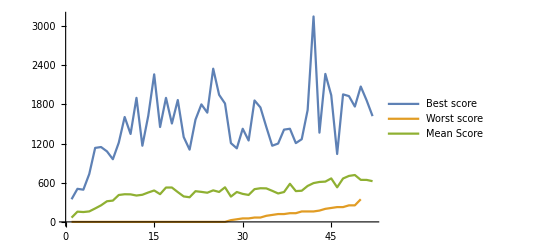

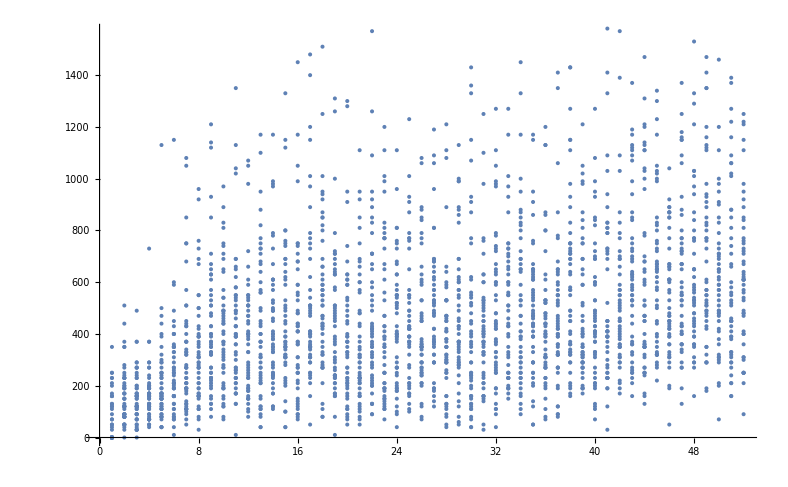

```mathematica
ListLinePlot[{archive4["mostFitness"],#["fitness"]&/@archive4["generations"]⟦1⟧,archive4["totalFitness"]/52},PlotLegends->{"Best score", "Worst score", "Mean Score"}]
ListPlot[Flatten[Table[{i,Round[(#["fitness"]&/@archive4["generations"]⟦i⟧)⟦j⟧,10]},{i,52},{j,50}],1],PlotStyle->Bold]
```

```mathematica
elite=SortBy[Flatten@archive4["generations"],#["fitness"]/@#&]//Last
archive4["generations"]//Last//Last
```

<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→3146.67|>

<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1620.|>

```mathematica
archive
```

<|size→52,totalFitness→{3386.67,8160.,7853.33,8346.67,10706.7,13200.,16440.,16966.7,21433.3,22020.,21933.3,21000.,21613.3,23426.7,25020.,22093.3,27360.,27380.,23740.,20280.,19620.,24453.3,23900.,23233.3,25113.3,23846.7,27553.3,20146.7,23813.3,22306.7,21460.,26073.3,26800.,26693.3,24746.7,22653.3,23780.,30353.3,24533.3,24826.7,28640.,30906.7,31806.7,32093.3,34640.,27546.7,34566.7,36626.7,37333.3,33480.,33440.,32440.},mostFitness→{346.667,506.667,493.333,733.333,1133.33,1146.67,1080.,960.,1213.33,1606.67,1346.67,1900.,1166.67,1626.67,2260.,1453.33,1900.,1506.67,1866.67,1300.,1106.67,1566.67,1800.,1673.33,2346.67,1946.67,1813.33,1206.67,1126.67,1426.67,1246.67,1860.,1753.33,1453.33,1166.67,1200.,1413.33,1426.67,1206.67,1266.67,1713.33,3146.67,1366.67,2266.67,1940.,1040.,1953.33,1926.67,1766.67,2073.33,1860.,1620.},elites→{{<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→213.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→226.667|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→226.667|>,<|rowsCleared→-0.237547,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.288797,fitness→253.333|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→253.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>},{<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→280.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.175907,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>},{<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→493.333|>},{<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→293.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→373.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→733.333|>},{<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.129444,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1133.33|>},{<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.452903,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→600.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>},{<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1080.|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→960.|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1140.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1213.33|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→826.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→893.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→973.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1606.67|>},{<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→1020.|>,<|rowsCleared→0.392522,weightedHeight→-0.0848519,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1040.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1133.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1346.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1053.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1066.67|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0699963,fitness→766.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→820.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1100.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1166.67|>},{<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→793.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→993.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1166.67|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1626.67|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1326.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→2260.|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1173.33|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1453.33|>},{<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1400.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→1480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→940.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1253.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1506.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→786.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1313.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→1866.67|>},{<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→906.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.392522,weightedHeight→0.0165313,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→1280.|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1300.|>},{<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1093.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1566.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.449964,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1800.|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.449964,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→813.333|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→813.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→960.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1113.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1673.33|>},{<|rowsCleared→0.414967,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→873.333|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→913.333|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1226.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→2346.67|>},{<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→893.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1060.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1080.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1946.67|>},{<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→960.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1060.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1086.67|>,<|rowsCleared→-0.214079,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1193.33|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1606.67|>,<|rowsCleared→0.392522,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1813.33|>},{<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→0.353805,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1080.|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1206.67|>},{<|rowsCleared→0.392381,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→-0.215725,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→993.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→0.344453,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1126.67|>},{<|rowsCleared→0.344453,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.392522,weightedHeight→0.0185,cumulativeHeight→-0.520453,relativeHeight→0.455398,holes→-0.214967,roughness→-0.0622939,fitness→1073.33|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1326.67|>,<|rowsCleared→0.344453,weightedHeight→0.018948,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1360.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→1426.67|>},{<|rowsCleared→0.392381,weightedHeight→0.018948,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→713.333|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→766.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1100.|>,<|rowsCleared→0.344453,weightedHeight→0.018948,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1246.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1053.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→1266.67|>,<|rowsCleared→0.344453,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1860.|>},{<|rowsCleared→0.411524,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→933.333|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.344453,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1166.67|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.416629,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1266.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1753.33|>},{<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→880.|>,<|rowsCleared→0.392381,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.214967,roughness→-0.0622939,fitness→1173.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1333.33|>,<|rowsCleared→0.411524,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→1453.33|>},{<|rowsCleared→0.353805,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→760.|>,<|rowsCleared→0.278424,weightedHeight→0.0185,cumulativeHeight→-0.466931,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→860.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0667879,fitness→913.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.20218,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→0.293868,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1146.67|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.214967,roughness→-0.0622939,fitness→1166.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.521037,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→860.|>,<|rowsCleared→0.278424,weightedHeight→0.0185,cumulativeHeight→-0.466931,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→873.333|>,<|rowsCleared→0.344453,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1126.67|>,<|rowsCleared→0.293868,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1133.33|>,<|rowsCleared→0.278424,weightedHeight→0.018948,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>},{<|rowsCleared→0.248645,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0643287,fitness→773.333|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853821,holes→-0.23532,roughness→-0.0667879,fitness→780.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.521037,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→873.333|>,<|rowsCleared→0.344453,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1060.|>,<|rowsCleared→0.353805,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1353.33|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1413.33|>},{<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.5152,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1113.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.521037,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>,<|rowsCleared→0.293868,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0559654,fitness→1273.33|>,<|rowsCleared→0.248645,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0643287,fitness→1426.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1426.67|>},{<|rowsCleared→0.278424,weightedHeight→0.0185,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0510017,fitness→873.333|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.450832,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→993.333|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1020.|>,<|rowsCleared→0.248645,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.411524,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1206.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.521037,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0582825,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→933.333|>,<|rowsCleared→0.392522,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0559654,fitness→946.667|>,<|rowsCleared→0.392522,weightedHeight→0.0185,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.411524,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1080.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1266.67|>},{<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1026.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.450832,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1093.33|>,<|rowsCleared→0.411524,weightedHeight→0.0185,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1326.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.526408,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1413.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.521037,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0582825,fitness→1580.|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1713.33|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0622939,fitness→1026.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1086.67|>,<|rowsCleared→0.411524,weightedHeight→0.0185,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1386.67|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1573.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1806.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→3146.67|>},{<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.246624,roughness→-0.0559654,fitness→1106.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1120.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0622939,fitness→1126.67|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1166.67|>,<|rowsCleared→0.278424,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0559654,fitness→1186.67|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1366.67|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0622939,fitness→1140.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1200.|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1213.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1306.67|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1473.33|>,<|rowsCleared→0.278424,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0559654,fitness→2266.67|>},{<|rowsCleared→0.278424,weightedHeight→0.0185,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0622939,fitness→1166.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1233.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0622939,fitness→1300.|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1340.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1740.|>,<|rowsCleared→0.278424,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→1940.|>},{<|rowsCleared→0.278424,weightedHeight→0.0197895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→873.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0622939,fitness→873.333|>,<|rowsCleared→0.278424,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→886.667|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0559654,fitness→886.667|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1040.|>},{<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1160.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1180.|>,<|rowsCleared→0.411524,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→1246.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1366.67|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1633.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.497494,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1953.33|>},{<|rowsCleared→0.411524,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→1326.67|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1533.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1626.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0559654,fitness→1646.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0825596,holes→-0.23532,roughness→-0.0559654,fitness→1726.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1926.67|>},{<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0825596,holes→-0.222317,roughness→-0.0559654,fitness→1346.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→1353.33|>,<|rowsCleared→0.411524,weightedHeight→0.0213489,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1413.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1473.33|>,<|rowsCleared→0.411524,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1613.33|>,<|rowsCleared→0.300994,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1766.67|>},{<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1000.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1113.33|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0559654,fitness→1200.|>,<|rowsCleared→0.300994,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1460.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1946.67|>,<|rowsCleared→0.278424,weightedHeight→0.0186525,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→2073.33|>},{<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.261909,roughness→-0.0559654,fitness→1220.|>,<|rowsCleared→0.278424,weightedHeight→0.0186525,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1273.33|>,<|rowsCleared→0.242441,weightedHeight→0.0193257,cumulativeHeight→-0.497494,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1373.33|>,<|rowsCleared→0.411524,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247443,roughness→-0.0559654,fitness→1386.67|>,<|rowsCleared→0.300994,weightedHeight→0.0213489,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1706.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→1860.|>},{<|rowsCleared→0.411524,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247443,roughness→-0.0559654,fitness→1106.67|>,<|rowsCleared→0.242441,weightedHeight→0.0193257,cumulativeHeight→-0.497494,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1153.33|>,<|rowsCleared→0.278424,weightedHeight→-0.089451,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.201258,roughness→-0.0559654,fitness→1206.67|>,<|rowsCleared→0.411524,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247443,roughness→-0.0559654,fitness→1220.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.247096,roughness→-0.0559654,fitness→1253.33|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.518447,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0559654,fitness→1620.|>}},generations→{{<|rowsCleared→-0.405447,weightedHeight→-0.49779,cumulativeHeight→-0.395143,relativeHeight→0.327306,holes→-0.145232,roughness→0.17388,fitness→0.|>,<|rowsCleared→-0.402579,weightedHeight→-0.161196,cumulativeHeight→-0.138061,relativeHeight→-0.293663,holes→-0.180217,roughness→0.396321,fitness→0.|>,<|rowsCleared→-0.396801,weightedHeight→-0.433975,cumulativeHeight→0.242273,relativeHeight→-0.134298,holes→-0.256782,roughness→0.0144658,fitness→0.|>,<|rowsCleared→-0.357752,weightedHeight→0.361402,cumulativeHeight→-0.0288148,relativeHeight→-0.00682817,holes→0.411954,roughness→0.0431268,fitness→0.|>,<|rowsCleared→-0.350002,weightedHeight→0.395541,cumulativeHeight→-0.389281,relativeHeight→0.409193,holes→-0.0732122,roughness→0.411021,fitness→0.|>,<|rowsCleared→-0.348193,weightedHeight→0.219042,cumulativeHeight→0.433721,relativeHeight→-0.30369,holes→0.458165,roughness→-0.0329519,fitness→0.|>,<|rowsCleared→-0.309199,weightedHeight→0.115109,cumulativeHeight→0.341502,relativeHeight→0.439995,holes→0.213915,roughness→-0.0259949,fitness→0.|>,<|rowsCleared→-0.286512,weightedHeight→-0.0654298,cumulativeHeight→-0.335289,relativeHeight→-0.342695,holes→0.425968,roughness→0.382243,fitness→0.|>,<|rowsCleared→-0.262954,weightedHeight→-0.309076,cumulativeHeight→0.0564105,relativeHeight→0.47451,holes→-0.0788725,roughness→0.437976,fitness→0.|>,<|rowsCleared→-0.222731,weightedHeight→0.377187,cumulativeHeight→-0.288379,relativeHeight→0.323764,holes→-0.332091,roughness→0.0253633,fitness→0.|>,<|rowsCleared→-0.210142,weightedHeight→0.110666,cumulativeHeight→0.259724,relativeHeight→-0.167306,holes→-0.305753,roughness→0.214555,fitness→0.|>,<|rowsCleared→-0.191515,weightedHeight→-0.45966,cumulativeHeight→0.375188,relativeHeight→0.176615,holes→-0.468507,roughness→0.447578,fitness→0.|>,<|rowsCleared→-0.191052,weightedHeight→-0.257438,cumulativeHeight→-0.117488,relativeHeight→-0.193622,holes→-0.0616372,roughness→0.481187,fitness→0.|>,<|rowsCleared→-0.186945,weightedHeight→-0.246222,cumulativeHeight→0.0481813,relativeHeight→-0.265772,holes→-0.260754,roughness→0.267196,fitness→0.|>,<|rowsCleared→-0.0638895,weightedHeight→0.0894549,cumulativeHeight→0.387159,relativeHeight→-0.097988,holes→0.247378,roughness→0.0806688,fitness→0.|>,<|rowsCleared→-0.0472317,weightedHeight→0.0425713,cumulativeHeight→-0.1031,relativeHeight→-0.249449,holes→-0.40304,roughness→0.372582,fitness→0.|>,<|rowsCleared→-0.033109,weightedHeight→-0.256462,cumulativeHeight→-0.441413,relativeHeight→-0.0224618,holes→0.298873,roughness→0.0628231,fitness→0.|>,<|rowsCleared→-0.0189996,weightedHeight→-0.450879,cumulativeHeight→-0.340959,relativeHeight→-0.0408951,holes→-0.0392477,roughness→0.309988,fitness→0.|>,<|rowsCleared→0.0113303,weightedHeight→-0.364066,cumulativeHeight→-0.0292152,relativeHeight→-0.396844,holes→-0.324522,roughness→0.268893,fitness→0.|>,<|rowsCleared→0.0327626,weightedHeight→0.356692,cumulativeHeight→-0.310992,relativeHeight→0.396076,holes→-0.396448,roughness→0.480859,fitness→0.|>,<|rowsCleared→0.0342826,weightedHeight→0.0212317,cumulativeHeight→-0.0823785,relativeHeight→-0.0831267,holes→-0.417904,roughness→0.048391,fitness→0.|>,<|rowsCleared→0.0358162,weightedHeight→-0.407638,cumulativeHeight→0.134002,relativeHeight→-0.179649,holes→-0.149033,roughness→0.0757052,fitness→0.|>,<|rowsCleared→0.144002,weightedHeight→-0.248501,cumulativeHeight→0.418065,relativeHeight→-0.0373936,holes→0.0894163,roughness→0.0882732,fitness→0.|>,<|rowsCleared→0.210516,weightedHeight→-0.392819,cumulativeHeight→-0.300574,relativeHeight→0.324092,holes→0.486444,roughness→0.107921,fitness→0.|>,<|rowsCleared→0.297837,weightedHeight→-0.0183513,cumulativeHeight→-0.400634,relativeHeight→0.33488,holes→-0.135129,roughness→0.248539,fitness→0.|>,<|rowsCleared→0.336137,weightedHeight→0.151285,cumulativeHeight→0.0724293,relativeHeight→0.484612,holes→0.441648,roughness→0.372443,fitness→0.|>,<|rowsCleared→0.484287,weightedHeight→-0.16234,cumulativeHeight→-0.297493,relativeHeight→0.186332,holes→0.0719874,roughness→0.363067,fitness→0.|>,<|rowsCleared→-0.240978,weightedHeight→0.33438,cumulativeHeight→-0.0547623,relativeHeight→-0.469966,holes→0.104696,roughness→-0.0549358,fitness→26.6667|>,<|rowsCleared→-0.495584,weightedHeight→0.304757,cumulativeHeight→0.386755,relativeHeight→0.172738,holes→0.325962,roughness→-0.284719,fitness→40.|>,<|rowsCleared→0.0771147,weightedHeight→-0.266048,cumulativeHeight→0.456849,relativeHeight→0.122611,holes→0.220188,roughness→-0.115039,fitness→53.3333|>,<|rowsCleared→0.444179,weightedHeight→0.375915,cumulativeHeight→-0.324252,relativeHeight→-0.354561,holes→-0.34709,roughness→-0.324897,fitness→53.3333|>,<|rowsCleared→-0.399586,weightedHeight→-0.168066,cumulativeHeight→-0.472352,relativeHeight→0.28271,holes→0.479935,roughness→-0.431823,fitness→66.6667|>,<|rowsCleared→-0.217712,weightedHeight→-0.448749,cumulativeHeight→-0.267944,relativeHeight→-0.208943,holes→0.172448,roughness→-0.142191,fitness→66.6667|>,<|rowsCleared→0.315226,weightedHeight→0.309911,cumulativeHeight→0.190019,relativeHeight→0.26177,holes→0.16387,roughness→-0.305228,fitness→93.3333|>,<|rowsCleared→0.0855802,weightedHeight→0.142939,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→-0.0478573,roughness→-0.318128,fitness→106.667|>,<|rowsCleared→-0.429837,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.0675658,holes→0.347869,roughness→-0.0484286,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→-0.399894,cumulativeHeight→0.177834,relativeHeight→-0.214735,holes→0.327818,roughness→-0.281459,fitness→120.|>,<|rowsCleared→-0.357227,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.463842,roughness→-0.136185,fitness→133.333|>,<|rowsCleared→0.181462,weightedHeight→-0.47483,cumulativeHeight→0.062579,relativeHeight→0.0418232,holes→0.129933,roughness→-0.223691,fitness→133.333|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→160.|>,<|rowsCleared→0.133555,weightedHeight→-0.177142,cumulativeHeight→-0.299925,relativeHeight→0.200202,holes→-0.318146,roughness→-0.168708,fitness→160.|>,<|rowsCleared→0.458615,weightedHeight→-0.416492,cumulativeHeight→-0.342808,relativeHeight→-0.247288,holes→-0.0208306,roughness→-0.426492,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→213.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→226.667|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→226.667|>,<|rowsCleared→-0.237547,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.288797,fitness→253.333|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→253.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>},{<|rowsCleared→-0.429837,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.0675658,holes→0.347869,roughness→-0.0484286,fitness→0.|>,<|rowsCleared→-0.429837,weightedHeight→-0.266048,cumulativeHeight→0.456849,relativeHeight→-0.0675658,holes→0.220188,roughness→-0.115039,fitness→26.6667|>,<|rowsCleared→0.253309,weightedHeight→0.488266,cumulativeHeight→0.449951,relativeHeight→0.435211,holes→0.40468,roughness→-0.400177,fitness→40.|>,<|rowsCleared→-0.429837,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.0484286,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.466039,fitness→53.3333|>,<|rowsCleared→-0.237547,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.288797,fitness→53.3333|>,<|rowsCleared→0.0855802,weightedHeight→-0.432308,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→0.463842,roughness→-0.136185,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→0.471657,cumulativeHeight→-0.273762,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→80.|>,<|rowsCleared→-0.215387,weightedHeight→-0.399894,cumulativeHeight→0.390148,relativeHeight→-0.214735,holes→0.327818,roughness→-0.281459,fitness→80.|>,<|rowsCleared→0.0855802,weightedHeight→-0.399894,cumulativeHeight→-0.402012,relativeHeight→-0.214735,holes→-0.0478573,roughness→-0.318128,fitness→80.|>,<|rowsCleared→0.0855802,weightedHeight→0.142939,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→-0.0478573,roughness→-0.318128,fitness→80.|>,<|rowsCleared→0.334039,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→80.|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→80.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→-0.357227,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→-0.0853822,holes→0.463842,roughness→-0.136185,fitness→93.3333|>,<|rowsCleared→0.0771147,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.122611,holes→0.347869,roughness→-0.0484286,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→93.3333|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→106.667|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→0.142939,cumulativeHeight→0.177834,relativeHeight→-0.395194,holes→0.327818,roughness→-0.281459,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→-0.179226,cumulativeHeight→0.177834,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.141027,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.400177,fitness→173.333|>,<|rowsCleared→-0.237547,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.0675658,holes→0.347869,roughness→-0.288797,fitness→173.333|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.399894,cumulativeHeight→0.177834,relativeHeight→-0.214735,holes→0.327818,roughness→-0.281459,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→0.334039,weightedHeight→0.0552331,cumulativeHeight→0.426428,relativeHeight→-0.498266,holes→-0.0994356,roughness→-0.143982,fitness→186.667|>,<|rowsCleared→-0.357227,weightedHeight→0.142939,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→-0.0478573,roughness→-0.318128,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.141027,fitness→200.|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→213.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.466039,fitness→226.667|>,<|rowsCleared→-0.399586,weightedHeight→-0.168066,cumulativeHeight→-0.472352,relativeHeight→0.28271,holes→0.479935,roughness→-0.431823,fitness→226.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→240.|>,<|rowsCleared→0.458615,weightedHeight→-0.416492,cumulativeHeight→-0.342808,relativeHeight→-0.0853822,holes→-0.0208306,roughness→-0.426492,fitness→253.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→266.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→280.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.175907,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>},{<|rowsCleared→0.0771147,weightedHeight→0.41448,cumulativeHeight→0.390148,relativeHeight→0.122611,holes→0.347869,roughness→-0.0484286,fitness→0.|>,<|rowsCleared→-0.215387,weightedHeight→-0.168066,cumulativeHeight→0.390148,relativeHeight→0.28271,holes→0.327818,roughness→-0.431823,fitness→26.6667|>,<|rowsCleared→0.0771147,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→0.347869,roughness→-0.0484286,fitness→26.6667|>,<|rowsCleared→0.164889,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.143982,fitness→26.6667|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.327818,roughness→-0.141027,fitness→26.6667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.466039,fitness→40.|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→0.426428,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→53.3333|>,<|rowsCleared→0.0779073,weightedHeight→0.142939,cumulativeHeight→-0.402012,relativeHeight→-0.0853822,holes→-0.0478573,roughness→-0.318128,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→66.6667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.395194,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→0.232096,holes→0.479935,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→-0.399894,cumulativeHeight→0.177834,relativeHeight→-0.214735,holes→0.40468,roughness→-0.281459,fitness→93.3333|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.236374,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→0.142939,cumulativeHeight→0.177834,relativeHeight→-0.0970647,holes→0.327818,roughness→-0.281459,fitness→106.667|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→-0.175907,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→106.667|>,<|rowsCleared→-0.426567,weightedHeight→0.41448,cumulativeHeight→-0.380392,relativeHeight→0.122611,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→-0.357227,weightedHeight→0.142939,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.175907,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→-0.179226,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→0.0855802,weightedHeight→-0.432308,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→0.463842,roughness→-0.136185,fitness→120.|>,<|rowsCleared→0.0855802,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0842997,holes→0.408628,roughness→-0.236374,fitness→120.|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→-0.0478573,roughness→-0.318128,fitness→133.333|>,<|rowsCleared→-0.399586,weightedHeight→-0.399894,cumulativeHeight→-0.472352,relativeHeight→-0.214735,holes→0.479935,roughness→-0.281459,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→0.28271,holes→0.408628,roughness→-0.431823,fitness→146.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.466039,fitness→160.|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.479935,roughness→-0.236374,fitness→160.|>,<|rowsCleared→-0.399586,weightedHeight→-0.168066,cumulativeHeight→-0.472352,relativeHeight→0.28271,holes→0.483805,roughness→-0.431823,fitness→160.|>,<|rowsCleared→-0.15401,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.395194,holes→0.408628,roughness→-0.236374,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.483805,roughness→-0.400177,fitness→160.|>,<|rowsCleared→-0.426567,weightedHeight→0.0552331,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.40468,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→0.425935,cumulativeHeight→0.390148,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→-0.480105,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→-0.38677,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→200.|>,<|rowsCleared→0.164889,weightedHeight→0.0552331,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.164889,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→240.|>,<|rowsCleared→0.164889,weightedHeight→-0.399894,cumulativeHeight→-0.402012,relativeHeight→-0.214735,holes→-0.0478573,roughness→-0.318128,fitness→253.333|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→493.333|>},{<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.466039,fitness→40.|>,<|rowsCleared→-0.247695,weightedHeight→-0.399894,cumulativeHeight→-0.494313,relativeHeight→-0.214735,holes→0.40468,roughness→-0.236374,fitness→53.3333|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→0.13318,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.483805,roughness→-0.400177,fitness→66.6667|>,<|rowsCleared→0.0855802,weightedHeight→-0.38677,cumulativeHeight→0.177834,relativeHeight→-0.0842997,holes→0.408628,roughness→-0.281459,fitness→66.6667|>,<|rowsCleared→0.164889,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.28271,holes→0.408628,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→0.283191,roughness→-0.466039,fitness→80.|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.479935,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→0.28271,holes→0.408628,roughness→-0.431823,fitness→93.3333|>,<|rowsCleared→-0.426567,weightedHeight→0.0552331,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.40468,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→-0.0478573,roughness→-0.236374,fitness→106.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.38677,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→0.426428,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.466039,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.399586,weightedHeight→-0.399894,cumulativeHeight→-0.472352,relativeHeight→-0.214735,holes→0.479935,roughness→-0.281459,fitness→133.333|>,<|rowsCleared→0.164889,weightedHeight→0.0552331,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→133.333|>,<|rowsCleared→0.168918,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.378967,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→146.667|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.129444,fitness→146.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→160.|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→0.479935,roughness→-0.141027,fitness→160.|>,<|rowsCleared→-0.357227,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→160.|>,<|rowsCleared→-0.15401,weightedHeight→-0.089451,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.236374,fitness→166.667|>,<|rowsCleared→0.0855802,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0842997,holes→0.292617,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.479935,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.247288,holes→0.408628,roughness→-0.258223,fitness→200.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.380392,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.466039,fitness→200.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.236374,fitness→213.333|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→226.667|>,<|rowsCleared→-0.399586,weightedHeight→0.425935,cumulativeHeight→-0.472352,relativeHeight→0.21321,holes→0.483805,roughness→-0.236374,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→293.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→373.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→733.333|>},{<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→40.|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→0.479935,roughness→-0.236374,fitness→40.|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→40.|>,<|rowsCleared→-0.247695,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→-0.399586,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.466039,fitness→80.|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.485974,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→80.|>,<|rowsCleared→-0.426567,weightedHeight→0.0552331,cumulativeHeight→-0.494313,relativeHeight→-0.247288,holes→0.408628,roughness→-0.258223,fitness→93.3333|>,<|rowsCleared→0.0855802,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0842997,holes→0.292617,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.438008,relativeHeight→-0.247288,holes→0.408628,roughness→-0.258223,fitness→106.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.236374,fitness→106.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.479935,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.466039,fitness→120.|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.283191,roughness→-0.236374,fitness→133.333|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.483805,roughness→-0.400177,fitness→133.333|>,<|rowsCleared→-0.221716,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→0.41448,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.283191,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.494313,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→0.28271,holes→-0.23532,roughness→-0.431823,fitness→160.|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.23532,roughness→-0.129444,fitness→173.333|>,<|rowsCleared→-0.399586,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.483805,roughness→-0.236374,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→0.459366,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.472352,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→173.333|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→213.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→226.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.38677,cumulativeHeight→-0.485974,relativeHeight→-0.161596,holes→-0.0946783,roughness→-0.1475,fitness→226.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.549518,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.431823,fitness→293.333|>,<|rowsCleared→0.164889,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.408628,roughness→-0.129444,fitness→293.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.0478573,roughness→-0.129444,fitness→300.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→-0.221716,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0970647,holes→-0.0946783,roughness→-0.143982,fitness→346.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.129444,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1133.33|>},{<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.236374,fitness→13.3333|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.129444,fitness→40.|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→-0.0946783,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→-0.23532,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.408628,roughness→-0.236374,fitness→80.|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→80.|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→-0.0478573,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→-0.247695,weightedHeight→0.459366,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.129444,fitness→133.333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.129444,fitness→133.333|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.472352,relativeHeight→-0.233743,holes→0.283191,roughness→-0.129444,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→0.459366,cumulativeHeight→-0.494313,relativeHeight→0.0800533,holes→-0.0946783,roughness→-0.318128,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.107738,holes→0.408628,roughness→-0.236374,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.39065,holes→0.283191,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.431823,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.459366,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.479935,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.164889,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→0.455398,holes→0.408628,roughness→-0.129444,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.549518,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→0.39065,holes→-0.0861425,roughness→-0.143982,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.236374,fitness→260.|>,<|rowsCleared→0.253309,weightedHeight→-0.38677,cumulativeHeight→-0.549518,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.059695,fitness→306.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.236374,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→333.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→353.333|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→360.|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.132114,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.452903,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→600.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>},{<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.132114,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.408628,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.262447,roughness→-0.143982,fitness→106.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.321594,roughness→-0.0642571,fitness→106.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→-0.093662,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.132114,fitness→133.333|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→-0.0797957,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.479935,roughness→-0.132114,fitness→140.|>,<|rowsCleared→0.253309,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.0861425,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.431823,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.132114,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→-0.23532,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.239821,weightedHeight→0.459366,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→0.283191,roughness→-0.129444,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.00774957,roughness→-0.143982,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→-0.0946783,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→-0.0861425,roughness→-0.143982,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→-0.452903,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→513.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1080.|>},{<|rowsCleared→0.253309,weightedHeight→0.459366,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→26.6667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→73.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.283191,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→-0.239821,weightedHeight→0.459366,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.101617,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.239821,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.466039,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→-0.23532,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.236374,fitness→193.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.0946783,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.0839086,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.0946783,roughness→-0.129444,fitness→320.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→326.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→960.|>},{<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.236374,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.548204,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.164889,weightedHeight→-0.089451,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→0.00774957,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.253309,weightedHeight→-0.0883641,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→-0.0839086,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0689059,fitness→353.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.312643,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.457635,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→653.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1140.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1213.33|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→-0.0883641,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.293679,holes→0.283191,roughness→-0.0622813,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→300.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.440849,holes→0.00774957,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.253309,weightedHeight→-0.0883641,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→0.392522,weightedHeight→-0.0839086,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.231592,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.48899,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.0839086,cumulativeHeight→-0.457635,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.00774957,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→653.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→826.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→893.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→973.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1606.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.428949,holes→-0.23532,roughness→-0.0622939,fitness→13.3333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→126.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622813,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→300.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.48899,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00851225,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.469576,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→620.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→653.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→1020.|>,<|rowsCleared→0.392522,weightedHeight→-0.0848519,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1040.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1133.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1346.67|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→-0.247695,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00851225,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→0.392522,weightedHeight→0.0167981,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0703214,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→0.00851225,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.0848519,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→513.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1053.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1066.67|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0167981,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00851225,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→0.363344,weightedHeight→-0.089451,cumulativeHeight→-0.430164,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→-0.185089,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.28589,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→353.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→0.00774957,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.247695,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→566.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→600.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.516052,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→733.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0699963,fitness→766.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→820.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1100.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1166.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.28589,weightedHeight→0.0193257,cumulativeHeight→-0.430164,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.363344,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0699963,fitness→353.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.329075,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0672789,fitness→493.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→520.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→780.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→793.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→993.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1166.67|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1626.67|>},{<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→140.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→233.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→353.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→606.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→620.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→673.333|>,<|rowsCleared→0.392522,weightedHeight→0.0185423,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.260238,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1326.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→2260.|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→140.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.260238,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→0.0185423,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→646.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1173.33|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1453.33|>},{<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→53.3333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.260238,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→473.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0185423,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→566.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→620.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→733.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→773.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→786.667|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1400.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→1480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0219611,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.249047,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0774289,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→606.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→820.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→846.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→866.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→940.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1253.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1506.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→13.3333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0774289,holes→0.00774957,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→193.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0598455,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00839897,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→300.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.222405,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.552441,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0563036,fitness→566.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→633.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→646.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→673.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→786.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1313.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→1866.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→46.6667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0563036,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0200482,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.402834,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→153.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0563036,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→233.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→513.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.

```mathematica
archive3=<|"size"->31,"totalFitness"->{3386.6666666666665,8160.,7853.333333333333,8346.666666666666,10706.666666666666,13200.,16440.,16966.666666666664,21433.333333333332,22020.,21933.33333333333,21000.,21613.333333333332,23426.666666666664,25020.,22093.33333333333,27360.,27380.,23740.,20280.,19620.,24453.33333333333,23900.,23233.33333333333,25113.33333333333,23846.666666666664,27553.33333333333,20146.666666666664,23813.333333333332,22306.666666666664,21460.},"mostFitness"->{346.66666666666663,506.66666666666663,493.3333333333333,733.3333333333333,1133.3333333333333,1146.6666666666665,1080.,960.,1213.3333333333333,1606.6666666666665,1346.6666666666665,1900.,1166.6666666666665,1626.6666666666665,2260.,1453.3333333333333,1900.,1506.6666666666665,1866.6666666666665,1300.,1106.6666666666665,1566.6666666666665,1800.,1673.3333333333333,2346.6666666666665,1946.6666666666665,1813.3333333333333,1206.6666666666665,1126.6666666666665,1426.6666666666665,1246.6666666666665},"elites"->{{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.2887973708926581,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>},{<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->280.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>},{<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>},{<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->286.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->373.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->733.3333333333333|>},{<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->453.3333333333333|>,<|"rowsCleared"->-0.4529034461712001,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->593.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->600.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>},{<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->680.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1080.|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->666.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->686.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->726.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->960.|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->713.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1140.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1213.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->806.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->826.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->893.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->973.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1606.6666666666665|>},{<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1020.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08485194124344798,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1040.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1346.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->660.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->720.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1053.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1066.6666666666665|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1900.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06999626363129945,"fitness"->766.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->820.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->880.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->953.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1100.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->793.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->966.6666666666666|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->993.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007354901721975732,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1626.6666666666665|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->800.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->800.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1120.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1153.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1326.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->2260.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->753.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1173.3333333333333|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1453.3333333333333|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007354901721975732,"roughness"->-0.06229388264614899,"fitness"->1400.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->1480.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1900.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->940.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->953.3333333333333|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1253.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1506.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->720.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->786.6666666666666|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24035098541089878,"roughness"->-0.06229388264614899,"fitness"->1000.|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1260.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1313.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.017189510601376756,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.07508394237959543,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1866.6666666666665|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.008106612471307693,"roughness"->-0.06229388264614899,"fitness"->680.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->740.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->906.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->953.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.016531345964302297,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->1280.|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.01931861790688983,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1300.|>},{<|"rowsCleared"->0.3520965092238475,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->753.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->806.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>},{<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->886.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1093.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1260.|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1566.6666666666665|>},{<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4499644931867572,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1200.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1800.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4499644931867572,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->813.3333333333333|>,<|"rowsCleared"->0.3520965092238475,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->813.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->960.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1113.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1673.3333333333333|>},{<|"rowsCleared"->0.4149671943211081,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->913.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1226.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->2346.6666666666665|>},{<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->880.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->893.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1060.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1080.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1946.6666666666665|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->960.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1060.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1086.6666666666665|>,<|"rowsCleared"->-0.21407869431545737,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1193.3333333333333|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1606.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1813.3333333333333|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->640.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->660.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->886.6666666666666|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1080.|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1206.6666666666665|>},{<|"rowsCleared"->0.39238091442286027,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->880.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->886.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->993.3333333333333|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1000.|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1126.6666666666665|>},{<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.5204529252163625,"relativeHeight"->0.4553977168762393,"holes"->-0.21496695840502325,"roughness"->-0.06229388264614899,"fitness"->1073.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1153.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1326.6666666666665|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1360.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->1426.6666666666665|>},{<|"rowsCleared"->0.39238091442286027,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->713.3333333333333|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->766.6666666666666|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1100.|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1246.6666666666665|>}},"generations"->{{<|"rowsCleared"->-0.40544677022517184,"weightedHeight"->-0.49779024706076247,"cumulativeHeight"->-0.395142858308994,"relativeHeight"->0.3273064008622564,"holes"->-0.14523186220564122,"roughness"->0.1738799952670369,"fitness"->0.|>,<|"rowsCleared"->-0.40257917655244047,"weightedHeight"->-0.1611956821637468,"cumulativeHeight"->-0.13806063033611693,"relativeHeight"->-0.2936626788836876,"holes"->-0.1802170101541225,"roughness"->0.39632062320754957,"fitness"->0.|>,<|"rowsCleared"->-0.39680128695868033,"weightedHeight"->-0.43397502096712604,"cumulativeHeight"->0.24227267993588453,"relativeHeight"->-0.13429801174114497,"holes"->-0.2567823812206993,"roughness"->0.014465808850763429,"fitness"->0.|>,<|"rowsCleared"->-0.35775189643895944,"weightedHeight"->0.36140176468808405,"cumulativeHeight"->-0.028814790205363483,"relativeHeight"->-0.006828168804156265,"holes"->0.41195359105396956,"roughness"->0.043126834111250956,"fitness"->0.|>,<|"rowsCleared"->-0.35000179243687524,"weightedHeight"->0.395540647715404,"cumulativeHeight"->-0.3892806559002504,"relativeHeight"->0.4091933906781755,"holes"->-0.0732121536095185,"roughness"->0.41102139946337846,"fitness"->0.|>,<|"rowsCleared"->-0.348193208249836,"weightedHeight"->0.21904180991479594,"cumulativeHeight"->0.4337210550725774,"relativeHeight"->-0.30368988528925467,"holes"->0.458165161424551,"roughness"->-0.03295185095352782,"fitness"->0.|>,<|"rowsCleared"->-0.309198944926814,"weightedHeight"->0.11510871188928284,"cumulativeHeight"->0.341501815141495,"relativeHeight"->0.43999505172236875,"holes"->0.2139151687981189,"roughness"->-0.02599487404924239,"fitness"->0.|>,<|"rowsCleared"->-0.28651163123528045,"weightedHeight"->-0.06542978465760996,"cumulativeHeight"->-0.3352893185967818,"relativeHeight"->-0.3426946344150086,"holes"->0.4259679004767227,"roughness"->0.38224260773130414,"fitness"->0.|>,<|"rowsCleared"->-0.262954303985923,"weightedHeight"->-0.3090756902459362,"cumulativeHeight"->0.05641053598582446,"relativeHeight"->0.47451027805220014,"holes"->-0.07887245320714631,"roughness"->0.4379760126853509,"fitness"->0.|>,<|"rowsCleared"->-0.22273077014153775,"weightedHeight"->0.37718736707985423,"cumulativeHeight"->-0.28837856199642875,"relativeHeight"->0.32376438914607375,"holes"->-0.33209055240893925,"roughness"->0.025363330627990344,"fitness"->0.|>,<|"rowsCleared"->-0.2101419354519598,"weightedHeight"->0.11066602330323305,"cumulativeHeight"->0.2597238587655253,"relativeHeight"->-0.1673063880751,"holes"->-0.30575262746800314,"roughness"->0.2145547001869561,"fitness"->0.|>,<|"rowsCleared"->-0.1915154379888191,"weightedHeight"->-0.45966015912286595,"cumulativeHeight"->0.3751876389608615,"relativeHeight"->0.17661541849987294,"holes"->-0.4685065984888883,"roughness"->0.4475778538701698,"fitness"->0.|>,<|"rowsCleared"->-0.19105234907968893,"weightedHeight"->-0.25743755952531266,"cumulativeHeight"->-0.11748759588121205,"relativeHeight"->-0.19362183948591838,"holes"->-0.06163716261826013,"roughness"->0.4811867020559515,"fitness"->0.|>,<|"rowsCleared"->-0.18694478017070115,"weightedHeight"->-0.2462215281236091,"cumulativeHeight"->0.04818131918756419,"relativeHeight"->-0.26577158226714515,"holes"->-0.2607540951175813,"roughness"->0.26719631805803545,"fitness"->0.|>,<|"rowsCleared"->-0.06388951336894033,"weightedHeight"->0.08945486053717921,"cumulativeHeight"->0.38715908423721035,"relativeHeight"->-0.09798804763905844,"holes"->0.24737767260632015,"roughness"->0.08066876758619856,"fitness"->0.|>,<|"rowsCleared"->-0.047231689304687796,"weightedHeight"->0.04257130621191241,"cumulativeHeight"->-0.10309993083860669,"relativeHeight"->-0.2494486766255979,"holes"->-0.40304029578616585,"roughness"->0.37258222771162264,"fitness"->0.|>,<|"rowsCleared"->-0.033108981698541706,"weightedHeight"->-0.2564618041939657,"cumulativeHeight"->-0.4414127382221231,"relativeHeight"->-0.02246183881751329,"holes"->0.2988727397993236,"roughness"->0.06282310144607872,"fitness"->0.|>,<|"rowsCleared"->-0.01899961210863177,"weightedHeight"->-0.45087937655579013,"cumulativeHeight"->-0.3409586828953832,"relativeHeight"->-0.04089511157813508,"holes"->-0.03924772663875897,"roughness"->0.3099876510824404,"fitness"->0.|>,<|"rowsCleared"->0.011330265205614198,"weightedHeight"->-0.3640659479541901,"cumulativeHeight"->-0.029215169469899882,"relativeHeight"->-0.39684417057975163,"holes"->-0.3245223301760405,"roughness"->0.2688930853319562,"fitness"->0.|>,<|"rowsCleared"->0.03276261115642587,"weightedHeight"->0.3566924713573527,"cumulativeHeight"->-0.31099230066860817,"relativeHeight"->0.39607627344945384,"holes"->-0.39644839206600335,"roughness"->0.4808590385899618,"fitness"->0.|>,<|"rowsCleared"->0.034282613341974244,"weightedHeight"->0.021231708259875193,"cumulativeHeight"->-0.08237848775054402,"relativeHeight"->-0.08312665605387792,"holes"->-0.4179042461821385,"roughness"->0.04839095476704136,"fitness"->0.|>,<|"rowsCleared"->0.035816218490120066,"weightedHeight"->-0.4076377741897035,"cumulativeHeight"->0.13400198869497082,"relativeHeight"->-0.1796494634156034,"holes"->-0.14903285154814716,"roughness"->0.07570518240035051,"fitness"->0.|>,<|"rowsCleared"->0.14400158432808086,"weightedHeight"->-0.24850144637646832,"cumulativeHeight"->0.4180650171330744,"relativeHeight"->-0.03739357154296252,"holes"->0.08941634823427269,"roughness"->0.08827318151512165,"fitness"->0.|>,<|"rowsCleared"->0.21051573343555208,"weightedHeight"->-0.39281926244307197,"cumulativeHeight"->-0.30057432487732605,"relativeHeight"->0.32409173862171103,"holes"->0.4864435038233219,"roughness"->0.10792129037007037,"fitness"->0.|>,<|"rowsCleared"->0.29783719067638725,"weightedHeight"->-0.018351297706122205,"cumulativeHeight"->-0.40063447034935673,"relativeHeight"->0.3348797153412899,"holes"->-0.1351287166677413,"roughness"->0.24853920814734543,"fitness"->0.|>,<|"rowsCleared"->0.3361368108070064,"weightedHeight"->0.15128537938694442,"cumulativeHeight"->0.07242934122328393,"relativeHeight"->0.48461204063486196,"holes"->0.4416475964366391,"roughness"->0.3724434145690241,"fitness"->0.|>,<|"rowsCleared"->0.4842865188451533,"weightedHeight"->-0.1623400725894084,"cumulativeHeight"->-0.2974928640156478,"relativeHeight"->0.1863323992123871,"holes"->0.07198735535799794,"roughness"->0.36306736484078916,"fitness"->0.|>,<|"rowsCleared"->-0.24097806521720289,"weightedHeight"->0.33438022210992835,"cumulativeHeight"->-0.05476230880476041,"relativeHeight"->-0.46996647593060525,"holes"->0.10469636270478078,"roughness"->-0.05493582500592442,"fitness"->26.666666666666664|>,<|"rowsCleared"->-0.49558405283661355,"weightedHeight"->0.3047573573279032,"cumulativeHeight"->0.3867552403907961,"relativeHeight"->0.17273756865451273,"holes"->0.325962087086505,"roughness"->-0.2847185052752903,"fitness"->40.|>,<|"rowsCleared"->0.07711465272147233,"weightedHeight"->-0.2660484630816964,"cumulativeHeight"->0.4568492514804583,"relativeHeight"->0.12261051549925428,"holes"->0.22018812286814882,"roughness"->-0.11503851728794046,"fitness"->53.33333333333333|>,<|"rowsCleared"->0.44417878070809524,"weightedHeight"->0.3759153796207506,"cumulativeHeight"->-0.3242524743083124,"relativeHeight"->-0.35456128567591483,"holes"->-0.3470900288407368,"roughness"->-0.32489716728951,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2827102489554474,"holes"->0.4799346755968472,"roughness"->-0.431823457439406,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21771221812212116,"weightedHeight"->-0.44874922019292285,"cumulativeHeight"->-0.2679440120123726,"relativeHeight"->-0.2089432852766564,"holes"->0.17244842995482812,"roughness"->-0.1421905888331405,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.315225611717443,"weightedHeight"->0.30991121934111,"cumulativeHeight"->0.19001869161467466,"relativeHeight"->0.26176990606232486,"holes"->0.16386980976011079,"roughness"->-0.3052282145482579,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.06756584526092557,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.21473450883982514,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->120.|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.18146246100668173,"weightedHeight"->-0.47482992323129447,"cumulativeHeight"->0.06257898442717269,"relativeHeight"->0.04182316557874044,"holes"->0.12993273134372418,"roughness"->-0.2236906323787602,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->160.|>,<|"rowsCleared"->0.13355470272970416,"weightedHeight"->-0.17714184868316485,"cumulativeHeight"->-0.2999253631239429,"relativeHeight"->0.2002017262301412,"holes"->-0.3181460256987667,"roughness"->-0.1687077764450582,"fitness"->160.|>,<|"rowsCleared"->0.4586153412515708,"weightedHeight"->-0.4164922520999812,"cumulativeHeight"->-0.3428076811256342,"relativeHeight"->-0.24728758135669882,"holes"->-0.02083061249937579,"roughness"->-0.4264915876094988,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.2887973708926581,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>},{<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.06756584526092557,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->0.|>,<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->-0.2660484630816964,"cumulativeHeight"->0.4568492514804583,"relativeHeight"->-0.06756584526092557,"holes"->0.22018812286814882,"roughness"->-0.11503851728794046,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->0.43521087578591033,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->40.|>,<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.04842855693163872,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.46603896285818713,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.2887973708926581,"fitness"->53.33333333333333|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->80.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->-0.21473450883982514,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->80.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.21473450883982514,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->80.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->80.|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->80.|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->80.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->-0.08538224568287012,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.07711465272147233,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.12261051549925428,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.39519419624995167,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.17783394933842,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.14102674843966456,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.06756584526092557,"holes"->0.34786876586056725,"roughness"->-0.2887973708926581,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.21473450883982514,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->-0.4982657484407931,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.14102674843966456,"fitness"->200.|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.46603896285818713,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2827102489554474,"holes"->0.4799346755968472,"roughness"->-0.431823457439406,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->240.|>,<|"rowsCleared"->0.4586153412515708,"weightedHeight"->-0.4164922520999812,"cumulativeHeight"->-0.3428076811256342,"relativeHeight"->-0.08538224568287012,"holes"->-0.02083061249937579,"roughness"->-0.4264915876094988,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->280.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>},{<|"rowsCleared"->0.07711465272147233,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.12261051549925428,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->0.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.2827102489554474,"holes"->0.32781810437585057,"roughness"->-0.431823457439406,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.07711465272147233,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.14398177412544944,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.32781810437585057,"roughness"->-0.14102674843966456,"fitness"->26.666666666666664|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.46603896285818713,"fitness"->40.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->53.33333333333333|>,<|"rowsCleared"->0.07790725537526066,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.08538224568287012,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.39519419624995167,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.23209595237537456,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.21473450883982514,"holes"->0.40468001671202414,"roughness"->-0.28145854594021946,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.0970647159813689,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.12261051549925428,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->120.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08429973879344405,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->120.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.21473450883982514,"holes"->0.4799346755968472,"roughness"->-0.28145854594021946,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2827102489554474,"holes"->0.4086276315853412,"roughness"->-0.431823457439406,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->160.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4799346755968472,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2827102489554474,"holes"->0.4838045325285134,"roughness"->-0.431823457439406,"fitness"->160.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.39519419624995167,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->160.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.40468001671202414,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->200.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->240.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.21473450883982514,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>},{<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.46603896285818713,"fitness"->40.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.21473450883982514,"holes"->0.40468001671202414,"roughness"->-0.23637404471853074,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.13318024724442204,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.08429973879344405,"holes"->0.4086276315853412,"roughness"->-0.28145854594021946,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2827102489554474,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->80.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2827102489554474,"holes"->0.4086276315853412,"roughness"->-0.431823457439406,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.40468001671202414,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->-0.047857344391932344,"roughness"->-0.23637404471853074,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.21473450883982514,"holes"->0.4799346755968472,"roughness"->-0.28145854594021946,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.16891819480179476,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.37896672534913245,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->0.4799346755968472,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->166.66666666666666|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08429973879344405,"holes"->0.2926168620055889,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4799346755968472,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.24728758135669882,"holes"->0.4086276315853412,"roughness"->-0.25822342570270124,"fitness"->200.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.46603896285818713,"fitness"->200.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.23637404471853074,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->286.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->373.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->733.3333333333333|>},{<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->40.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->0.4799346755968472,"roughness"->-0.23637404471853074,"fitness"->40.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->40.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->80.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->80.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.24728758135669882,"holes"->0.4086276315853412,"roughness"->-0.25822342570270124,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08429973879344405,"holes"->0.2926168620055889,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->-0.24728758135669882,"holes"->0.4086276315853412,"roughness"->-0.25822342570270124,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.23637404471853074,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2827102489554474,"holes"->-0.23531999368127376,"roughness"->-0.431823457439406,"fitness"->160.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4838045325285134,"roughness"->-0.23637404471853074,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.1615964890886037,"holes"->-0.09467828737435406,"roughness"->-0.14749994009156692,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.5495184539266516,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.431823457439406,"fitness"->293.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4086276315853412,"roughness"->-0.12944443860710964,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.047857344391932344,"roughness"->-0.12944443860710964,"fitness"->300.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.0970647159813689,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->346.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.23637404471853074,"fitness"->13.333333333333332|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->40.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->80.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->80.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->-0.047857344391932344,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.12944443860710964,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.08005333663766967,"holes"->-0.09467828737435406,"roughness"->-0.31812817818500627,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.10773843108806465,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.431823457439406,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.12944443860710964,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->220.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5495184539266516,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.39065023020588335,"holes"->-0.08614245190330032,"roughness"->-0.14398177412544944,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.23637404471853074,"fitness"->260.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.5495184539266516,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->293.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.059694952005160666,"fitness"->306.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->333.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->353.3333333333333|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->360.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->453.3333333333333|>,<|"rowsCleared"->-0.4529034461712001,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->593.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->600.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>},{<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->100.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.262447111592191,"roughness"->-0.14398177412544944,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.32159363470131214,"roughness"->-0.06425705307395509,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.09366197368123245,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.0797957011853896,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4799346755968472,"roughness"->-0.13211397301141214,"fitness"->140.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.08614245190330032,"roughness"->-0.06229388264614899,"fitness"->166.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->180.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.431823457439406,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.23982112306680578,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->246.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.007749573490356987,"roughness"->-0.14398177412544944,"fitness"->280.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->-0.08614245190330032,"roughness"->-0.14398177412544944,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->340.|>,<|"rowsCleared"->-0.4529034461712001,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->433.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->446.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->513.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->573.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->680.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1080.|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->73.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->113.33333333333333|>,<|"rowsCleared"->-0.23982112306680578,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.10161736446245244,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.23982112306680578,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.46603896285818713,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->193.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->280.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->286.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->306.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->306.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->313.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.09467828737435406,"roughness"->-0.12944443860710964,"fitness"->320.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->326.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->393.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->420.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->433.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->546.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->553.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->666.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->686.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->726.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->960.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5482037384696428,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->220.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->0.007749573490356987,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08836409406168816,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06890594345151042,"fitness"->353.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.3126433289308395,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->480.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->526.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4576349306932265,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->546.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->573.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->613.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->626.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->626.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->653.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->666.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->713.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1140.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1213.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08836409406168816,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.29367889841865796,"holes"->0.2831909620394204,"roughness"->-0.062281263512636395,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->206.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->280.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->300.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->313.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->340.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4408493800647565,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->366.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->406.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08836409406168816,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->446.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->460.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->480.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->486.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->486.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.2315919913830933,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4889900717514872,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.4576349306932265,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->540.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->540.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->573.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->640.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->653.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->713.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->740.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->806.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->826.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->893.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->973.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1606.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.42894906284475165,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->13.333333333333332|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->126.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->206.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.062281263512636395,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->260.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->260.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->300.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4889900717514872,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->393.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.008512246617889806,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->433.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->460.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->480.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->486.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.46957605509500944,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->526.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->540.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->553.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->553.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->580.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->580.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->620.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->653.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->660.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1020.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08485194124344798,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1040.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1346.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.008512246617889806,"roughness"->-0.06229388264614899,"fitness"->100.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.016798124348720828,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->180.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->180.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.07032136000313906,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->0.008512246617889806,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->260.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08485194124344798,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->280.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->293.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->380.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->406.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->453.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->513.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->533.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->540.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->546.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->553.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->593.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->613.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->660.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->720.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1053.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1066.6666666666665|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1900.|>},{<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->40.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->40.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.016798124348720828,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->113.33333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.008512246617889806,"roughness"->-0.06229388264614899,"fitness"->113.33333333333333|>,<|"rowsCleared"->0.36334415598883796,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4301637597754505,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->220.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.18508851553531114,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.2858903804358012,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->306.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->306.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->353.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->366.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->433.3333
```

```mathematica
archive4=<|"size"->52,"totalFitness"->{3386.6666666666665,8160.,7853.333333333333,8346.666666666666,10706.666666666666,13200.,16440.,16966.666666666664,21433.333333333332,22020.,21933.33333333333,21000.,21613.333333333332,23426.666666666664,25020.,22093.33333333333,27360.,27380.,23740.,20280.,19620.,24453.33333333333,23900.,23233.33333333333,25113.33333333333,23846.666666666664,27553.33333333333,20146.666666666664,23813.333333333332,22306.666666666664,21460.,26073.33333333333,26799.999999999996,26693.33333333333,24746.666666666664,22653.333333333332,23779.999999999993,30353.333333333332,24533.333333333332,24826.666666666664,28640.,30906.666666666664,31806.66666666666,32093.33333333333,34640.,27546.666666666664,34566.666666666664,36626.666666666664,37333.33333333333,33480.,33440.,32440.},"mostFitness"->{346.66666666666663,506.66666666666663,493.3333333333333,733.3333333333333,1133.3333333333333,1146.6666666666665,1080.,960.,1213.3333333333333,1606.6666666666665,1346.6666666666665,1900.,1166.6666666666665,1626.6666666666665,2260.,1453.3333333333333,1900.,1506.6666666666665,1866.6666666666665,1300.,1106.6666666666665,1566.6666666666665,1800.,1673.3333333333333,2346.6666666666665,1946.6666666666665,1813.3333333333333,1206.6666666666665,1126.6666666666665,1426.6666666666665,1246.6666666666665,1860.,1753.3333333333333,1453.3333333333333,1166.6666666666665,1200.,1413.3333333333333,1426.6666666666665,1206.6666666666665,1266.6666666666665,1713.3333333333333,3146.6666666666665,1366.6666666666665,2266.6666666666665,1940.,1040.,1953.3333333333333,1926.6666666666665,1766.6666666666665,2073.333333333333,1860.,1620.},"elites"->{{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.2887973708926581,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>},{<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->280.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>},{<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>},{<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->286.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->373.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->733.3333333333333|>},{<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->453.3333333333333|>,<|"rowsCleared"->-0.4529034461712001,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->593.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->600.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>},{<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->680.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1080.|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->666.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->686.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->726.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->960.|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->713.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1140.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1213.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->806.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->826.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->893.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->973.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1606.6666666666665|>},{<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1020.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08485194124344798,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1040.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1346.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->660.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->720.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1053.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1066.6666666666665|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1900.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06999626363129945,"fitness"->766.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->820.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->880.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->953.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1100.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->793.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->966.6666666666666|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->993.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007354901721975732,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1626.6666666666665|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->800.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->800.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1120.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1153.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1326.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->2260.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->753.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1173.3333333333333|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1453.3333333333333|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1519045412140198,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007354901721975732,"roughness"->-0.06229388264614899,"fitness"->1400.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->1480.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1900.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->940.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->953.3333333333333|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1253.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1506.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->720.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->786.6666666666666|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24035098541089878,"roughness"->-0.06229388264614899,"fitness"->1000.|>,<|"rowsCleared"->0.24901527404727694,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1260.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1313.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.017189510601376756,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.07508394237959543,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1866.6666666666665|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.008106612471307693,"roughness"->-0.06229388264614899,"fitness"->680.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->740.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->906.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->953.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.016531345964302297,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->1280.|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.01931861790688983,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1300.|>},{<|"rowsCleared"->0.3520965092238475,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->753.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->806.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>},{<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->886.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1093.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1260.|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1566.6666666666665|>},{<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4499644931867572,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1200.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1800.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4499644931867572,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->813.3333333333333|>,<|"rowsCleared"->0.3520965092238475,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->813.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->960.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1113.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1673.3333333333333|>},{<|"rowsCleared"->0.4149671943211081,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->913.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1226.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->2346.6666666666665|>},{<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->880.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->893.3333333333333|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1060.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1080.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1946.6666666666665|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->960.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1060.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1086.6666666666665|>,<|"rowsCleared"->-0.21407869431545737,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1193.3333333333333|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1606.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1813.3333333333333|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->640.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->660.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->886.6666666666666|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1080.|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1206.6666666666665|>},{<|"rowsCleared"->0.39238091442286027,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->880.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->886.6666666666666|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->993.3333333333333|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1000.|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1126.6666666666665|>},{<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.5204529252163625,"relativeHeight"->0.4553977168762393,"holes"->-0.21496695840502325,"roughness"->-0.06229388264614899,"fitness"->1073.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1153.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1326.6666666666665|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1360.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->1426.6666666666665|>},{<|"rowsCleared"->0.39238091442286027,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->713.3333333333333|>,<|"rowsCleared"->0.4149671943211081,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->766.6666666666666|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1100.|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1246.6666666666665|>},{<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1053.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1106.6666666666665|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->1266.6666666666665|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1860.|>},{<|"rowsCleared"->0.4115238174782649,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->933.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->966.6666666666666|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1013.3333333333333|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.41662944479351893,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1266.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1753.3333333333333|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->880.|>,<|"rowsCleared"->0.39238091442286027,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.22781269770952176,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1000.|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.21496695840502325,"roughness"->-0.06229388264614899,"fitness"->1173.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1333.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06652685181876716,"fitness"->1453.3333333333333|>},{<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->760.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4669313164260351,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->860.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06678793786847895,"fitness"->913.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.20218017543185776,"roughness"->-0.06229388264614899,"fitness"->946.6666666666666|>,<|"rowsCleared"->0.2938676613594544,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1146.6666666666665|>,<|"rowsCleared"->-0.215725076779952,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.21496695840502325,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5210367845299441,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->800.|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->860.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4669313164260351,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1126.6666666666665|>,<|"rowsCleared"->0.2938676613594544,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1133.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01894797223454169,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1200.|>},{<|"rowsCleared"->0.24864513290329385,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->773.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538205746441681,"holes"->-0.23531999368127376,"roughness"->-0.06678793786847895,"fitness"->780.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5210367845299441,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.3444525044417126,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1060.|>,<|"rowsCleared"->0.3538052080034084,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1353.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1413.3333333333333|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5152004145200252,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1113.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5210367845299441,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>,<|"rowsCleared"->0.2938676613594544,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1153.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1273.3333333333333|>,<|"rowsCleared"->0.24864513290329385,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1426.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1426.6666666666665|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.051001745725630376,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->980.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.45083224799688704,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->993.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1020.|>,<|"rowsCleared"->0.24864513290329385,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1206.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5210367845299441,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.0582825417958757,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->933.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->946.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->986.6666666666666|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1080.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1266.6666666666665|>},{<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1026.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.45083224799688704,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1093.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1326.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5264083946014807,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1413.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5210367845299441,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.0582825417958757,"fitness"->1580.|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1713.3333333333333|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.06229388264614899,"fitness"->1026.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06432874189906647,"fitness"->1086.6666666666665|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.47953078916012376,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1386.6666666666665|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1573.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1806.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->3146.6666666666665|>},{<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24662405571822915,"roughness"->-0.05596538212398243,"fitness"->1106.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.06229388264614899,"fitness"->1126.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1166.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1186.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1366.6666666666665|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.06229388264614899,"fitness"->1140.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1200.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1213.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1306.6666666666665|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1473.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->2266.6666666666665|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01849998177700093,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.06229388264614899,"fitness"->1166.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1233.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.06229388264614899,"fitness"->1300.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1340.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1740.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->1940.|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.01978953458581535,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.06229388264614899,"fitness"->873.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->886.6666666666666|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->886.6666666666666|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1040.|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1160.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1180.|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->1246.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1366.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1633.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49749354153322684,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1953.3333333333333|>},{<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->1326.6666666666665|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1533.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1626.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1646.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08255960574310675,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1726.6666666666665|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1926.6666666666665|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08255960574310675,"holes"->-0.2223171164098983,"roughness"->-0.05596538212398243,"fitness"->1346.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->1353.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1413.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1473.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1613.3333333333333|>,<|"rowsCleared"->0.3009942240046656,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1766.6666666666665|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1000.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1113.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.05596538212398243,"fitness"->1200.|>,<|"rowsCleared"->0.3009942240046656,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1460.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1946.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.018652537315642974,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->2073.333333333333|>},{<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.2619091436659984,"roughness"->-0.05596538212398243,"fitness"->1220.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.018652537315642974,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1273.3333333333333|>,<|"rowsCleared"->0.24244133526439024,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49749354153322684,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1373.3333333333333|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24744282160032383,"roughness"->-0.05596538212398243,"fitness"->1386.6666666666665|>,<|"rowsCleared"->0.3009942240046656,"weightedHeight"->0.021348942614034083,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1706.6666666666665|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->1860.|>},{<|"rowsCleared"->0.4115238174782649,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24744282160032383,"roughness"->-0.05596538212398243,"fitness"->1106.6666666666665|>,<|"rowsCleared"->0.24244133526439024,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49749354153322684,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1153.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.20125801649177474,"roughness"->-0.05596538212398243,"fitness"->1206.6666666666665|>,<|"rowsCleared"->0.4115238174782649,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24744282160032383,"roughness"->-0.05596538212398243,"fitness"->1220.|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.24709594035818805,"roughness"->-0.05596538212398243,"fitness"->1253.3333333333333|>,<|"rowsCleared"->0.27842390348886986,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5184465710439267,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.05596538212398243,"fitness"->1620.|>}},"generations"->{{<|"rowsCleared"->-0.40544677022517184,"weightedHeight"->-0.49779024706076247,"cumulativeHeight"->-0.395142858308994,"relativeHeight"->0.3273064008622564,"holes"->-0.14523186220564122,"roughness"->0.1738799952670369,"fitness"->0.|>,<|"rowsCleared"->-0.40257917655244047,"weightedHeight"->-0.1611956821637468,"cumulativeHeight"->-0.13806063033611693,"relativeHeight"->-0.2936626788836876,"holes"->-0.1802170101541225,"roughness"->0.39632062320754957,"fitness"->0.|>,<|"rowsCleared"->-0.39680128695868033,"weightedHeight"->-0.43397502096712604,"cumulativeHeight"->0.24227267993588453,"relativeHeight"->-0.13429801174114497,"holes"->-0.2567823812206993,"roughness"->0.014465808850763429,"fitness"->0.|>,<|"rowsCleared"->-0.35775189643895944,"weightedHeight"->0.36140176468808405,"cumulativeHeight"->-0.028814790205363483,"relativeHeight"->-0.006828168804156265,"holes"->0.41195359105396956,"roughness"->0.043126834111250956,"fitness"->0.|>,<|"rowsCleared"->-0.35000179243687524,"weightedHeight"->0.395540647715404,"cumulativeHeight"->-0.3892806559002504,"relativeHeight"->0.4091933906781755,"holes"->-0.0732121536095185,"roughness"->0.41102139946337846,"fitness"->0.|>,<|"rowsCleared"->-0.348193208249836,"weightedHeight"->0.21904180991479594,"cumulativeHeight"->0.4337210550725774,"relativeHeight"->-0.30368988528925467,"holes"->0.458165161424551,"roughness"->-0.03295185095352782,"fitness"->0.|>,<|"rowsCleared"->-0.309198944926814,"weightedHeight"->0.11510871188928284,"cumulativeHeight"->0.341501815141495,"relativeHeight"->0.43999505172236875,"holes"->0.2139151687981189,"roughness"->-0.02599487404924239,"fitness"->0.|>,<|"rowsCleared"->-0.28651163123528045,"weightedHeight"->-0.06542978465760996,"cumulativeHeight"->-0.3352893185967818,"relativeHeight"->-0.3426946344150086,"holes"->0.4259679004767227,"roughness"->0.38224260773130414,"fitness"->0.|>,<|"rowsCleared"->-0.262954303985923,"weightedHeight"->-0.3090756902459362,"cumulativeHeight"->0.05641053598582446,"relativeHeight"->0.47451027805220014,"holes"->-0.07887245320714631,"roughness"->0.4379760126853509,"fitness"->0.|>,<|"rowsCleared"->-0.22273077014153775,"weightedHeight"->0.37718736707985423,"cumulativeHeight"->-0.28837856199642875,"relativeHeight"->0.32376438914607375,"holes"->-0.33209055240893925,"roughness"->0.025363330627990344,"fitness"->0.|>,<|"rowsCleared"->-0.2101419354519598,"weightedHeight"->0.11066602330323305,"cumulativeHeight"->0.2597238587655253,"relativeHeight"->-0.1673063880751,"holes"->-0.30575262746800314,"roughness"->0.2145547001869561,"fitness"->0.|>,<|"rowsCleared"->-0.1915154379888191,"weightedHeight"->-0.45966015912286595,"cumulativeHeight"->0.3751876389608615,"relativeHeight"->0.17661541849987294,"holes"->-0.4685065984888883,"roughness"->0.4475778538701698,"fitness"->0.|>,<|"rowsCleared"->-0.19105234907968893,"weightedHeight"->-0.25743755952531266,"cumulativeHeight"->-0.11748759588121205,"relativeHeight"->-0.19362183948591838,"holes"->-0.06163716261826013,"roughness"->0.4811867020559515,"fitness"->0.|>,<|"rowsCleared"->-0.18694478017070115,"weightedHeight"->-0.2462215281236091,"cumulativeHeight"->0.04818131918756419,"relativeHeight"->-0.26577158226714515,"holes"->-0.2607540951175813,"roughness"->0.26719631805803545,"fitness"->0.|>,<|"rowsCleared"->-0.06388951336894033,"weightedHeight"->0.08945486053717921,"cumulativeHeight"->0.38715908423721035,"relativeHeight"->-0.09798804763905844,"holes"->0.24737767260632015,"roughness"->0.08066876758619856,"fitness"->0.|>,<|"rowsCleared"->-0.047231689304687796,"weightedHeight"->0.04257130621191241,"cumulativeHeight"->-0.10309993083860669,"relativeHeight"->-0.2494486766255979,"holes"->-0.40304029578616585,"roughness"->0.37258222771162264,"fitness"->0.|>,<|"rowsCleared"->-0.033108981698541706,"weightedHeight"->-0.2564618041939657,"cumulativeHeight"->-0.4414127382221231,"relativeHeight"->-0.02246183881751329,"holes"->0.2988727397993236,"roughness"->0.06282310144607872,"fitness"->0.|>,<|"rowsCleared"->-0.01899961210863177,"weightedHeight"->-0.45087937655579013,"cumulativeHeight"->-0.3409586828953832,"relativeHeight"->-0.04089511157813508,"holes"->-0.03924772663875897,"roughness"->0.3099876510824404,"fitness"->0.|>,<|"rowsCleared"->0.011330265205614198,"weightedHeight"->-0.3640659479541901,"cumulativeHeight"->-0.029215169469899882,"relativeHeight"->-0.39684417057975163,"holes"->-0.3245223301760405,"roughness"->0.2688930853319562,"fitness"->0.|>,<|"rowsCleared"->0.03276261115642587,"weightedHeight"->0.3566924713573527,"cumulativeHeight"->-0.31099230066860817,"relativeHeight"->0.39607627344945384,"holes"->-0.39644839206600335,"roughness"->0.4808590385899618,"fitness"->0.|>,<|"rowsCleared"->0.034282613341974244,"weightedHeight"->0.021231708259875193,"cumulativeHeight"->-0.08237848775054402,"relativeHeight"->-0.08312665605387792,"holes"->-0.4179042461821385,"roughness"->0.04839095476704136,"fitness"->0.|>,<|"rowsCleared"->0.035816218490120066,"weightedHeight"->-0.4076377741897035,"cumulativeHeight"->0.13400198869497082,"relativeHeight"->-0.1796494634156034,"holes"->-0.14903285154814716,"roughness"->0.07570518240035051,"fitness"->0.|>,<|"rowsCleared"->0.14400158432808086,"weightedHeight"->-0.24850144637646832,"cumulativeHeight"->0.4180650171330744,"relativeHeight"->-0.03739357154296252,"holes"->0.08941634823427269,"roughness"->0.08827318151512165,"fitness"->0.|>,<|"rowsCleared"->0.21051573343555208,"weightedHeight"->-0.39281926244307197,"cumulativeHeight"->-0.30057432487732605,"relativeHeight"->0.32409173862171103,"holes"->0.4864435038233219,"roughness"->0.10792129037007037,"fitness"->0.|>,<|"rowsCleared"->0.29783719067638725,"weightedHeight"->-0.018351297706122205,"cumulativeHeight"->-0.40063447034935673,"relativeHeight"->0.3348797153412899,"holes"->-0.1351287166677413,"roughness"->0.24853920814734543,"fitness"->0.|>,<|"rowsCleared"->0.3361368108070064,"weightedHeight"->0.15128537938694442,"cumulativeHeight"->0.07242934122328393,"relativeHeight"->0.48461204063486196,"holes"->0.4416475964366391,"roughness"->0.3724434145690241,"fitness"->0.|>,<|"rowsCleared"->0.4842865188451533,"weightedHeight"->-0.1623400725894084,"cumulativeHeight"->-0.2974928640156478,"relativeHeight"->0.1863323992123871,"holes"->0.07198735535799794,"roughness"->0.36306736484078916,"fitness"->0.|>,<|"rowsCleared"->-0.24097806521720289,"weightedHeight"->0.33438022210992835,"cumulativeHeight"->-0.05476230880476041,"relativeHeight"->-0.46996647593060525,"holes"->0.10469636270478078,"roughness"->-0.05493582500592442,"fitness"->26.666666666666664|>,<|"rowsCleared"->-0.49558405283661355,"weightedHeight"->0.3047573573279032,"cumulativeHeight"->0.3867552403907961,"relativeHeight"->0.17273756865451273,"holes"->0.325962087086505,"roughness"->-0.2847185052752903,"fitness"->40.|>,<|"rowsCleared"->0.07711465272147233,"weightedHeight"->-0.2660484630816964,"cumulativeHeight"->0.4568492514804583,"relativeHeight"->0.12261051549925428,"holes"->0.22018812286814882,"roughness"->-0.11503851728794046,"fitness"->53.33333333333333|>,<|"rowsCleared"->0.44417878070809524,"weightedHeight"->0.3759153796207506,"cumulativeHeight"->-0.3242524743083124,"relativeHeight"->-0.35456128567591483,"holes"->-0.3470900288407368,"roughness"->-0.32489716728951,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2827102489554474,"holes"->0.4799346755968472,"roughness"->-0.431823457439406,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21771221812212116,"weightedHeight"->-0.44874922019292285,"cumulativeHeight"->-0.2679440120123726,"relativeHeight"->-0.2089432852766564,"holes"->0.17244842995482812,"roughness"->-0.1421905888331405,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.315225611717443,"weightedHeight"->0.30991121934111,"cumulativeHeight"->0.19001869161467466,"relativeHeight"->0.26176990606232486,"holes"->0.16386980976011079,"roughness"->-0.3052282145482579,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.06756584526092557,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.21473450883982514,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->120.|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.18146246100668173,"weightedHeight"->-0.47482992323129447,"cumulativeHeight"->0.06257898442717269,"relativeHeight"->0.04182316557874044,"holes"->0.12993273134372418,"roughness"->-0.2236906323787602,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->160.|>,<|"rowsCleared"->0.13355470272970416,"weightedHeight"->-0.17714184868316485,"cumulativeHeight"->-0.2999253631239429,"relativeHeight"->0.2002017262301412,"holes"->-0.3181460256987667,"roughness"->-0.1687077764450582,"fitness"->160.|>,<|"rowsCleared"->0.4586153412515708,"weightedHeight"->-0.4164922520999812,"cumulativeHeight"->-0.3428076811256342,"relativeHeight"->-0.24728758135669882,"holes"->-0.02083061249937579,"roughness"->-0.4264915876094988,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.2887973708926581,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>},{<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.06756584526092557,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->0.|>,<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->-0.2660484630816964,"cumulativeHeight"->0.4568492514804583,"relativeHeight"->-0.06756584526092557,"holes"->0.22018812286814882,"roughness"->-0.11503851728794046,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->0.43521087578591033,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->40.|>,<|"rowsCleared"->-0.4298371587322758,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.04842855693163872,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.46603896285818713,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.012787199611151712,"cumulativeHeight"->0.221207938364534,"relativeHeight"->-0.4561987139865511,"holes"->0.17433319255432767,"roughness"->-0.2887973708926581,"fitness"->53.33333333333333|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->80.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->-0.21473450883982514,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->80.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.21473450883982514,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->80.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->80.|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->80.|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->80.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->-0.08538224568287012,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.07711465272147233,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.12261051549925428,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.43521087578591033,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.39519419624995167,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.17783394933842,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.14102674843966456,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.23754671534586058,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.06756584526092557,"holes"->0.34786876586056725,"roughness"->-0.2887973708926581,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.21473450883982514,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->-0.4982657484407931,"holes"->-0.09943563302443525,"roughness"->-0.14398177412544944,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.14102674843966456,"fitness"->200.|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.46603896285818713,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2827102489554474,"holes"->0.4799346755968472,"roughness"->-0.431823457439406,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->240.|>,<|"rowsCleared"->0.4586153412515708,"weightedHeight"->-0.4164922520999812,"cumulativeHeight"->-0.3428076811256342,"relativeHeight"->-0.08538224568287012,"holes"->-0.02083061249937579,"roughness"->-0.4264915876094988,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->280.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>},{<|"rowsCleared"->0.07711465272147233,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.12261051549925428,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->0.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.2827102489554474,"holes"->0.32781810437585057,"roughness"->-0.431823457439406,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.07711465272147233,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->0.34786876586056725,"roughness"->-0.04842855693163872,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.14398177412544944,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.32781810437585057,"roughness"->-0.14102674843966456,"fitness"->26.666666666666664|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.46603896285818713,"fitness"->40.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->53.33333333333333|>,<|"rowsCleared"->0.07790725537526066,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.08538224568287012,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.39519419624995167,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.23209595237537456,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.21473450883982514,"holes"->0.40468001671202414,"roughness"->-0.28145854594021946,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.0970647159813689,"holes"->0.32781810437585057,"roughness"->-0.28145854594021946,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.33403936746471175,"weightedHeight"->0.4882655272708605,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->0.02861596121362675,"holes"->0.006343098798843316,"roughness"->-0.15478443676450038,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.12261051549925428,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->0.1429388382816703,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.17590711121079816,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.39519419624995167,"holes"->0.4638424491103259,"roughness"->-0.1361853130371502,"fitness"->120.|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08429973879344405,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->120.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.21473450883982514,"holes"->0.4799346755968472,"roughness"->-0.28145854594021946,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2827102489554474,"holes"->0.4086276315853412,"roughness"->-0.431823457439406,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.24728758135669882,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->160.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4799346755968472,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2827102489554474,"holes"->0.4838045325285134,"roughness"->-0.431823457439406,"fitness"->160.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.39519419624995167,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->160.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.40468001671202414,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->0.3901478046667608,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->200.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.40468001671202414,"roughness"->-0.4001769577388006,"fitness"->200.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->240.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4020122559313355,"relativeHeight"->-0.21473450883982514,"holes"->-0.047857344391932344,"roughness"->-0.31812817818500627,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>},{<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.46603896285818713,"fitness"->40.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.21473450883982514,"holes"->0.40468001671202414,"roughness"->-0.23637404471853074,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.13318024724442204,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->0.17783394933842,"relativeHeight"->-0.08429973879344405,"holes"->0.4086276315853412,"roughness"->-0.28145854594021946,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2827102489554474,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->80.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2827102489554474,"holes"->0.4086276315853412,"roughness"->-0.431823457439406,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.40468001671202414,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->-0.047857344391932344,"roughness"->-0.23637404471853074,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->120.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.47165703758661914,"cumulativeHeight"->0.42642784940712986,"relativeHeight"->-0.1615964890886037,"holes"->-0.23531999368127376,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.39989417108453296,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.21473450883982514,"holes"->0.4799346755968472,"roughness"->-0.28145854594021946,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.16891819480179476,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.37896672534913245,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->0.4799346755968472,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->-0.3572269665239538,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->-0.15400993351626235,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.14102674843966456,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->0.08005333663766967,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->166.66666666666666|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08429973879344405,"holes"->0.2926168620055889,"roughness"->-0.46603896285818713,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4799346755968472,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.24728758135669882,"holes"->0.4086276315853412,"roughness"->-0.25822342570270124,"fitness"->200.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.46603896285818713,"fitness"->200.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.1615964890886037,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2132098437241221,"holes"->0.4838045325285134,"roughness"->-0.23637404471853074,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->286.66666666666663|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->373.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->733.3333333333333|>},{<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->40.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->0.4799346755968472,"roughness"->-0.23637404471853074,"fitness"->40.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->40.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->80.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->80.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.05523306518448501,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.24728758135669882,"holes"->0.4086276315853412,"roughness"->-0.25822342570270124,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.08558017556946695,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08429973879344405,"holes"->0.2926168620055889,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->-0.24728758135669882,"holes"->0.4086276315853412,"roughness"->-0.25822342570270124,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.23637404471853074,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->120.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.46603896285818713,"fitness"->120.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->0.44995069319338565,"relativeHeight"->-0.4982657484407931,"holes"->0.4838045325285134,"roughness"->-0.4001769577388006,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.08005333663766967,"holes"->0.4086276315853412,"roughness"->-0.31812817818500627,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.2827102489554474,"holes"->-0.23531999368127376,"roughness"->-0.431823457439406,"fitness"->160.|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.399586396731781,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4838045325285134,"roughness"->-0.23637404471853074,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.3803917453504848,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.1615964890886037,"holes"->-0.09467828737435406,"roughness"->-0.14749994009156692,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.5495184539266516,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.431823457439406,"fitness"->293.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4086276315853412,"roughness"->-0.12944443860710964,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.047857344391932344,"roughness"->-0.12944443860710964,"fitness"->300.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.0970647159813689,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->346.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1133.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.23637404471853074,"fitness"->13.333333333333332|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->40.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->-0.09467828737435406,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->80.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->80.|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->-0.047857344391932344,"roughness"->-0.46603896285818713,"fitness"->93.33333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->106.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.0970647159813689,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.12944443860710964,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.08005333663766967,"holes"->-0.09467828737435406,"roughness"->-0.31812817818500627,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.43230769183076534,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.10773843108806465,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.431823457439406,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4380083936540442,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4799346755968472,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.12944443860710964,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->220.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.5495184539266516,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->240.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.39065023020588335,"holes"->-0.08614245190330032,"roughness"->-0.14398177412544944,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007183715449475795,"roughness"->-0.23637404471853074,"fitness"->260.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.5495184539266516,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->293.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.059694952005160666,"fitness"->306.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->333.3333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->353.3333333333333|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->360.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.1792260977643314,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->453.3333333333333|>,<|"rowsCleared"->-0.4529034461712001,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->593.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->600.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1146.6666666666665|>},{<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->53.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.23637404471853074,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->93.33333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->100.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.262447111592191,"roughness"->-0.14398177412544944,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.38676968197048733,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.0970647159813689,"holes"->0.2831909620394204,"roughness"->-0.23637404471853074,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.32159363470131214,"roughness"->-0.06425705307395509,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.09366197368123245,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->133.33333333333331|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->0.2831909620394204,"roughness"->-0.14398177412544944,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.0797957011853896,"cumulativeHeight"->-0.27376185348221904,"relativeHeight"->-0.08538224568287012,"holes"->0.4799346755968472,"roughness"->-0.13211397301141214,"fitness"->140.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.08614245190330032,"roughness"->-0.06229388264614899,"fitness"->166.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->180.|>,<|"rowsCleared"->-0.21538680282903444,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.431823457439406,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08342115231326729,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.13211397301141214,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->-0.23982112306680578,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->0.2831909620394204,"roughness"->-0.12944443860710964,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->246.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->0.007749573490356987,"roughness"->-0.14398177412544944,"fitness"->280.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.39065023020588335,"holes"->-0.08614245190330032,"roughness"->-0.14398177412544944,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->340.|>,<|"rowsCleared"->-0.4529034461712001,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->433.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->446.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->513.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->573.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->680.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1046.6666666666665|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1080.|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->26.666666666666664|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->73.33333333333333|>,<|"rowsCleared"->-0.4265666447174703,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.4086276315853412,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->113.33333333333333|>,<|"rowsCleared"->-0.23982112306680578,"weightedHeight"->0.4593664333549654,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.10161736446245244,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->-0.23982112306680578,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.46603896285818713,"fitness"->160.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->173.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->173.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->193.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.22171638589913623,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->273.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->280.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->286.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->293.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->306.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->306.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->313.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.09467828737435406,"roughness"->-0.12944443860710964,"fitness"->320.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.2132098437241221,"holes"->-0.23531999368127376,"roughness"->-0.12944443860710964,"fitness"->326.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->393.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->420.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->433.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->500.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->546.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->553.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->666.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->686.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->726.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->760.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->920.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->960.|>},{<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.42593511072730084,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->106.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.23637404471853074,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.5482037384696428,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->213.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->220.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.2132098437241221,"holes"->0.007749573490356987,"roughness"->-0.23637404471853074,"fitness"->226.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->226.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.39065023020588335,"holes"->-0.09467828737435406,"roughness"->-0.14398177412544944,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08836409406168816,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.09467828737435406,"roughness"->-0.06229388264614899,"fitness"->333.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->346.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06890594345151042,"fitness"->353.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->386.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.3126433289308395,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->426.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->480.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->526.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4576349306932265,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->546.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->573.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->613.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->626.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->626.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->653.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->666.6666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->713.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->853.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->926.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->1120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1140.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->1213.3333333333333|>},{<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->66.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08836409406168816,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->80.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->120.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->133.33333333333331|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.4144801058654837,"cumulativeHeight"->-0.48752895710669536,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->146.66666666666666|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.29367889841865796,"holes"->0.2831909620394204,"roughness"->-0.062281263512636395,"fitness"->160.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.46603896285818713,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->186.66666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->200.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->206.66666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->253.33333333333331|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->266.66666666666663|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->280.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->300.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->313.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->320.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->326.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4723518181151658,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->340.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.29367889841865796,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->360.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4408493800647565,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->366.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->373.3333333333333|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.4553977168762393,"holes"->0.2831909620394204,"roughness"->-0.06229388264614899,"fitness"->400.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.4383668514178994,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->406.66666666666663|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08836409406168816,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->440.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->446.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->460.|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.16806572071068193,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->466.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->480.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->486.66666666666663|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->486.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.2315919913830933,"roughness"->-0.06229388264614899,"fitness"->493.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4889900717514872,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->506.66666666666663|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->-0.08390860155061901,"cumulativeHeight"->-0.4576349306932265,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->540.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->540.|>,<|"rowsCleared"->0.16488913634921065,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.475372700394192,"relativeHeight"->0.3126433289308395,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->573.3333333333333|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->640.|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->653.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.23374254597885244,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->693.3333333333333|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->713.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->740.|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->746.6666666666666|>,<|"rowsCleared"->-0.24769478183800464,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->-0.08538224568287012,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->806.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.4801045973728677,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->826.6666666666666|>,<|"rowsCleared"->0.39252245975756717,"weightedHeight"->0.019325672777862346,"cumulativeHeight"->-0.49431301021476526,"relativeHeight"->0.4553977168762393,"holes"->-0.23531999368127376,"roughness"->-0.06229388264614899,"fitness"->893.3333333333333|>,<|"rowsCleared"->0.2533085397599537,"weightedHeight"->-0.08945099218533259,"cumulativeHeight"->-0.48597364286330036,"relativeHeight"->0.4553977168762393,"holes"->0.007749573490356987,"roughness"->-0.06229388264614899,"fitness"->973.33333333
```

```mathematica
archive
```

<|size→31,totalFitness→{3386.67,8160.,7853.33,8346.67,10706.7,13200.,16440.,16966.7,21433.3,22020.,21933.3,21000.,21613.3,23426.7,25020.,22093.3,27360.,27380.,23740.,20280.,19620.,24453.3,23900.,23233.3,25113.3,23846.7,27553.3,20146.7,23813.3,22306.7,21460.},mostFitness→{346.667,506.667,493.333,733.333,1133.33,1146.67,1080.,960.,1213.33,1606.67,1346.67,1900.,1166.67,1626.67,2260.,1453.33,1900.,1506.67,1866.67,1300.,1106.67,1566.67,1800.,1673.33,2346.67,1946.67,1813.33,1206.67,1126.67,1426.67,1246.67},elites→{{<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→213.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→226.667|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→226.667|>,<|rowsCleared→-0.237547,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.288797,fitness→253.333|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→253.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>},{<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→280.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.175907,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>},{<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→493.333|>},{<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→293.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→373.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→733.333|>},{<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.129444,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1133.33|>},{<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.452903,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→600.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>},{<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1080.|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→960.|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1140.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1213.33|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→826.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→893.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→973.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1606.67|>},{<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→1020.|>,<|rowsCleared→0.392522,weightedHeight→-0.0848519,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1040.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1133.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1346.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1053.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1066.67|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0699963,fitness→766.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→820.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1100.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1166.67|>},{<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→793.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→993.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1166.67|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1626.67|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1326.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→2260.|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1173.33|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1453.33|>},{<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1400.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→1480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→940.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1253.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1506.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→786.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1313.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→1866.67|>},{<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→906.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.392522,weightedHeight→0.0165313,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→1280.|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1300.|>},{<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1093.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1566.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.449964,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1800.|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.449964,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→813.333|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→813.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→960.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1113.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0185,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1673.33|>},{<|rowsCleared→0.414967,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→873.333|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→913.333|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1226.67|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→2346.67|>},{<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→893.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1060.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1080.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1946.67|>},{<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→960.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1060.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1086.67|>,<|rowsCleared→-0.214079,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1193.33|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1606.67|>,<|rowsCleared→0.392522,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1813.33|>},{<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→0.353805,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1080.|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1206.67|>},{<|rowsCleared→0.392381,weightedHeight→0.0185,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→-0.215725,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→993.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→0.344453,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1126.67|>},{<|rowsCleared→0.344453,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.392522,weightedHeight→0.0185,cumulativeHeight→-0.520453,relativeHeight→0.455398,holes→-0.214967,roughness→-0.0622939,fitness→1073.33|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1326.67|>,<|rowsCleared→0.344453,weightedHeight→0.018948,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1360.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→1426.67|>},{<|rowsCleared→0.392381,weightedHeight→0.018948,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→713.333|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0665269,fitness→766.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.479531,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1100.|>,<|rowsCleared→0.344453,weightedHeight→0.018948,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0643287,fitness→1246.67|>}},generations→{{<|rowsCleared→-0.405447,weightedHeight→-0.49779,cumulativeHeight→-0.395143,relativeHeight→0.327306,holes→-0.145232,roughness→0.17388,fitness→0.|>,<|rowsCleared→-0.402579,weightedHeight→-0.161196,cumulativeHeight→-0.138061,relativeHeight→-0.293663,holes→-0.180217,roughness→0.396321,fitness→0.|>,<|rowsCleared→-0.396801,weightedHeight→-0.433975,cumulativeHeight→0.242273,relativeHeight→-0.134298,holes→-0.256782,roughness→0.0144658,fitness→0.|>,<|rowsCleared→-0.357752,weightedHeight→0.361402,cumulativeHeight→-0.0288148,relativeHeight→-0.00682817,holes→0.411954,roughness→0.0431268,fitness→0.|>,<|rowsCleared→-0.350002,weightedHeight→0.395541,cumulativeHeight→-0.389281,relativeHeight→0.409193,holes→-0.0732122,roughness→0.411021,fitness→0.|>,<|rowsCleared→-0.348193,weightedHeight→0.219042,cumulativeHeight→0.433721,relativeHeight→-0.30369,holes→0.458165,roughness→-0.0329519,fitness→0.|>,<|rowsCleared→-0.309199,weightedHeight→0.115109,cumulativeHeight→0.341502,relativeHeight→0.439995,holes→0.213915,roughness→-0.0259949,fitness→0.|>,<|rowsCleared→-0.286512,weightedHeight→-0.0654298,cumulativeHeight→-0.335289,relativeHeight→-0.342695,holes→0.425968,roughness→0.382243,fitness→0.|>,<|rowsCleared→-0.262954,weightedHeight→-0.309076,cumulativeHeight→0.0564105,relativeHeight→0.47451,holes→-0.0788725,roughness→0.437976,fitness→0.|>,<|rowsCleared→-0.222731,weightedHeight→0.377187,cumulativeHeight→-0.288379,relativeHeight→0.323764,holes→-0.332091,roughness→0.0253633,fitness→0.|>,<|rowsCleared→-0.210142,weightedHeight→0.110666,cumulativeHeight→0.259724,relativeHeight→-0.167306,holes→-0.305753,roughness→0.214555,fitness→0.|>,<|rowsCleared→-0.191515,weightedHeight→-0.45966,cumulativeHeight→0.375188,relativeHeight→0.176615,holes→-0.468507,roughness→0.447578,fitness→0.|>,<|rowsCleared→-0.191052,weightedHeight→-0.257438,cumulativeHeight→-0.117488,relativeHeight→-0.193622,holes→-0.0616372,roughness→0.481187,fitness→0.|>,<|rowsCleared→-0.186945,weightedHeight→-0.246222,cumulativeHeight→0.0481813,relativeHeight→-0.265772,holes→-0.260754,roughness→0.267196,fitness→0.|>,<|rowsCleared→-0.0638895,weightedHeight→0.0894549,cumulativeHeight→0.387159,relativeHeight→-0.097988,holes→0.247378,roughness→0.0806688,fitness→0.|>,<|rowsCleared→-0.0472317,weightedHeight→0.0425713,cumulativeHeight→-0.1031,relativeHeight→-0.249449,holes→-0.40304,roughness→0.372582,fitness→0.|>,<|rowsCleared→-0.033109,weightedHeight→-0.256462,cumulativeHeight→-0.441413,relativeHeight→-0.0224618,holes→0.298873,roughness→0.0628231,fitness→0.|>,<|rowsCleared→-0.0189996,weightedHeight→-0.450879,cumulativeHeight→-0.340959,relativeHeight→-0.0408951,holes→-0.0392477,roughness→0.309988,fitness→0.|>,<|rowsCleared→0.0113303,weightedHeight→-0.364066,cumulativeHeight→-0.0292152,relativeHeight→-0.396844,holes→-0.324522,roughness→0.268893,fitness→0.|>,<|rowsCleared→0.0327626,weightedHeight→0.356692,cumulativeHeight→-0.310992,relativeHeight→0.396076,holes→-0.396448,roughness→0.480859,fitness→0.|>,<|rowsCleared→0.0342826,weightedHeight→0.0212317,cumulativeHeight→-0.0823785,relativeHeight→-0.0831267,holes→-0.417904,roughness→0.048391,fitness→0.|>,<|rowsCleared→0.0358162,weightedHeight→-0.407638,cumulativeHeight→0.134002,relativeHeight→-0.179649,holes→-0.149033,roughness→0.0757052,fitness→0.|>,<|rowsCleared→0.144002,weightedHeight→-0.248501,cumulativeHeight→0.418065,relativeHeight→-0.0373936,holes→0.0894163,roughness→0.0882732,fitness→0.|>,<|rowsCleared→0.210516,weightedHeight→-0.392819,cumulativeHeight→-0.300574,relativeHeight→0.324092,holes→0.486444,roughness→0.107921,fitness→0.|>,<|rowsCleared→0.297837,weightedHeight→-0.0183513,cumulativeHeight→-0.400634,relativeHeight→0.33488,holes→-0.135129,roughness→0.248539,fitness→0.|>,<|rowsCleared→0.336137,weightedHeight→0.151285,cumulativeHeight→0.0724293,relativeHeight→0.484612,holes→0.441648,roughness→0.372443,fitness→0.|>,<|rowsCleared→0.484287,weightedHeight→-0.16234,cumulativeHeight→-0.297493,relativeHeight→0.186332,holes→0.0719874,roughness→0.363067,fitness→0.|>,<|rowsCleared→-0.240978,weightedHeight→0.33438,cumulativeHeight→-0.0547623,relativeHeight→-0.469966,holes→0.104696,roughness→-0.0549358,fitness→26.6667|>,<|rowsCleared→-0.495584,weightedHeight→0.304757,cumulativeHeight→0.386755,relativeHeight→0.172738,holes→0.325962,roughness→-0.284719,fitness→40.|>,<|rowsCleared→0.0771147,weightedHeight→-0.266048,cumulativeHeight→0.456849,relativeHeight→0.122611,holes→0.220188,roughness→-0.115039,fitness→53.3333|>,<|rowsCleared→0.444179,weightedHeight→0.375915,cumulativeHeight→-0.324252,relativeHeight→-0.354561,holes→-0.34709,roughness→-0.324897,fitness→53.3333|>,<|rowsCleared→-0.399586,weightedHeight→-0.168066,cumulativeHeight→-0.472352,relativeHeight→0.28271,holes→0.479935,roughness→-0.431823,fitness→66.6667|>,<|rowsCleared→-0.217712,weightedHeight→-0.448749,cumulativeHeight→-0.267944,relativeHeight→-0.208943,holes→0.172448,roughness→-0.142191,fitness→66.6667|>,<|rowsCleared→0.315226,weightedHeight→0.309911,cumulativeHeight→0.190019,relativeHeight→0.26177,holes→0.16387,roughness→-0.305228,fitness→93.3333|>,<|rowsCleared→0.0855802,weightedHeight→0.142939,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→-0.0478573,roughness→-0.318128,fitness→106.667|>,<|rowsCleared→-0.429837,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.0675658,holes→0.347869,roughness→-0.0484286,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→-0.399894,cumulativeHeight→0.177834,relativeHeight→-0.214735,holes→0.327818,roughness→-0.281459,fitness→120.|>,<|rowsCleared→-0.357227,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.463842,roughness→-0.136185,fitness→133.333|>,<|rowsCleared→0.181462,weightedHeight→-0.47483,cumulativeHeight→0.062579,relativeHeight→0.0418232,holes→0.129933,roughness→-0.223691,fitness→133.333|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→160.|>,<|rowsCleared→0.133555,weightedHeight→-0.177142,cumulativeHeight→-0.299925,relativeHeight→0.200202,holes→-0.318146,roughness→-0.168708,fitness→160.|>,<|rowsCleared→0.458615,weightedHeight→-0.416492,cumulativeHeight→-0.342808,relativeHeight→-0.247288,holes→-0.0208306,roughness→-0.426492,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→213.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→226.667|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→226.667|>,<|rowsCleared→-0.237547,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.288797,fitness→253.333|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→253.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>},{<|rowsCleared→-0.429837,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.0675658,holes→0.347869,roughness→-0.0484286,fitness→0.|>,<|rowsCleared→-0.429837,weightedHeight→-0.266048,cumulativeHeight→0.456849,relativeHeight→-0.0675658,holes→0.220188,roughness→-0.115039,fitness→26.6667|>,<|rowsCleared→0.253309,weightedHeight→0.488266,cumulativeHeight→0.449951,relativeHeight→0.435211,holes→0.40468,roughness→-0.400177,fitness→40.|>,<|rowsCleared→-0.429837,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.0484286,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.466039,fitness→53.3333|>,<|rowsCleared→-0.237547,weightedHeight→0.0127872,cumulativeHeight→0.221208,relativeHeight→-0.456199,holes→0.174333,roughness→-0.288797,fitness→53.3333|>,<|rowsCleared→0.0855802,weightedHeight→-0.432308,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→0.463842,roughness→-0.136185,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→0.471657,cumulativeHeight→-0.273762,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→80.|>,<|rowsCleared→-0.215387,weightedHeight→-0.399894,cumulativeHeight→0.390148,relativeHeight→-0.214735,holes→0.327818,roughness→-0.281459,fitness→80.|>,<|rowsCleared→0.0855802,weightedHeight→-0.399894,cumulativeHeight→-0.402012,relativeHeight→-0.214735,holes→-0.0478573,roughness→-0.318128,fitness→80.|>,<|rowsCleared→0.0855802,weightedHeight→0.142939,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→-0.0478573,roughness→-0.318128,fitness→80.|>,<|rowsCleared→0.334039,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→80.|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→80.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→-0.357227,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→-0.0853822,holes→0.463842,roughness→-0.136185,fitness→93.3333|>,<|rowsCleared→0.0771147,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.122611,holes→0.347869,roughness→-0.0484286,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.435211,holes→-0.0994356,roughness→-0.143982,fitness→93.3333|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→106.667|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→0.142939,cumulativeHeight→0.177834,relativeHeight→-0.395194,holes→0.327818,roughness→-0.281459,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→-0.179226,cumulativeHeight→0.177834,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.141027,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.400177,fitness→173.333|>,<|rowsCleared→-0.237547,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.0675658,holes→0.347869,roughness→-0.288797,fitness→173.333|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→-0.175907,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.399894,cumulativeHeight→0.177834,relativeHeight→-0.214735,holes→0.327818,roughness→-0.281459,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→0.334039,weightedHeight→0.0552331,cumulativeHeight→0.426428,relativeHeight→-0.498266,holes→-0.0994356,roughness→-0.143982,fitness→186.667|>,<|rowsCleared→-0.357227,weightedHeight→0.142939,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→-0.0478573,roughness→-0.318128,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.141027,fitness→200.|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→0.426428,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→213.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.466039,fitness→226.667|>,<|rowsCleared→-0.399586,weightedHeight→-0.168066,cumulativeHeight→-0.472352,relativeHeight→0.28271,holes→0.479935,roughness→-0.431823,fitness→226.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→240.|>,<|rowsCleared→0.458615,weightedHeight→-0.416492,cumulativeHeight→-0.342808,relativeHeight→-0.0853822,holes→-0.0208306,roughness→-0.426492,fitness→253.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→266.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→280.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.175907,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→346.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>},{<|rowsCleared→0.0771147,weightedHeight→0.41448,cumulativeHeight→0.390148,relativeHeight→0.122611,holes→0.347869,roughness→-0.0484286,fitness→0.|>,<|rowsCleared→-0.215387,weightedHeight→-0.168066,cumulativeHeight→0.390148,relativeHeight→0.28271,holes→0.327818,roughness→-0.431823,fitness→26.6667|>,<|rowsCleared→0.0771147,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→0.347869,roughness→-0.0484286,fitness→26.6667|>,<|rowsCleared→0.164889,weightedHeight→-0.179226,cumulativeHeight→0.390148,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.143982,fitness→26.6667|>,<|rowsCleared→0.253309,weightedHeight→0.0552331,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.327818,roughness→-0.141027,fitness→26.6667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.466039,fitness→40.|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→0.426428,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.129444,fitness→53.3333|>,<|rowsCleared→0.0779073,weightedHeight→0.142939,cumulativeHeight→-0.402012,relativeHeight→-0.0853822,holes→-0.0478573,roughness→-0.318128,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→66.6667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.395194,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→0.232096,holes→0.479935,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→-0.399894,cumulativeHeight→0.177834,relativeHeight→-0.214735,holes→0.40468,roughness→-0.281459,fitness→93.3333|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.236374,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→0.142939,cumulativeHeight→0.177834,relativeHeight→-0.0970647,holes→0.327818,roughness→-0.281459,fitness→106.667|>,<|rowsCleared→0.334039,weightedHeight→0.488266,cumulativeHeight→-0.175907,relativeHeight→0.028616,holes→0.0063431,roughness→-0.154784,fitness→106.667|>,<|rowsCleared→-0.426567,weightedHeight→0.41448,cumulativeHeight→-0.380392,relativeHeight→0.122611,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→-0.357227,weightedHeight→0.142939,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.175907,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→120.|>,<|rowsCleared→-0.15401,weightedHeight→-0.179226,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→0.0855802,weightedHeight→-0.432308,cumulativeHeight→-0.402012,relativeHeight→-0.395194,holes→0.463842,roughness→-0.136185,fitness→120.|>,<|rowsCleared→0.0855802,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0842997,holes→0.408628,roughness→-0.236374,fitness→120.|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→-0.0478573,roughness→-0.318128,fitness→133.333|>,<|rowsCleared→-0.399586,weightedHeight→-0.399894,cumulativeHeight→-0.472352,relativeHeight→-0.214735,holes→0.479935,roughness→-0.281459,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→0.28271,holes→0.408628,roughness→-0.431823,fitness→146.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.247288,holes→0.283191,roughness→-0.466039,fitness→160.|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.479935,roughness→-0.236374,fitness→160.|>,<|rowsCleared→-0.399586,weightedHeight→-0.168066,cumulativeHeight→-0.472352,relativeHeight→0.28271,holes→0.483805,roughness→-0.431823,fitness→160.|>,<|rowsCleared→-0.15401,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.395194,holes→0.408628,roughness→-0.236374,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.483805,roughness→-0.400177,fitness→160.|>,<|rowsCleared→-0.426567,weightedHeight→0.0552331,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.40468,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→0.425935,cumulativeHeight→0.390148,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→-0.480105,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→-0.38677,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.40468,roughness→-0.400177,fitness→200.|>,<|rowsCleared→0.164889,weightedHeight→0.0552331,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.164889,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→240.|>,<|rowsCleared→0.164889,weightedHeight→-0.399894,cumulativeHeight→-0.402012,relativeHeight→-0.214735,holes→-0.0478573,roughness→-0.318128,fitness→253.333|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→493.333|>},{<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.466039,fitness→40.|>,<|rowsCleared→-0.247695,weightedHeight→-0.399894,cumulativeHeight→-0.494313,relativeHeight→-0.214735,holes→0.40468,roughness→-0.236374,fitness→53.3333|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→0.13318,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.215387,weightedHeight→-0.179226,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→66.6667|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.483805,roughness→-0.400177,fitness→66.6667|>,<|rowsCleared→0.0855802,weightedHeight→-0.38677,cumulativeHeight→0.177834,relativeHeight→-0.0842997,holes→0.408628,roughness→-0.281459,fitness→66.6667|>,<|rowsCleared→0.164889,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.28271,holes→0.408628,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→0.283191,roughness→-0.466039,fitness→80.|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.479935,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→0.28271,holes→0.408628,roughness→-0.431823,fitness→93.3333|>,<|rowsCleared→-0.426567,weightedHeight→0.0552331,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.40468,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→-0.0478573,roughness→-0.236374,fitness→106.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.38677,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.273762,relativeHeight→0.0800533,holes→0.283191,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→0.471657,cumulativeHeight→0.426428,relativeHeight→-0.161596,holes→-0.23532,roughness→-0.466039,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.399586,weightedHeight→-0.399894,cumulativeHeight→-0.472352,relativeHeight→-0.214735,holes→0.479935,roughness→-0.281459,fitness→133.333|>,<|rowsCleared→0.164889,weightedHeight→0.0552331,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→133.333|>,<|rowsCleared→0.168918,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.378967,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→146.667|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.129444,fitness→146.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→160.|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→0.479935,roughness→-0.141027,fitness→160.|>,<|rowsCleared→-0.357227,weightedHeight→-0.432308,cumulativeHeight→-0.273762,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→160.|>,<|rowsCleared→-0.15401,weightedHeight→-0.089451,cumulativeHeight→-0.380392,relativeHeight→0.21321,holes→0.483805,roughness→-0.141027,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→0.0800533,holes→0.283191,roughness→-0.236374,fitness→166.667|>,<|rowsCleared→0.0855802,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0842997,holes→0.292617,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.479935,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.247288,holes→0.408628,roughness→-0.258223,fitness→200.|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.380392,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.466039,fitness→200.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.236374,fitness→213.333|>,<|rowsCleared→-0.221716,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→-0.161596,holes→0.283191,roughness→-0.466039,fitness→226.667|>,<|rowsCleared→-0.399586,weightedHeight→0.425935,cumulativeHeight→-0.472352,relativeHeight→0.21321,holes→0.483805,roughness→-0.236374,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→293.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→373.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→733.333|>},{<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→40.|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→0.479935,roughness→-0.236374,fitness→40.|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.438008,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→40.|>,<|rowsCleared→-0.247695,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→-0.399586,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.466039,fitness→80.|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.485974,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→80.|>,<|rowsCleared→-0.426567,weightedHeight→0.0552331,cumulativeHeight→-0.494313,relativeHeight→-0.247288,holes→0.408628,roughness→-0.258223,fitness→93.3333|>,<|rowsCleared→0.0855802,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0842997,holes→0.292617,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.38677,cumulativeHeight→-0.438008,relativeHeight→-0.247288,holes→0.408628,roughness→-0.258223,fitness→106.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.236374,fitness→106.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.479935,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.129444,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.466039,fitness→120.|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.283191,roughness→-0.236374,fitness→133.333|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→0.449951,relativeHeight→-0.498266,holes→0.483805,roughness→-0.400177,fitness→133.333|>,<|rowsCleared→-0.221716,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→0.41448,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→-0.215387,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.283191,roughness→-0.236374,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.494313,relativeHeight→0.0800533,holes→0.408628,roughness→-0.318128,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→0.28271,holes→-0.23532,roughness→-0.431823,fitness→160.|>,<|rowsCleared→-0.399586,weightedHeight→-0.38677,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.23532,roughness→-0.129444,fitness→173.333|>,<|rowsCleared→-0.399586,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.483805,roughness→-0.236374,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→0.459366,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.472352,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→173.333|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.380392,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.408628,roughness→-0.236374,fitness→213.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→226.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.38677,cumulativeHeight→-0.485974,relativeHeight→-0.161596,holes→-0.0946783,roughness→-0.1475,fitness→226.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.38677,cumulativeHeight→-0.549518,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.480105,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.236374,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.431823,fitness→293.333|>,<|rowsCleared→0.164889,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.408628,roughness→-0.129444,fitness→293.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.0478573,roughness→-0.129444,fitness→300.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→-0.221716,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0970647,holes→-0.0946783,roughness→-0.143982,fitness→346.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.129444,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1133.33|>},{<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.236374,fitness→13.3333|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.129444,fitness→40.|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→-0.0946783,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→-0.23532,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.408628,roughness→-0.236374,fitness→80.|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→80.|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→-0.0478573,roughness→-0.466039,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→-0.247695,weightedHeight→0.459366,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.0970647,holes→-0.23532,roughness→-0.129444,fitness→133.333|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.129444,fitness→133.333|>,<|rowsCleared→-0.426567,weightedHeight→0.425935,cumulativeHeight→-0.472352,relativeHeight→-0.233743,holes→0.283191,roughness→-0.129444,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→0.459366,cumulativeHeight→-0.494313,relativeHeight→0.0800533,holes→-0.0946783,roughness→-0.318128,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→-0.432308,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.494313,relativeHeight→-0.107738,holes→0.408628,roughness→-0.236374,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.39065,holes→0.283191,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.431823,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.438008,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.459366,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.479935,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→-0.215387,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.164889,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→0.455398,holes→0.408628,roughness→-0.129444,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.549518,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→0.39065,holes→-0.0861425,roughness→-0.143982,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00718372,roughness→-0.236374,fitness→260.|>,<|rowsCleared→0.253309,weightedHeight→-0.38677,cumulativeHeight→-0.549518,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.059695,fitness→306.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.236374,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.129444,fitness→333.333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.273762,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.129444,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→353.333|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→360.|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.132114,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.179226,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.452903,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→600.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>},{<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.132114,fitness→53.3333|>,<|rowsCleared→-0.426567,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.408628,roughness→-0.236374,fitness→66.6667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.262447,roughness→-0.143982,fitness→106.667|>,<|rowsCleared→0.164889,weightedHeight→-0.38677,cumulativeHeight→-0.485974,relativeHeight→-0.0970647,holes→0.283191,roughness→-0.236374,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.321594,roughness→-0.0642571,fitness→106.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.221716,weightedHeight→-0.093662,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.132114,fitness→133.333|>,<|rowsCleared→-0.221716,weightedHeight→-0.0834212,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→0.283191,roughness→-0.143982,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→-0.0797957,cumulativeHeight→-0.273762,relativeHeight→-0.0853822,holes→0.479935,roughness→-0.132114,fitness→140.|>,<|rowsCleared→0.253309,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.0861425,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→-0.215387,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.431823,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→-0.0834212,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.132114,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→-0.23532,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.239821,weightedHeight→0.459366,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→0.283191,roughness→-0.129444,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→0.00774957,roughness→-0.143982,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→-0.0946783,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.39065,holes→-0.0861425,roughness→-0.143982,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→-0.452903,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→513.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1080.|>},{<|rowsCleared→0.253309,weightedHeight→0.459366,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→26.6667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→73.3333|>,<|rowsCleared→-0.426567,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.408628,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.283191,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→-0.239821,weightedHeight→0.459366,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.101617,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.239821,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.466039,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→173.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→-0.23532,roughness→-0.236374,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.236374,fitness→193.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.0946783,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.221716,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.0839086,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→-0.247695,weightedHeight→0.425935,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.0946783,roughness→-0.129444,fitness→320.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.21321,holes→-0.23532,roughness→-0.129444,fitness→326.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→960.|>},{<|rowsCleared→0.392522,weightedHeight→0.425935,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.236374,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.548204,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.164889,weightedHeight→-0.089451,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.283191,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.21321,holes→0.00774957,roughness→-0.236374,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.39065,holes→-0.0946783,roughness→-0.143982,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.253309,weightedHeight→-0.0883641,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.0946783,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→-0.0839086,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0689059,fitness→353.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.164889,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.312643,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.457635,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→653.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→926.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1140.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1213.33|>},{<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→-0.0883641,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.41448,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.293679,holes→0.283191,roughness→-0.0622813,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→300.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.440849,holes→0.00774957,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.253309,weightedHeight→-0.0883641,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→0.392522,weightedHeight→-0.0839086,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.231592,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.48899,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.0839086,cumulativeHeight→-0.457635,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.164889,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.312643,holes→0.00774957,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→653.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.233743,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→826.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→893.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→973.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1606.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.428949,holes→-0.23532,roughness→-0.0622939,fitness→13.3333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→126.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.283191,roughness→-0.466039,fitness→173.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→0.283191,roughness→-0.0622813,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→300.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.472352,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.48899,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00851225,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.469576,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→620.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→653.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→1020.|>,<|rowsCleared→0.392522,weightedHeight→-0.0848519,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1040.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1133.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1346.67|>},{<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→-0.247695,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00851225,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→-0.247695,weightedHeight→0.41448,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.466039,fitness→106.667|>,<|rowsCleared→0.392522,weightedHeight→0.0167981,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0703214,fitness→186.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→0.00851225,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→-0.0848519,cumulativeHeight→-0.487529,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→-0.23532,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→513.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1053.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1066.67|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0167981,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00851225,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→0.363344,weightedHeight→-0.089451,cumulativeHeight→-0.430164,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→-0.185089,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.28589,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→353.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.293679,holes→0.00774957,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.247695,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→566.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→600.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.516052,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→733.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0699963,fitness→766.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→820.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→880.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1100.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1166.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.28589,weightedHeight→0.0193257,cumulativeHeight→-0.430164,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.363344,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.283191,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0699963,fitness→353.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.329075,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→446.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→-0.247695,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0672789,fitness→493.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→520.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→-0.168066,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→726.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→780.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→793.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→980.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→993.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1166.67|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1626.67|>},{<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→40.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→140.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→233.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→353.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→606.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→620.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→673.333|>,<|rowsCleared→0.392522,weightedHeight→0.0185423,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.260238,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1120.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→1153.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1326.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→2260.|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→140.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.260238,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→0.0185423,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→646.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→986.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1046.67|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1173.33|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1453.33|>},{<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→53.3333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.247695,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.260238,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→406.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→473.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0185423,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→566.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→620.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→733.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→746.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→773.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→786.667|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→966.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1146.67|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1200.|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→1400.|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→1480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1900.|>},{<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.475373,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0219611,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.249047,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→273.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0774289,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→533.333|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.392522,weightedHeight→-0.151905,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→553.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→606.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→693.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→760.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→800.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→820.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→846.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→866.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→940.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1013.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1253.33|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1506.67|>},{<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→13.3333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.253309,weightedHeight→-0.151905,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0774289,holes→0.00774957,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→193.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0598455,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→0.00839897,roughness→-0.0622939,fitness→260.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→300.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.222405,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.552441,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→380.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→433.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→460.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→500.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0563036,fitness→566.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.0073549,roughness→-0.0622939,fitness→633.333|>,<|rowsCleared→0.253309,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→640.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→646.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→673.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→720.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→786.667|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→1000.|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1313.33|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→1866.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→46.6667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0563036,fitness→66.6667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→0.392522,weightedHeight→0.0200482,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.402834,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→153.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0563036,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→233.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→253.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.494313,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→333.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→393.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→453.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→466.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→513.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.480105,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→540.|>,<|rowsCleared→-0.215725,weightedHeight→0.0171895,cumulativeHeight→-0.494313,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→586.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.222405,roughness→-0.0622939,fitness→593.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→613.333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→633.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→633.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→740.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→906.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→953.333|>,<|rowsCleared→0.392522,weightedHeight→0.0165313,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→1280.|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1300.|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→53.3333|>,<|rowsCleared→0.249015,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.43342,holes→-0.23532,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→80.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→100.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→113.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.392522,weightedHeight→0.0171895,cumulativeHeight→-0.494313,relativeHeight→-0.0750839,holes→0.00774957,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00810661,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→166.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00810661,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.353805,weightedHeight→0.0165313,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00751711,roughness→-0.0622939,fitness→226.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.210837,roughness→-0.0622939,fitness→293.333|>,<|rowsCleared→0.353805,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.240351,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→306.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.504378,relativeHeight→-0.0750839,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→0.00810661,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→340.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→373.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→480.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.201477,roughness→-0.0622939,fitness→486.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→560.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→573.333|>,<|rowsCleared→0.249015,weightedHeight→0.0171895,cumulativeHeight→-0.485974,relativeHeight→0.402834,holes→-0.23532,roughness→-0.0622939,fitness→600.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→600.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→626.667|>,<|rowsCleared→0.392522,weightedHeight→0.0165313,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→660.|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→680.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→686.667|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→753.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→806.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→1106.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→93.3333|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→0.353805,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0716318,fitness→133.333|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→133.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→173.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→200.|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→0.00774957,roughness→-0.0622939,fitness→220.|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→233.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→240.|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→266.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→280.|>,<|rowsCleared→0.392522,weightedHeight→0.0165313,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→286.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→313.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→320.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→326.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.201477,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→346.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→360.|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→366.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193186,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→386.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.201477,roughness→-0.0622939,fitness→400.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→413.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.411524,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→420.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→426.667|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→440.|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→493.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→506.667|>,<|rowsCleared→0.414967,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.240351,roughness→-0.0622939,fitness→526.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→546.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→580.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→600.|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→646.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→666.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→706.667|>,<|rowsCleared→0.278424,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00751711,roughness→-0.0622939,fitness→713.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→793.333|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→826.667|>,<|rowsCleared→0.353805,weightedHeight→0.0165313,cumulativeHeight→-0.438367,relativeHeight→-0.0853822,holes→-0.227813,roughness→-0.0622939,fitness→853.333|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→886.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→920.|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→946.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1093.33|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1260.|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→1566.67|>},{<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→66.6667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→106.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→120.|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→126.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→140.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→0.392522,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.240351,roughness→-0.0622939,fitness→146.667|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→160.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→180.|>,<|rowsCleared→-0.215725,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.392522,weightedHeight→0.0193257,cumulativeHeight→-0.480105,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→186.667|>,<|rowsCleared→0.352097,weightedHeight→-0.089451,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→0.00774957,roughness→-0.0622939,fitness→193.333|>,<|rowsCleared→0.414967,weightedHeight→0.0193257,cumulativeHeight→-0.438367,relativeHeight→0.455398,holes→-0.23532,roughness→-0.0622939,fitness→206.667|>,<|rowsCleared→0.414967,weightedHeight→0.0193186,cumulativeHeight→-0.485974,relativeHeight→-0.0853822,holes→-0.23532,roughness→-0.0622939,fitness→213.333|>,<|rowsCleared→0.253309,weightedHeight→0.0193257,cumulativeHeight→-0.485974,relativeHeight→0.455398,holes→-0.227813,roughness→-0.0622939,fitness→246.667|>,<|rowsCleared→-0.215725,we

```mathematica
archive1=<|"size"->50,"totalFitness"->{3440,5480,6820,9000,9740,8480,9920,8600,10720,10840,8260,11200,9780,11480,9160,15140,14080,13180,17400,15800,17800,25760,26180,27880,25780,26520,28200,37300,27100,33620,40580,34900,32360,27380,32940,24440,34920,29900,36580,31620,29280,52480,34600,41640,38000,36660,36700,47000,37360,42420,38700,31200,32540,34040,44280,43500,35160,37260,30640,40200,42300,31120,43760,34320,39900,58280,47700,45560,50000,52480,29740,42300,26100,43900,33440,39580,32160,36920,32540,37160,35900,39880,42420,34340,40640},"mostFitness"->{640,640,640,640,800,640,1000,640,1440,800,640,1000,640,1200,800,2880,1000,1440,2680,1440,1560,3600,2980,3500,1960,2140,2300,7280,1960,3320,4480,3840,4300,3020,3440,2820,2700,2380,4080,2380,3860,9520,2400,3920,6820,4860,2980,11440,4200,5280,4120,2700,2240,3420,4260,3780,2300,3520,3040,3480,2660,3440,2940,2560,2560,6180,7000,5480,3700,5960,3200,5920,1720,7360,4160,3440,2700,2560,2660,3000,1980,3640,3120,3020,3240},"elites"->{<|"id"->0.6166502601740198,"rowsCleared"->-0.32060523303698973,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->640|>,<|"id"->0.2003015605174514,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.01956978122806574,"holes"->-0.11073371441989144,"roughness"->-0.37240404550315276,"fitness"->640|>,<|"id"->0.08735378130804228,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->640|>,<|"id"->0.06114846582161482,"rowsCleared"->-0.6579692276049078,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.01956978122806574,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->640|>,<|"id"->0.8636325056435326,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.10933910081318365,"fitness"->800|>,<|"id"->0.8795549861149163,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->640|>,<|"id"->0.3964542188893623,"rowsCleared"->0.34185871269395574,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->1000|>,<|"id"->0.33867960602623515,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->640|>,<|"id"->0.32705648522844943,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->1440|>,<|"id"->0.8410696327981508,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->800|>,<|"id"->0.7792555572627851,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->640|>,<|"id"->0.5922785995914239,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.019894862854321876,"fitness"->1000|>,<|"id"->0.6056062884635967,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->640|>,<|"id"->0.20286863711124115,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.03592673810931471,"fitness"->1200|>,<|"id"->0.6275326392363454,"rowsCleared"->-0.48812591520662213,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->800|>,<|"id"->0.27598944820985793,"rowsCleared"->-0.24389538753765178,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.03592673810931471,"fitness"->2880|>,<|"id"->0.7951738888577824,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.47569782161099516,"roughness"->-0.03592673810931471,"fitness"->1000|>,<|"id"->0.6205228461128294,"rowsCleared"->-0.3699104597738413,"weightedHeight"->-0.4006858511879118,"cumulativeHeight"->0.019862893604222193,"relativeHeight"->-0.15293898846667675,"holes"->-0.5987358533772467,"roughness"->-0.06741506875463563,"fitness"->1440|>,<|"id"->0.8435223173630879,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.019862893604222193,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.03592673810931471,"fitness"->2680|>,<|"id"->0.10046419314602106,"rowsCleared"->-0.3699104597738413,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.019862893604222193,"relativeHeight"->-0.15293898846667675,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->1440|>,<|"id"->0.9375908872285788,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->-0.15293898846667675,"holes"->-0.6373172844427865,"roughness"->-0.03592673810931471,"fitness"->1560|>,<|"id"->0.9718477773673302,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4006858511879118,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.6373172844427865,"roughness"->-0.03592673810931471,"fitness"->3600|>,<|"id"->0.7357209829483786,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.44632486013580114,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.06266274991972968,"holes"->-0.6373172844427865,"roughness"->-0.03592673810931471,"fitness"->2980|>,<|"id"->0.3890530592478605,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.03806974361464201,"holes"->-0.6373172844427865,"roughness"->-0.03592673810931471,"fitness"->3500|>,<|"id"->0.16267786946194485,"rowsCleared"->-0.3699104597738413,"weightedHeight"->-0.4006858511879118,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.6373172844427865,"roughness"->-0.0653959344924324,"fitness"->1960|>,<|"id"->0.22967901917659073,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->-0.05252891303581081,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->2140|>,<|"id"->0.8031873084136323,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.10435161052533107,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->-0.15293898846667675,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->2300|>,<|"id"->0.8838587337309016,"rowsCleared"->0.0715880789291777,"weightedHeight"->-0.4006858511879118,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->7280|>,<|"id"->0.27713036522110013,"rowsCleared"->0.20169839071863224,"weightedHeight"->-0.4912954418008665,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.05252891303581081,"holes"->-0.35690115875367284,"roughness"->-0.03592673810931471,"fitness"->1960|>,<|"id"->0.18723318846849346,"rowsCleared"->0.22203365130609004,"weightedHeight"->-0.5232357253853659,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.05252891303581081,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->3320|>,<|"id"->0.3857879599840679,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.44632486013580114,"cumulativeHeight"->-0.025665437506956573,"relativeHeight"->-0.05252891303581081,"holes"->-0.6879025868963955,"roughness"->-0.03592673810931471,"fitness"->4480|>,<|"id"->0.29595859938993696,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.44632486013580114,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.5858961908242015,"roughness"->-0.02149398325376637,"fitness"->3840|>,<|"id"->0.6416811431638141,"rowsCleared"->0.1810105088666215,"weightedHeight"->0.05204487661753818,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->-0.05252891303581081,"holes"->-0.6373172844427865,"roughness"->-0.03422838484597584,"fitness"->4300|>,<|"id"->0.6460248193138478,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.4919225557910592,"cumulativeHeight"->-0.17916858308508044,"relativeHeight"->0.019460155152778755,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3020|>,<|"id"->0.8154195185155944,"rowsCleared"->0.0786223484057179,"weightedHeight"->0.05204487661753818,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->-0.15293898846667675,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->3440|>,<|"id"->0.6921192366183797,"rowsCleared"->0.1810105088666215,"weightedHeight"->-0.5877396768875206,"cumulativeHeight"->-0.13566412498856623,"relativeHeight"->-0.15293898846667675,"holes"->-0.6879025868963955,"roughness"->-0.03422838484597584,"fitness"->2820|>,<|"id"->0.3891902886417853,"rowsCleared"->0.1289760108023323,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.18300478952016414,"relativeHeight"->-0.05252891303581081,"holes"->-0.35690115875367284,"roughness"->-0.03422838484597584,"fitness"->2700|>,<|"id"->0.4507731682380358,"rowsCleared"->-0.10521276994231847,"weightedHeight"->-0.44632486013580114,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->0.22551982707792703,"holes"->-0.4641784367452241,"roughness"->-0.03422838484597584,"fitness"->2380|>,<|"id"->0.1822165548607375,"rowsCleared"->0.06968914868784895,"weightedHeight"->-0.5967061297863872,"cumulativeHeight"->-0.11774517785954028,"relativeHeight"->-0.05252891303581081,"holes"->-0.6879025868963955,"roughness"->-0.03592673810931471,"fitness"->4080|>,<|"id"->0.8603798521861796,"rowsCleared"->-0.08633838449481565,"weightedHeight"->-0.4919225557910592,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->0.019460155152778755,"holes"->-0.6373172844427865,"roughness"->-0.056248347073543564,"fitness"->2380|>,<|"id"->0.5945687879369661,"rowsCleared"->0.028900184240088583,"weightedHeight"->-0.4919225557910592,"cumulativeHeight"->-0.36332185337957973,"relativeHeight"->0.08318489219958672,"holes"->-0.6879025868963955,"roughness"->-0.03592673810931471,"fitness"->3860|>,<|"id"->0.24555687021609396,"rowsCleared"->-0.08633838449481565,"weightedHeight"->-0.6334268217458404,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->0.019460155152778755,"holes"->-0.6373172844427865,"roughness"->-0.03592673810931471,"fitness"->9520|>,<|"id"->0.39208312643707965,"rowsCleared"->0.028900184240088583,"weightedHeight"->-0.563896371036021,"cumulativeHeight"->-0.18838584090320626,"relativeHeight"->-0.04766966730250913,"holes"->-0.7194313350796051,"roughness"->-0.03592673810931471,"fitness"->2400|>,<|"id"->0.3234639797830654,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.5293118449405705,"cumulativeHeight"->-0.36459306801838703,"relativeHeight"->-0.05252891303581081,"holes"->-0.5987358533772467,"roughness"->-0.03592673810931471,"fitness"->3920|>,<|"id"->0.14345645956090447,"rowsCleared"->0.028900184240088583,"weightedHeight"->-0.37909719266253716,"cumulativeHeight"->-0.18838584090320626,"relativeHeight"->0.019460155152778755,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->6820|>,<|"id"->0.9598186680773386,"rowsCleared"->-0.1328496713212009,"weightedHeight"->-0.4919225557910592,"cumulativeHeight"->-0.13566412498856623,"relativeHeight"->-0.05252891303581081,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->4860|>,<|"id"->0.13938016564699662,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.5830333953732982,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->-0.05252891303581081,"holes"->-0.6000198474258521,"roughness"->-0.056248347073543564,"fitness"->2980|>,<|"id"->0.4044380886905339,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.5567070849890072,"cumulativeHeight"->-0.2781218238011396,"relativeHeight"->0.019460155152778755,"holes"->-0.6879025868963955,"roughness"->-0.03592673810931471,"fitness"->11440|>,<|"id"->0.3379296279285138,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.4912954418008665,"cumulativeHeight"->-0.04664677413638908,"relativeHeight"->-0.05252891303581081,"holes"->-0.6545151017221296,"roughness"->-0.056248347073543564,"fitness"->4200|>,<|"id"->0.9403448061756359,"rowsCleared"->-0.016453358950260275,"weightedHeight"->-0.5830333953732982,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->-0.05252891303581081,"holes"->-0.6000198474258521,"roughness"->-0.056248347073543564,"fitness"->5280|>,<|"id"->0.40268670858981315,"rowsCleared"->0.028900184240088583,"weightedHeight"->-0.5830333953732982,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.05252891303581081,"holes"->-0.7577844289117219,"roughness"->-0.056248347073543564,"fitness"->4120|>,<|"id"->0.1597500259658513,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.4912954418008665,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->-0.05252891303581081,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->2700|>,<|"id"->0.7362922587657457,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.4912954418008665,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->0.019460155152778755,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->2240|>,<|"id"->0.22001523899203335,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.6028494810963944,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->-0.012673468593207449,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3420|>,<|"id"->0.3075801732326524,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.4912954418008665,"cumulativeHeight"->-0.09660519779113708,"relativeHeight"->-0.0656102151234397,"holes"->-0.7577844289117219,"roughness"->-0.056248347073543564,"fitness"->4260|>,<|"id"->0.9691467592636667,"rowsCleared"->-0.061529676335873335,"weightedHeight"->-0.4912954418008665,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.0656102151234397,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3780|>,<|"id"->0.09421887942526719,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.3523606181616896,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->-0.16292875791584677,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->2300|>,<|"id"->0.1636877201447493,"rowsCleared"->0.17049056309496208,"weightedHeight"->-0.6722514851585621,"cumulativeHeight"->-0.13646043882513242,"relativeHeight"->0.019460155152778755,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3520|>,<|"id"->0.6443107832837409,"rowsCleared"->-0.052372535213365795,"weightedHeight"->-0.5387303777114489,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->-0.012673468593207449,"holes"->-0.5428975557156903,"roughness"->-0.056248347073543564,"fitness"->3040|>,<|"id"->0.07708039582823933,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.0656102151234397,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->3480|>,<|"id"->0.06887264250574865,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.3523606181616896,"cumulativeHeight"->-0.2202185773732277,"relativeHeight"->-0.0656102151234397,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->2660|>,<|"id"->0.287111363093528,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.0656102151234397,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->3440|>,<|"id"->0.37628745309745026,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.49542389683093846,"cumulativeHeight"->-0.2202185773732277,"relativeHeight"->0.019460155152778755,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->2940|>,<|"id"->0.26892713016610603,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.13646043882513242,"relativeHeight"->0.019460155152778755,"holes"->-0.5202402951659814,"roughness"->-0.056248347073543564,"fitness"->2560|>,<|"id"->0.4747502267100545,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7618955944689044,"cumulativeHeight"->-0.13226627813862413,"relativeHeight"->0.019460155152778755,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->2560|>,<|"id"->0.4599003688647816,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.49542389683093846,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->0.019460155152778755,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->6180|>,<|"id"->0.7215167078210127,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.012673468593207449,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->7000|>,<|"id"->0.35090342817859144,"rowsCleared"->0.053555555500841207,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->0.019460155152778755,"holes"->-0.5202402951659814,"roughness"->-0.056248347073543564,"fitness"->5480|>,<|"id"->0.8863797233771711,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.1031013830426465,"holes"->-0.5202402951659814,"roughness"->-0.056248347073543564,"fitness"->3700|>,<|"id"->0.3418494463641617,"rowsCleared"->0.07275080777808185,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.13646043882513242,"relativeHeight"->0.18806649221779792,"holes"->-0.5202402951659814,"roughness"->-0.056248347073543564,"fitness"->5960|>,<|"id"->0.10000622419946614,"rowsCleared"->0.17165931383766847,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.13646043882513242,"relativeHeight"->0.019460155152778755,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->3200|>,<|"id"->0.45966858206537475,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.20206139486755498,"relativeHeight"->-0.1031013830426465,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->5920|>,<|"id"->0.856132179946774,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.10521611679329182,"relativeHeight"->-0.02913376664284505,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->1720|>,<|"id"->0.13950957169245348,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.5293702460541513,"cumulativeHeight"->-0.10521611679329182,"relativeHeight"->-0.1613119395112158,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->7360|>,<|"id"->0.1983807099083137,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.10521611679329182,"relativeHeight"->-0.1031013830426465,"holes"->-1.0020754673649384,"roughness"->-0.056248347073543564,"fitness"->4160|>,<|"id"->0.09912248198292017,"rowsCleared"->0.24237920277085134,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.10521611679329182,"relativeHeight"->-0.04986353680554331,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3440|>,<|"id"->0.26865381795096366,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.10521611679329182,"relativeHeight"->0.017861617168084834,"holes"->-1.0327191800325666,"roughness"->-0.056248347073543564,"fitness"->2700|>,<|"id"->0.26682238266417624,"rowsCleared"->0.2563471610943733,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.10521611679329182,"relativeHeight"->0.017861617168084834,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->2560|>,<|"id"->0.14685174432381443,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->0.016431952055562957,"relativeHeight"->-0.1031013830426465,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->2660|>,<|"id"->0.2737838417028333,"rowsCleared"->0.32821103922372913,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->0.016431952055562957,"relativeHeight"->0.017861617168084834,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->3000|>,<|"id"->0.6136136416144247,"rowsCleared"->0.22466256728107298,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->-0.06320900125838663,"relativeHeight"->0.02569137621714461,"holes"->-0.8748686051725353,"roughness"->-0.056248347073543564,"fitness"->1980|>,<|"id"->0.9546994909891875,"rowsCleared"->0.32821103922372913,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->0.016431952055562957,"relativeHeight"->0.07780583506922432,"holes"->-1.0752335798169619,"roughness"->-0.056248347073543564,"fitness"->3640|>,<|"id"->0.46903830567647153,"rowsCleared"->0.32821103922372913,"weightedHeight"->-0.7793173402554999,"cumulativeHeight"->0.016431952055562957,"relativeHeight"->0.07780583506922432,"holes"->-1.0752335798169619,"roughness"->-0.056248347073543564,"fitness"->3120|>,<|"id"->0.8570989698570475,"rowsCleared"->0.17763468011538566,"weightedHeight"->-0.8075472893585345,"cumulativeHeight"->-0.055635309460067006,"relativeHeight"->0.02569137621714461,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3020|>,<|"id"->0.02080911366291005,"rowsCleared"->0.24237920277085134,"weightedHeight"->-0.8949573614504402,"cumulativeHeight"->-0.11473950895769978,"relativeHeight"->-0.1031013830426465,"holes"->-0.6879025868963955,"roughness"->-0.056248347073543564,"fitness"->3240|>},"generations"->{{<|"id"->0.03277470118349157,"rowsCleared"->-0.01732417479141901,"weightedHeight"->-0.2185015764439333,"cumulativeHeight"->-0.1890714014899475,"relativeHeight"->-0.4157464935941475,"holes"->0.02783274978904604,"roughness"->0.10211206849818333,"fitness"->0|>,<|"id"->0.10014995150126893,"rowsCleared"->-0.3199127656516869,"weightedHeight"->0.36540813013497675,"cumulativeHeight"->0.2354689394757168,"relativeHeight"->-0.16741690500311934,"holes"->0.19199006648228112,"roughness"->0.3669547943672016,"fitness"->0|>,<|"id"->0.11798180989020501,"rowsCleared"->0.12005870659113849,"weightedHeight"->-0.21473696977394519,"cumulativeHeight"->-0.43584423702831243,"relativeHeight"->0.2270948300085529,"holes"->0.4432253841263494,"roughness"->0.1365067372035067,"fitness"->0|>,<|"id"->0.20308224626763804,"rowsCleared"->-0.06434425974195856,"weightedHeight"->-0.4240602712898218,"cumulativeHeight"->0.0028753066234885605,"relativeHeight"->-0.40790685740325294,"holes"->0.1958537584267166,"roughness"->0.14206849696521662,"fitness"->0|>,<|"id"->0.278689464484305,"rowsCleared"->-0.05789825269042881,"weightedHeight"->0.1577848413043612,"cumulativeHeight"->-0.21222470606642352,"relativeHeight"->-0.34286973866588055,"holes"->-0.44235971060979073,"roughness"->0.025316615830105915,"fitness"->0|>,<|"id"->0.2888014515639248,"rowsCleared"->-0.4823307517277857,"weightedHeight"->-0.26646302421485735,"cumulativeHeight"->0.4017488713461954,"relativeHeight"->-0.4191306193601576,"holes"->0.43859207474550077,"roughness"->0.2373166712375787,"fitness"->0|>,<|"id"->0.30433136601441846,"rowsCleared"->0.15523536572765861,"weightedHeight"->-0.4329399459941692,"cumulativeHeight"->0.11196155286156095,"relativeHeight"->0.31071931049611856,"holes"->0.08291714914482817,"roughness"->0.27425712144254755,"fitness"->0|>,<|"id"->0.30528710065786013,"rowsCleared"->0.27998697154736196,"weightedHeight"->0.17985717598189255,"cumulativeHeight"->0.2004371768838884,"relativeHeight"->0.16496088760156735,"holes"->0.28606933267434,"roughness"->0.31213277476245205,"fitness"->0|>,<|"id"->0.321889348296571,"rowsCleared"->-0.4067165514997302,"weightedHeight"->-0.41734222124770537,"cumulativeHeight"->0.31075170935522034,"relativeHeight"->0.4151034701215113,"holes"->0.35938305040089236,"roughness"->0.11539872708813137,"fitness"->0|>,<|"id"->0.33481355736972707,"rowsCleared"->0.1472940928080686,"weightedHeight"->0.007136684312957664,"cumulativeHeight"->0.37593542358624,"relativeHeight"->-0.04049439773428576,"holes"->-0.3614339639200579,"roughness"->0.19435671320903447,"fitness"->0|>,<|"id"->0.3388319362421719,"rowsCleared"->0.4557393505535352,"weightedHeight"->-0.03881088653456488,"cumulativeHeight"->-0.2577094035567873,"relativeHeight"->-0.11070890511344933,"holes"->-0.12253988701280027,"roughness"->0.020598777777114385,"fitness"->0|>,<|"id"->0.3539207607928401,"rowsCleared"->0.2524879141888281,"weightedHeight"->0.4123038454168815,"cumulativeHeight"->-0.4115070539563124,"relativeHeight"->-0.4073582049728963,"holes"->0.10513031292890473,"roughness"->0.427699654728803,"fitness"->0|>,<|"id"->0.3883042596281723,"rowsCleared"->-0.24097449368205415,"weightedHeight"->0.32154323950001795,"cumulativeHeight"->0.011211663558937213,"relativeHeight"->-0.15419451066896261,"holes"->0.11507223960354462,"roughness"->0.414333172363605,"fitness"->0|>,<|"id"->0.4428521796181346,"rowsCleared"->0.13821445469009186,"weightedHeight"->-0.4445742837268374,"cumulativeHeight"->0.3041462677980429,"relativeHeight"->-0.4703268464721657,"holes"->-0.28247441279599994,"roughness"->0.1372018930142922,"fitness"->0|>,<|"id"->0.47109072284227826,"rowsCleared"->0.1329513814857195,"weightedHeight"->0.34016774248722204,"cumulativeHeight"->-0.029363290635506578,"relativeHeight"->-0.1559450992216116,"holes"->-0.29158586257162344,"roughness"->0.16958478088896234,"fitness"->0|>,<|"id"->0.4805119726209719,"rowsCleared"->0.3496194975019098,"weightedHeight"->0.3637490708836808,"cumulativeHeight"->0.2753944076378967,"relativeHeight"->0.13329124126334824,"holes"->-0.037675767636534685,"roughness"->0.15253126142154794,"fitness"->0|>,<|"id"->0.5227600323994825,"rowsCleared"->0.011392842927392843,"weightedHeight"->0.43670133850450044,"cumulativeHeight"->-0.31866496696574886,"relativeHeight"->0.2471977864686843,"holes"->0.44722583160466844,"roughness"->0.21704241316885708,"fitness"->0|>,<|"id"->0.5417815679733424,"rowsCleared"->-0.44436514901009705,"weightedHeight"->0.1924787774724086,"cumulativeHeight"->0.1812625802211596,"relativeHeight"->0.44709206995457174,"holes"->0.4868438616612347,"roughness"->0.3244165863556947,"fitness"->0|>,<|"id"->0.5569400980526071,"rowsCleared"->0.1709616730819552,"weightedHeight"->0.47236077099017804,"cumulativeHeight"->-0.4588619480981464,"relativeHeight"->0.08436754455304185,"holes"->-0.4384133662106351,"roughness"->0.3233742805728381,"fitness"->0|>,<|"id"->0.60579370382292,"rowsCleared"->0.08353719927185121,"weightedHeight"->0.1551070246814532,"cumulativeHeight"->-0.36265011323056684,"relativeHeight"->0.12109943154838754,"holes"->0.33434051006563315,"roughness"->0.20151040191186165,"fitness"->0|>,<|"id"->0.6107355897568147,"rowsCleared"->0.30256313970966153,"weightedHeight"->0.04207518486009154,"cumulativeHeight"->-0.3589002922166986,"relativeHeight"->0.36092620176249235,"holes"->0.3398208423982736,"roughness"->0.24170363899759684,"fitness"->0|>,<|"id"->0.6151480081283256,"rowsCleared"->0.29535186171805616,"weightedHeight"->-0.09264693422087977,"cumulativeHeight"->-0.05909296445680812,"relativeHeight"->0.09366846948144181,"holes"->0.2507263720874249,"roughness"->0.4836283496514817,"fitness"->0|>,<|"id"->0.6476362705964136,"rowsCleared"->-0.4420719351263842,"weightedHeight"->-0.2688725384566166,"cumulativeHeight"->-0.22711279040276855,"relativeHeight"->0.15042008673562912,"holes"->-0.0690634677814681,"roughness"->0.025886151908846022,"fitness"->0|>,<|"id"->0.673119729549124,"rowsCleared"->-0.4614581857505782,"weightedHeight"->-0.400409489393752,"cumulativeHeight"->-0.47642206243981233,"relativeHeight"->-0.25448431499626856,"holes"->-0.11006271434953807,"roughness"->0.4884765933305655,"fitness"->0|>,<|"id"->0.7885833520165646,"rowsCleared"->-0.14187308009335786,"weightedHeight"->-0.006099407266735302,"cumulativeHeight"->-0.15856949072742155,"relativeHeight"->0.24727422644853947,"holes"->0.43399976371896254,"roughness"->-0.04990292247790795,"fitness"->0|>,<|"id"->0.7956690668047877,"rowsCleared"->0.16804866104183014,"weightedHeight"->0.46255476690192254,"cumulativeHeight"->0.36494462468511824,"relativeHeight"->-0.1504484108462214,"holes"->-0.4211240810636474,"roughness"->0.29033542868508944,"fitness"->0|>,<|"id"->0.8060836390294008,"rowsCleared"->-0.16688559808542247,"weightedHeight"->0.2996636355660407,"cumulativeHeight"->0.10038564273570838,"relativeHeight"->0.167958712670786,"holes"->0.0938203865340057,"roughness"->0.2883308755844536,"fitness"->0|>,<|"id"->0.8929398343145065,"rowsCleared"->-0.22031614329449867,"weightedHeight"->-0.25287037941160206,"cumulativeHeight"->-0.395847351762038,"relativeHeight"->-0.27847132969665345,"holes"->0.34786005970226297,"roughness"->-0.36863900488411994,"fitness"->0|>,<|"id"->0.9425831827409641,"rowsCleared"->0.4629850037870544,"weightedHeight"->-0.3490237947346655,"cumulativeHeight"->-0.07215013500114442,"relativeHeight"->0.26482929758565477,"holes"->0.07497910687849507,"roughness"->0.4523519820382651,"fitness"->0|>,<|"id"->0.9427570749914951,"rowsCleared"->0.13409319729581037,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.956706339547805,"rowsCleared"->-0.495616348726436,"weightedHeight"->0.29622401437479073,"cumulativeHeight"->0.36700601351862794,"relativeHeight"->0.2860441957445248,"holes"->-0.16103846633635666,"roughness"->0.4400004110272615,"fitness"->0|>,<|"id"->0.12074757993290053,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.21190521237143933,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->-0.3651068723177133,"holes"->0.380477335981255,"roughness"->-0.3908057909484226,"fitness"->40|>,<|"id"->0.3101415642045038,"rowsCleared"->0.47927354228848373,"weightedHeight"->-0.016989414762066835,"cumulativeHeight"->-0.2528053263969796,"relativeHeight"->0.07554666728751691,"holes"->0.44314140360476606,"roughness"->-0.059691352905129724,"fitness"->40|>,<|"id"->0.5963766177897429,"rowsCleared"->0.12067240622752884,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.23451092690831676,"holes"->-0.42916385806377155,"roughness"->-0.3368784601323649,"fitness"->40|>,<|"id"->0.09067336846967211,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.16398376522034863,"relativeHeight"->-0.09152842538879957,"holes"->0.07753144979477256,"roughness"->-0.08388507789021582,"fitness"->80|>,<|"id"->0.15591149965843387,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.22420900882713046,"cumulativeHeight"->-0.4829423187744575,"relativeHeight"->-0.15097582106859764,"holes"->-0.3121901816760928,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.30341231861844387,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->0.19375822680161536,"holes"->0.49605200225207313,"roughness"->-0.18161900817692778,"fitness"->80|>,<|"id"->0.3261149784491062,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.27192899232996215,"holes"->-0.11073371441989144,"roughness"->-0.41574702441380995,"fitness"->80|>,<|"id"->0.6872586186539338,"rowsCleared"->-0.4240242729686632,"weightedHeight"->-0.186541938529021,"cumulativeHeight"->-0.2509587066101566,"relativeHeight"->-0.01956978122806574,"holes"->0.010242460141332677,"roughness"->-0.37240404550315276,"fitness"->80|>,<|"id"->0.7051854941995135,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.10040661603486312,"relativeHeight"->0.254615096429895,"holes"->0.4252801650946887,"roughness"->-0.10245013842224249,"fitness"->80|>,<|"id"->0.25776124461663374,"rowsCleared"->-0.20766212331050693,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.08439490127783089,"relativeHeight"->0.11270124138484006,"holes"->-0.3079264343988286,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.4180930729569423,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.5096264636863117,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.037247061951411364,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.44019830006761396,"holes"->0.31437287840212313,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.9990231689984042,"rowsCleared"->-0.055247818917739444,"weightedHeight"->-0.03221987926225567,"cumulativeHeight"->-0.17146783737577875,"relativeHeight"->-0.15293898846667675,"holes"->0.1921022447862637,"roughness"->-0.09499872688564137,"fitness"->160|>,<|"id"->0.03554781767845849,"rowsCleared"->-0.2952821377570636,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.15840197715542725,"relativeHeight"->-0.39007565177058723,"holes"->-0.15134359354862803,"roughness"->-0.15045048222228563,"fitness"->240|>,<|"id"->0.15637697809721285,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.37736232444996687,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.09461478086765496,"holes"->0.14826807535905373,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.18310464881213884,"rowsCleared"->-0.004323658368304839,"weightedHeight"->0.26408558783512426,"cumulativeHeight"->0.3314660262073259,"relativeHeight"->0.3352991912144667,"holes"->-0.4430987869867138,"roughness"->-0.1611736975639062,"fitness"->240|>,<|"id"->0.14114684963119872,"rowsCleared"->-0.05035782896797003,"weightedHeight"->-0.24598322074172296,"cumulativeHeight"->0.026765642081933327,"relativeHeight"->0.25438775902691035,"holes"->0.42767373382351814,"roughness"->-0.4615995011148373,"fitness"->360|>,<|"id"->0.24587137154665784,"rowsCleared"->-0.34092685356105834,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->0.40883673337185544,"relativeHeight"->0.187802819959215,"holes"->-0.13328768610499164,"roughness"->-0.4557476562540126,"fitness"->480|>,<|"id"->0.6166502601740198,"rowsCleared"->-0.32060523303698973,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->640|>},{<|"id"->0.02776742023303047,"rowsCleared"->0.4629850037870544,"weightedHeight"->-0.3490237947346655,"cumulativeHeight"->0.5816705779229385,"relativeHeight"->-0.09461478086765496,"holes"->0.07497910687849507,"roughness"->0.4523519820382651,"fitness"->0|>,<|"id"->0.05481343140186179,"rowsCleared"->0.16804866104183014,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->-0.04655157065576096,"holes"->-0.4211240810636474,"roughness"->0.29033542868508944,"fitness"->0|>,<|"id"->0.18252129859548316,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.2996636355660407,"cumulativeHeight"->-0.16398376522034863,"relativeHeight"->0.167958712670786,"holes"->0.0938203865340057,"roughness"->0.2883308755844536,"fitness"->0|>,<|"id"->0.25784982038880866,"rowsCleared"->0.16804866104183014,"weightedHeight"->0.29622401437479073,"cumulativeHeight"->0.36700601351862794,"relativeHeight"->-0.1504484108462214,"holes"->-0.16103846633635666,"roughness"->0.4400004110272615,"fitness"->0|>,<|"id"->0.30468587966545346,"rowsCleared"->-0.16688559808542247,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->0.2883308755844536,"fitness"->0|>,<|"id"->0.3799663385165608,"rowsCleared"->-0.16688559808542247,"weightedHeight"->0.2996636355660407,"cumulativeHeight"->0.10038564273570838,"relativeHeight"->-0.01956978122806574,"holes"->0.10449327493857866,"roughness"->0.2883308755844536,"fitness"->0|>,<|"id"->0.3819246273745658,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.21190521237143933,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->-0.3651068723177133,"holes"->0.380477335981255,"roughness"->-0.3908057909484226,"fitness"->0|>,<|"id"->0.43650528729113347,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.08439490127783089,"relativeHeight"->-0.01956978122806574,"holes"->0.010242460141332677,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.462239119502478,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.29622401437479073,"cumulativeHeight"->-0.2509587066101566,"relativeHeight"->0.2860441957445248,"holes"->0.010242460141332677,"roughness"->0.4400004110272615,"fitness"->0|>,<|"id"->0.9000556327416467,"rowsCleared"->-0.495616348726436,"weightedHeight"->0.29622401437479073,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.2860441957445248,"holes"->-0.16103846633635666,"roughness"->0.4400004110272615,"fitness"->0|>,<|"id"->0.04687127437414307,"rowsCleared"->-0.1996427299145184,"weightedHeight"->-0.22420900882713046,"cumulativeHeight"->-0.4829423187744575,"relativeHeight"->-0.15097582106859764,"holes"->-0.3121901816760928,"roughness"->-0.38575097901626787,"fitness"->40|>,<|"id"->0.06053009204005155,"rowsCleared"->-0.055247818917739444,"weightedHeight"->-0.03221987926225567,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->-0.20904242635972753,"holes"->0.49605200225207313,"roughness"->-0.09499872688564137,"fitness"->40|>,<|"id"->0.1186483773749567,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->-0.09152842538879957,"holes"->0.07753144979477256,"roughness"->-0.0683407144803629,"fitness"->40|>,<|"id"->0.15882715578583384,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.37736232444996687,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->-0.3651068723177133,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->40|>,<|"id"->0.1666509322046381,"rowsCleared"->-0.05035782896797003,"weightedHeight"->-0.24598322074172296,"cumulativeHeight"->-0.2509587066101566,"relativeHeight"->0.25438775902691035,"holes"->0.42767373382351814,"roughness"->-0.4615995011148373,"fitness"->40|>,<|"id"->0.2035323772000044,"rowsCleared"->0.47927354228848373,"weightedHeight"->0.29622401437479073,"cumulativeHeight"->-0.2528053263969796,"relativeHeight"->0.2860441957445248,"holes"->0.44314140360476606,"roughness"->-0.059691352905129724,"fitness"->40|>,<|"id"->0.24956730397894478,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.2509587066101566,"relativeHeight"->0.254615096429895,"holes"->0.4252801650946887,"roughness"->-0.10245013842224249,"fitness"->40|>,<|"id"->0.2568192254240511,"rowsCleared"->-0.2952821377570636,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.15840197715542725,"relativeHeight"->-0.5559302206719627,"holes"->-0.15134359354862803,"roughness"->-0.18161900817692778,"fitness"->40|>,<|"id"->0.31492870323255695,"rowsCleared"->-0.3575227200311345,"weightedHeight"->-0.186541938529021,"cumulativeHeight"->-0.2509587066101566,"relativeHeight"->-0.01956978122806574,"holes"->0.010242460141332677,"roughness"->-0.15045048222228563,"fitness"->40|>,<|"id"->0.32703396178717736,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.10040661603486312,"relativeHeight"->-0.2920233217342323,"holes"->0.4252801650946887,"roughness"->-0.10245013842224249,"fitness"->40|>,<|"id"->0.37169541324160993,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.25287037941160206,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->0.19375822680161536,"holes"->0.34786005970226297,"roughness"->-0.36863900488411994,"fitness"->40|>,<|"id"->0.3850296978140768,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.2996636355660407,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->0.07406084809114803,"holes"->0.4636543558141288,"roughness"->-0.3908057909484226,"fitness"->40|>,<|"id"->0.5351442764610854,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.10040661603486312,"relativeHeight"->-0.39007565177058723,"holes"->-0.15134359354862803,"roughness"->-0.15045048222228563,"fitness"->40|>,<|"id"->0.5708002809621073,"rowsCleared"->-0.22031614329449867,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.16398376522034863,"relativeHeight"->-0.09152842538879957,"holes"->0.34786005970226297,"roughness"->-0.08388507789021582,"fitness"->40|>,<|"id"->0.6089716014227033,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->-0.3651068723177133,"holes"->0.538909102430426,"roughness"->-0.3368784601323649,"fitness"->40|>,<|"id"->0.6776972541843382,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026765642081933327,"relativeHeight"->0.254615096429895,"holes"->0.4252801650946887,"roughness"->-0.4615995011148373,"fitness"->40|>,<|"id"->0.8827470214404025,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->0.19375822680161536,"holes"->0.49605200225207313,"roughness"->-0.18161900817692778,"fitness"->40|>,<|"id"->0.8953779094605887,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.21190521237143933,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->-0.29851781366396596,"holes"->0.380477335981255,"roughness"->-0.3908057909484226,"fitness"->40|>,<|"id"->0.18562591690080366,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.37736232444996687,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.09461478086765496,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.27377519203460343,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.24598322074172296,"cumulativeHeight"->-0.01896697839207051,"relativeHeight"->0.25438775902691035,"holes"->0.6211073729588985,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.6723265201052071,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.2528053263969796,"relativeHeight"->0.07554666728751691,"holes"->-0.11073371441989144,"roughness"->-0.28237177406687297,"fitness"->80|>,<|"id"->0.6744511640915367,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.44019830006761396,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.8192879189739966,"rowsCleared"->-0.34092685356105834,"weightedHeight"->-0.22420900882713046,"cumulativeHeight"->0.40883673337185544,"relativeHeight"->-0.15097582106859764,"holes"->-0.01866721820723373,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.8379006809532161,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.4581566132453472,"holes"->0.380477335981255,"roughness"->-0.3908057909484226,"fitness"->80|>,<|"id"->0.8928461610179714,"rowsCleared"->0.26173596361663964,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.147624487822418,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.07215013500114442,"relativeHeight"->0.19375822680161536,"holes"->0.07497910687849507,"roughness"->-0.18161900817692778,"fitness"->160|>,<|"id"->0.6166502601740198,"rowsCleared"->-0.32060523303698973,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->160|>,<|"id"->0.6536878872422132,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.5861880565641143,"relativeHeight"->-0.09152842538879957,"holes"->0.49605200225207313,"roughness"->-0.18161900817692778,"fitness"->160|>,<|"id"->0.6739397570872669,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.21190521237143933,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.9585519175140926,"rowsCleared"->0.12067240622752884,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.11270124138484006,"holes"->-0.3079264343988286,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.42818252203380136,"rowsCleared"->-0.32060523303698973,"weightedHeight"->0.37736232444996687,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->-0.09461478086765496,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.6097856909874102,"rowsCleared"->-0.2952821377570636,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.17146783737577875,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.09499872688564137,"fitness"->240|>,<|"id"->0.8153050865036111,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.44019830006761396,"holes"->0.31437287840212313,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.9356566125278396,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.26917028790995845,"fitness"->240|>,<|"id"->0.9557497003728985,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.4557476562540126,"fitness"->240|>,<|"id"->0.3414204062449726,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.41946954434756734,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.09005450328903475,"holes"->0.49605200225207313,"roughness"->-0.38575097901626787,"fitness"->360|>,<|"id"->0.8724187777299246,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.23451092690831676,"holes"->-0.42916385806377155,"roughness"->-0.3948684906813784,"fitness"->360|>,<|"id"->0.9670685112765047,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.2003015605174514,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.01956978122806574,"holes"->-0.11073371441989144,"roughness"->-0.37240404550315276,"fitness"->640|>},{<|"id"->0.1013220926919649,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.23451092690831676,"holes"->-0.42916385806377155,"roughness"->-0.3948684906813784,"fitness"->0|>,<|"id"->0.49594926952225804,"rowsCleared"->-0.32060523303698973,"weightedHeight"->-0.22420900882713046,"cumulativeHeight"->0.27474019310585196,"relativeHeight"->-0.09461478086765496,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->0|>,<|"id"->0.517305357397831,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19375822680161536,"holes"->-0.09075821618060553,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.6201619139363657,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.44019830006761396,"holes"->0.31437287840212313,"roughness"->-0.3908057909484226,"fitness"->0|>,<|"id"->0.6771849003161512,"rowsCleared"->0.12067240622752884,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.11270124138484006,"holes"->-0.3079264343988286,"roughness"->-0.28237177406687297,"fitness"->0|>,<|"id"->0.7043428878880891,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.01956978122806574,"holes"->0.31437287840212313,"roughness"->-0.37240404550315276,"fitness"->0|>,<|"id"->0.9789211745841526,"rowsCleared"->-0.34092685356105834,"weightedHeight"->-0.22420900882713046,"cumulativeHeight"->0.40883673337185544,"relativeHeight"->-0.15097582106859764,"holes"->-0.01866721820723373,"roughness"->-0.26917028790995845,"fitness"->0|>,<|"id"->0.015268227328039563,"rowsCleared"->-0.32060523303698973,"weightedHeight"->0.37736232444996687,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->-0.09461478086765496,"holes"->-0.4230538288554835,"roughness"->-0.09499872688564137,"fitness"->40|>,<|"id"->0.18808103339130788,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.09461478086765496,"holes"->-0.09075821618060553,"roughness"->-0.30635326909083194,"fitness"->40|>,<|"id"->0.30146099452537944,"rowsCleared"->0.1496513797317837,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.26917028790995845,"fitness"->40|>,<|"id"->0.3309275274593524,"rowsCleared"->0.26173596361663964,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026765642081933327,"relativeHeight"->0.19207067152609714,"holes"->0.4252801650946887,"roughness"->-0.4557476562540126,"fitness"->40|>,<|"id"->0.480481550260087,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.04716983014482734,"relativeHeight"->-0.44019830006761396,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.564770235064068,"rowsCleared"->-0.4240242729686632,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.01956978122806574,"holes"->-0.11073371441989144,"roughness"->-0.26917028790995845,"fitness"->40|>,<|"id"->0.7600561592851345,"rowsCleared"->-0.3781764468587813,"weightedHeight"->-0.21190521237143933,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.11270124138484006,"holes"->-0.18621790778966196,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.7943094492532823,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.17146783737577875,"relativeHeight"->-0.15293898846667675,"holes"->0.6211073729588985,"roughness"->-0.09499872688564137,"fitness"->40|>,<|"id"->0.9526126481735486,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.12581726265141133,"relativeHeight"->-0.01956978122806574,"holes"->-0.04751024310692978,"roughness"->-0.37240404550315276,"fitness"->40|>,<|"id"->0.9991501462116972,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.09152842538879957,"holes"->0.49605200225207313,"roughness"->-0.18161900817692778,"fitness"->40|>,<|"id"->0.12784979209843628,"rowsCleared"->0.12067240622752884,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.07554666728751691,"holes"->-0.11073371441989144,"roughness"->-0.28237177406687297,"fitness"->80|>,<|"id"->0.2003015605174514,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.01956978122806574,"holes"->-0.11073371441989144,"roughness"->-0.37240404550315276,"fitness"->80|>,<|"id"->0.20818530160479654,"rowsCleared"->-0.32060523303698973,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.3724265140895828,"rowsCleared"->0.26173596361663964,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.07554666728751691,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.40537894146545295,"rowsCleared"->-0.32060523303698973,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.3908057909484226,"fitness"->80|>,<|"id"->0.5443786244949631,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15097582106859764,"holes"->0.380477335981255,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.7016689183680624,"rowsCleared"->0.08417882643817692,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7311185680857177,"rowsCleared"->-0.34092685356105834,"weightedHeight"->-0.22420900882713046,"cumulativeHeight"->0.40883673337185544,"relativeHeight"->-0.173572157360602,"holes"->-0.18621790778966196,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.7951869578019115,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.09461478086765496,"holes"->0.31437287840212313,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.8133560120836465,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.8704595769116221,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->0.19375822680161536,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->80|>,<|"id"->0.90802363532742,"rowsCleared"->-0.6579692276049078,"weightedHeight"->-0.1665154667582475,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.3803977314314558,"holes"->-0.04751024310692978,"roughness"->-0.4557476562540126,"fitness"->80|>,<|"id"->0.30825757757831007,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.07215013500114442,"relativeHeight"->0.19375822680161536,"holes"->-0.4230538288554835,"roughness"->-0.18161900817692778,"fitness"->140|>,<|"id"->0.1943690561271305,"rowsCleared"->-0.4240242729686632,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->-0.01956978122806574,"holes"->-0.11073371441989144,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.2648483252043823,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.39778512789381,"fitness"->160|>,<|"id"->0.34996137696640583,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->-0.29851781366396596,"holes"->0.49605200225207313,"roughness"->-0.38575097901626787,"fitness"->160|>,<|"id"->0.5624115956186357,"rowsCleared"->0.26173596361663964,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->0.6211073729588985,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.6206889231952633,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.11270124138484006,"holes"->-0.3079264343988286,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.6665911093112191,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.07554666728751691,"holes"->0.49605200225207313,"roughness"->-0.38575097901626787,"fitness"->160|>,<|"id"->0.7448042747042893,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.44019830006761396,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.8010538968855938,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.9167454975498301,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->0.380477335981255,"roughness"->-0.3908057909484226,"fitness"->160|>,<|"id"->0.14114768918049214,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.44019830006761396,"holes"->-0.09075821618060553,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.4175940026547158,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.23451092690831676,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.6001037458678471,"rowsCleared"->0.16669773792829623,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.873408688237505,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.8776702285753895,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19375822680161536,"holes"->-0.42916385806377155,"roughness"->-0.18161900817692778,"fitness"->240|>,<|"id"->0.40161110212895035,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.19406436293972656,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.6391290407532686,"rowsCleared"->-0.4240242729686632,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.37240404550315276,"fitness"->360|>,<|"id"->0.7306624751050219,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->-0.2920233217342323,"holes"->-0.42916385806377155,"roughness"->-0.26917028790995845,"fitness"->360|>,<|"id"->0.26795837441364867,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.37268543158489087,"fitness"->480|>,<|"id"->0.6630749727406802,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.254615096429895,"holes"->0.4252801650946887,"roughness"->-0.4615995011148373,"fitness"->480|>,<|"id"->0.08735378130804228,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->640|>},{<|"id"->0.13863350080125003,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.44019830006761396,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->0|>,<|"id"->0.9081860181564405,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19375822680161536,"holes"->-0.42916385806377155,"roughness"->-0.18161900817692778,"fitness"->0|>,<|"id"->0.2088678985944421,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19375822680161536,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->40|>,<|"id"->0.22347054058198834,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->0.380477335981255,"roughness"->-0.3908057909484226,"fitness"->40|>,<|"id"->0.2752224031982977,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.29624113903629534,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->0.6211073729588985,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.341822259282605,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.37240404550315276,"fitness"->40|>,<|"id"->0.36816949780137076,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->-0.29851781366396596,"holes"->0.380477335981255,"roughness"->-0.38575097901626787,"fitness"->40|>,<|"id"->0.7255786396937476,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.11073371441989144,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.729889034740318,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.07554666728751691,"holes"->0.49605200225207313,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.8360170215524709,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.1665154667582475,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.3803977314314558,"holes"->0.380477335981255,"roughness"->-0.6014081056153553,"fitness"->40|>,<|"id"->0.934150491175149,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.1665154667582475,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.9771280249556034,"rowsCleared"->-0.4240242729686632,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->40|>,<|"id"->0.9833305276916016,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->0.4252801650946887,"roughness"->-0.4615995011148373,"fitness"->40|>,<|"id"->0.14731133344806402,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.254615096429895,"holes"->0.4252801650946887,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.4387719955191389,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.3073152033849754,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->0.6211073729588985,"roughness"->-0.11621275384818533,"fitness"->80|>,<|"id"->0.5123268273190815,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->0.380477335981255,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.5541936932846223,"rowsCleared"->0.26173596361663964,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->0.6211073729588985,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.6041714459517828,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.254615096429895,"holes"->0.3030196175371213,"roughness"->-0.4615995011148373,"fitness"->80|>,<|"id"->0.7076604007655114,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.09461478086765496,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.736338298739859,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.18161900817692778,"fitness"->80|>,<|"id"->0.8448233637929075,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->0.31437287840212313,"roughness"->-0.37240404550315276,"fitness"->80|>,<|"id"->0.8601410168747778,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.4691598165934736,"relativeHeight"->-0.29851781366396596,"holes"->0.49605200225207313,"roughness"->-0.38575097901626787,"fitness"->80|>,<|"id"->0.06590749021277609,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.07215013500114442,"relativeHeight"->0.19375822680161536,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.08735378130804228,"rowsCleared"->-0.03647615527728876,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.09005450328903475,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.29159500711843767,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19375822680161536,"holes"->-0.4230538288554835,"roughness"->-0.18161900817692778,"fitness"->160|>,<|"id"->0.3321303610081279,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.4230538288554835,"roughness"->-0.39778512789381,"fitness"->160|>,<|"id"->0.5793074898388686,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.29851781366396596,"holes"->-0.09075821618060553,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.590563028731393,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.9261517667750458,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.9924590304761141,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.23451092690831676,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.057639716762342585,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.11270124138484006,"holes"->0.07753144979477256,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.20211031236707044,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.27459236592766434,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.18621790778966196,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.2940322514093503,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.19406436293972656,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.38300332564263573,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.18621790778966196,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.5405150291981324,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.07554666728751691,"holes"->0.49605200225207313,"roughness"->-0.38575097901626787,"fitness"->240|>,<|"id"->0.7887535652153961,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->240|>,<|"id"->0.8748111658638256,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.01956978122806574,"holes"->0.4252801650946887,"roughness"->-0.4615995011148373,"fitness"->240|>,<|"id"->0.9128117585923001,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.4404548751716839,"holes"->-0.42916385806377155,"roughness"->-0.26917028790995845,"fitness"->240|>,<|"id"->0.3173553961025397,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2920233217342323,"holes"->-0.09075821618060553,"roughness"->-0.37240404550315276,"fitness"->360|>,<|"id"->0.35689220845049596,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.06968437299208055,"relativeHeight"->-0.15293898846667675,"holes"->-0.3079264343988286,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.7254348841040075,"rowsCleared"->0.26173596361663964,"weightedHeight"->-0.08821378258421708,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.09075821618060553,"roughness"->-0.37240404550315276,"fitness"->360|>,<|"id"->0.8267956307212119,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.254615096429895,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->360|>,<|"id"->0.8869314298879956,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.136381752768151,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.16729725669333395,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.44019830006761396,"holes"->-0.18621790778966196,"roughness"->-0.37268543158489087,"fitness"->480|>,<|"id"->0.4804024149906454,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.26471375931971597,"holes"->-0.09075821618060553,"roughness"->-0.39778512789381,"fitness"->480|>,<|"id"->0.6407935149976078,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.3079264343988286,"roughness"->-0.3908057909484226,"fitness"->480|>,<|"id"->0.06114846582161482,"rowsCleared"->-0.6579692276049078,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.01956978122806574,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->640|>},{<|"id"->0.8326641061043103,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.18621790778966196,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.8471715599781815,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.8514016370748467,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.3079264343988286,"roughness"->-0.3908057909484226,"fitness"->0|>,<|"id"->0.867206423736776,"rowsCleared"->-0.2546882002422236,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19375822680161536,"holes"->-0.4230538288554835,"roughness"->-0.39778512789381,"fitness"->0|>,<|"id"->0.9287476546328239,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.29851781366396596,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.000998956335383605,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.4404548751716839,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.017060115133552323,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.29851781366396596,"holes"->-0.09075821618060553,"roughness"->-0.38575097901626787,"fitness"->40|>,<|"id"->0.03599025108691101,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.1580638923836141,"holes"->0.4252801650946887,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.18619412856731765,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.37240404550315276,"fitness"->40|>,<|"id"->0.21884013436569605,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.23451092690831676,"holes"->0.07378247172969132,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.22129328343347354,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.44019830006761396,"holes"->-0.18621790778966196,"roughness"->-0.39778512789381,"fitness"->40|>,<|"id"->0.40053971512973563,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.29851781366396596,"holes"->-0.09075821618060553,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.4478555675304621,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.29851781366396596,"holes"->-0.09075821618060553,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.4996317263843484,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.20145259453925482,"relativeHeight"->-0.29851781366396596,"holes"->-0.09075821618060553,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.5272297414669678,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.49318671261466784,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.23792626298164143,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.5862846343200119,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.07554666728751691,"holes"->-0.09075821618060553,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.6318419600610454,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.11270124138484006,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.7816788950074898,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.39778512789381,"fitness"->40|>,<|"id"->0.8720037978097679,"rowsCleared"->0.0026827191475641485,"weightedHeight"->-0.44867224806692785,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.07554666728751691,"holes"->-0.09075821618060553,"roughness"->-0.39778512789381,"fitness"->40|>,<|"id"->0.9155529505351434,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3908057909484226,"fitness"->40|>,<|"id"->0.9752229605732052,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.24114785584804121,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.13169595827838232,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.44019830006761396,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.24747276992752076,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.3079264343988286,"roughness"->-0.3908057909484226,"fitness"->80|>,<|"id"->0.4971523352130458,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.23647870153143158,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->0.380477335981255,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.5783705925347369,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.11270124138484006,"holes"->0.07753144979477256,"roughness"->-0.37240404550315276,"fitness"->80|>,<|"id"->0.6611839633036811,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->0.49605200225207313,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.8100903576556593,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.18161900817692778,"fitness"->80|>,<|"id"->0.8735668614706356,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.1529536735283208,"rowsCleared"->0.016517732659532224,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.12402772598097722,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.38575097901626787,"fitness"->160|>,<|"id"->0.2699297472575257,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.3079264343988286,"roughness"->-0.2877439982025941,"fitness"->160|>,<|"id"->0.2867993408368934,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.3079264343988286,"roughness"->-0.3908057909484226,"fitness"->160|>,<|"id"->0.6179123351967344,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.06114846582161482,"rowsCleared"->-0.6579692276049078,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.01956978122806574,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.12242956510392133,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.14787242241223142,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.37447613497242416,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.22380152936225284,"rowsCleared"->0.2513477222428564,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.06740510387641852,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.364547952988844,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.5027271596467169,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.3451565594984966,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.7297376439464909,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->0.4252801650946887,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.4685154430702543,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.5646378046779441,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.23451092690831676,"holes"->-0.5547205606037037,"roughness"->-0.3948684906813784,"fitness"->360|>,<|"id"->0.6968745916213279,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.545011468559443,"cumulativeHeight"->-0.3055039629164584,"relativeHeight"->-0.2920233217342323,"holes"->-0.3079264343988286,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.7565981152440102,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.4404548751716839,"holes"->-0.48638516516869246,"roughness"->-0.26917028790995845,"fitness"->360|>,<|"id"->0.3324274836590875,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->480|>,<|"id"->0.722022199814335,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.3079264343988286,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.9285020709666478,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.5178666316300067,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.19207067152609714,"holes"->-0.09075821618060553,"roughness"->-0.37268543158489087,"fitness"->640|>,<|"id"->0.9569635887640431,"rowsCleared"->-0.19038828476184189,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.06968437299208055,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->780|>,<|"id"->0.7159124575985099,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.18161900817692778,"fitness"->800|>,<|"id"->0.7854174348329539,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.44019830006761396,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->800|>,<|"id"->0.8636325056435326,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.10933910081318365,"fitness"->800|>},{<|"id"->0.170747709081293,"rowsCleared"->-0.495616348726436,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.3055039629164584,"relativeHeight"->-0.15293898846667675,"holes"->-0.3079264343988286,"roughness"->-0.3908057909484226,"fitness"->0|>,<|"id"->0.632074751457137,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.3451565594984966,"relativeHeight"->-0.06740510387641852,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.8932157155115152,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->0|>,<|"id"->0.03178418068776856,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.4404548751716839,"holes"->-0.48638516516869246,"roughness"->-0.5542749795358846,"fitness"->40|>,<|"id"->0.10445645740456211,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.3451565594984966,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->40|>,<|"id"->0.15507967813840318,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.06968437299208055,"relativeHeight"->0.4404548751716839,"holes"->-0.48638516516869246,"roughness"->-0.26917028790995845,"fitness"->40|>,<|"id"->0.16316299240322985,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->0.49605200225207313,"roughness"->-0.30635326909083194,"fitness"->40|>,<|"id"->0.2152115091917839,"rowsCleared"->-0.19038828476184189,"weightedHeight"->0.3081828946879613,"cumulativeHeight"->-0.06968437299208055,"relativeHeight"->0.19207067152609714,"holes"->-0.3079264343988286,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.44273815469697464,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.44019830006761396,"holes"->-0.04751024310692978,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.8636325056435326,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.10198278690489304,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->0.07947533136998053,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.11329336744386653,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.14752402067462955,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.25438775902691035,"holes"->0.4252801650946887,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.17147110405010757,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.22777541371814225,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.09434993334354794,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.4024035323783872,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09129434614298759,"relativeHeight"->0.4081118373515135,"holes"->-0.5547205606037037,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.48574264761502617,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.5178666316300067,"cumulativeHeight"->0.025988108842939547,"relativeHeight"->0.19207067152609714,"holes"->-0.09075821618060553,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.58204603201005,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.6773495126976485,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.7456958499672013,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.37447613497242416,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.7753004185532437,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.9567152829566452,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.9874570584563758,"rowsCleared"->0.1320569071231529,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->0.4252801650946887,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.025361133622098908,"rowsCleared"->-0.19038828476184189,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.23338188598064913,"rowsCleared"->0.26173596361663964,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.18161900817692778,"fitness"->160|>,<|"id"->0.29330774262927606,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.18161900817692778,"fitness"->160|>,<|"id"->0.3158711321261123,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.3170068868266054,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.4413157968890081,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.4574687993726685,"rowsCleared"->0.016517732659532224,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.021974901191527077,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.45894739091784764,"rowsCleared"->0.18557310011628791,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.4664985494996261,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.4690787582084788,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.37979365290395395,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->0.19207067152609714,"holes"->-0.4680169375234022,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.5294788910116339,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.7047402341781974,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.8735784056701708,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->160|>,<|"id"->0.8758479602450735,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->0.49605200225207313,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.8870782418056802,"rowsCleared"->-0.495616348726436,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.06740510387641852,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.14249310197747067,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.34807580460755094,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.3872505286533594,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.08672718270539095,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->240|>,<|"id"->0.5159475795488273,"rowsCleared"->-0.19038828476184189,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.5656879689562915,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.23451092690831676,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.9878304855628199,"rowsCleared"->-0.1177945419251156,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.23451092690831676,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.2805972042299949,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.3948684906813784,"fitness"->360|>,<|"id"->0.5992576639765144,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2048303582932675,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.8020161029033674,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.2842463979652836,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.30635326909083194,"fitness"->480|>,<|"id"->0.14903123334258495,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->640|>,<|"id"->0.7552651352868549,"rowsCleared"->-0.2952821377570636,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.3079264343988286,"roughness"->-0.2877439982025941,"fitness"->640|>,<|"id"->0.8795549861149163,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->640|>},{<|"id"->0.42676867680545216,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->0|>,<|"id"->0.4560729555311642,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->0|>,<|"id"->0.4693377387188573,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.4413157968890081,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->0|>,<|"id"->0.7377794810307627,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->0|>,<|"id"->0.005027256680344205,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.29035208197268725,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.25438775902691035,"holes"->-0.04751024310692978,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.026843957466474944,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.09525079441361228,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.25438775902691035,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->40|>,<|"id"->0.4806188106112441,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.2163385086403784,"cumulativeHeight"->0.2697579461786905,"relativeHeight"->0.19207067152609714,"holes"->0.49605200225207313,"roughness"->-0.30635326909083194,"fitness"->40|>,<|"id"->0.49629189942884055,"rowsCleared"->-0.495616348726436,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.06740510387641852,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->40|>,<|"id"->0.916684936139315,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2048303582932675,"relativeHeight"->-0.15293898846667675,"holes"->0.49605200225207313,"roughness"->-0.14608203270295128,"fitness"->40|>,<|"id"->0.9745625097971653,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.091945211041641,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.13082248498745153,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->0.07753144979477256,"roughness"->-0.3859683957151299,"fitness"->80|>,<|"id"->0.16876582633305182,"rowsCleared"->-0.2952821377570636,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.06740510387641852,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.1891000997126644,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2048303582932675,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.1971458181511394,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.25438775902691035,"holes"->0.07753144979477256,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.213236355415231,"rowsCleared"->0.016517732659532224,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.24854299440863703,"rowsCleared"->-0.1177945419251156,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.5653195763376844,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.40312306193799863,"rowsCleared"->0.016517732659532224,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->0.031197939299042778,"relativeHeight"->0.4404548751716839,"holes"->-0.04751024310692978,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.4655370032952775,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.48150927178530223,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.6717280278076254,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.124558990625531,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.06740510387641852,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.9718219686301939,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.24430027859592718,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.3948684906813784,"fitness"->80|>,<|"id"->0.9829322391092912,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->0.07753144979477256,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.0749582202517678,"rowsCleared"->-0.47043901240761427,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.08672718270539095,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.4485268784486989,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.21410670904694395,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.5205452854073356,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.5376060558258084,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.5712143092108664,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.08672718270539095,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.704045974245445,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2048303582932675,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.8795549861149163,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.9260476868744747,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.13321236948618842,"rowsCleared"->-0.4497625868245212,"weightedHeight"->0.37979365290395395,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.3948684906813784,"fitness"->240|>,<|"id"->0.29181576384912766,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.058366570821457575,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.3551390848253311,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->240|>,<|"id"->0.5476381245444273,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.9103125070287748,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.9306824373103892,"rowsCleared"->-0.1177945419251156,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.3328769196365873,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.38527483409887275,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.30635326909083194,"fitness"->360|>,<|"id"->0.5132630114977397,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.07554666728751691,"holes"->-0.5547205606037037,"roughness"->-0.18161900817692778,"fitness"->360|>,<|"id"->0.8092121478347678,"rowsCleared"->-0.19038828476184189,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->360|>,<|"id"->0.8199581599652221,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.9766739148893422,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.18824180925549117,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.0633693949320012,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->480|>,<|"id"->0.23570039392719822,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.3847899298062718,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.2048303582932675,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->480|>,<|"id"->0.9772370105843116,"rowsCleared"->-0.08731981198516783,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.2186467554400442,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->800|>,<|"id"->0.3964542188893623,"rowsCleared"->0.34185871269395574,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->1000|>},{<|"id"->0.07347521607077034,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.6619242496898308,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.7487197306130495,"rowsCleared"->-0.3864012050624279,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0633693949320012,"holes"->-0.04751024310692978,"roughness"->-0.3948684906813784,"fitness"->0|>,<|"id"->0.7683983619593424,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.007847284195684257,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.07554666728751691,"holes"->-0.04751024310692978,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.023667922353483695,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.07554666728751691,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.2867251422092696,"rowsCleared"->-0.19038828476184189,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.32029555435727874,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.7464383203379972,"rowsCleared"->-0.4497625868245212,"weightedHeight"->-0.43512382781091413,"cumulativeHeight"->-0.1883473854056258,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.7595659946540936,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.7694161403857791,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.21410670904694395,"relativeHeight"->0.07554666728751691,"holes"->-0.5547205606037037,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.7744637894528668,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.3414798117314378,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.9111532570438434,"rowsCleared"->-0.08731981198516783,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.9239410516215218,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.05689016029992766,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.09040931882884995,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.09779226535917296,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.12390672639155675,"rowsCleared"->0.21187727976955228,"weightedHeight"->0.37979365290395395,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->0.07554666728751691,"holes"->-0.5547205606037037,"roughness"->-0.22389677585075202,"fitness"->80|>,<|"id"->0.339543580887953,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.3604188570632141,"rowsCleared"->0.07269446156505381,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.4149118082539316,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.5230947180200837,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.49791667130518913,"fitness"->80|>,<|"id"->0.4308354876337239,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.12295640068494888,"holes"->-0.04751024310692978,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.5515149460286441,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.7456926037352836,"rowsCleared"->0.21187727976955228,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.07554666728751691,"holes"->-0.5547205606037037,"roughness"->-0.18161900817692778,"fitness"->80|>,<|"id"->0.7528166755189936,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.9745560553714103,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.0633693949320012,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.036069107907021,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.07617895680798914,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.09274752556400978,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.37454405675589864,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.5247356512869679,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->-0.02280362922243437,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.6685892930931565,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.7695272668057027,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.7728719503071881,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.8763462072954769,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.30635326909083194,"fitness"->160|>,<|"id"->0.03290445887618909,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.3964542188893623,"rowsCleared"->0.34185871269395574,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.3996808484308909,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.08672718270539095,"relativeHeight"->-0.15293898846667675,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->240|>,<|"id"->0.5070565910628193,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->240|>,<|"id"->0.5779757148252396,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.7402248829020048,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.8846529189236918,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.4148613520809785,"rowsCleared"->-0.3864012050624279,"weightedHeight"->0.37979365290395395,"cumulativeHeight"->-0.2602997195534966,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.42255273183579584,"fitness"->360|>,<|"id"->0.696979446113245,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.30635326909083194,"fitness"->360|>,<|"id"->0.996681024347243,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.278919632586222,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.007473517373454364,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->640|>,<|"id"->0.0430671470724453,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.20312340334392157,"fitness"->640|>,<|"id"->0.23194925193460758,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->640|>,<|"id"->0.33867960602623515,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->640|>},{<|"id"->0.11990949109894977,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->0|>,<|"id"->0.22579891977640987,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.31495171175903636,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.4524493077759788,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.02280362922243437,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.4620820569563211,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.04751024310692978,"roughness"->-0.26917028790995845,"fitness"->0|>,<|"id"->0.5632583368189825,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.15970610701363142,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.12427205134885053,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.36953209711684276,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.11576450785349973,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.39715838688818694,"rowsCleared"->-0.026509755543978206,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.6339524814728785,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.28950922738641727,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.9111199318973713,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09162560712469153,"relativeHeight"->-0.08287160737463255,"holes"->-0.125375441357284,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.9347448871533568,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.9498976707920574,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->40|>,<|"id"->0.03614855787364535,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.20312340334392157,"fitness"->80|>,<|"id"->0.042869180324365486,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.04751024310692978,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.05831235782599231,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.05852649795162934,"rowsCleared"->0.2513477222428564,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.3484719072697151,"holes"->-0.15134359354862803,"roughness"->-0.13381013234658173,"fitness"->80|>,<|"id"->0.33867960602623515,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.34543417395531195,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.04751024310692978,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.3644451494797709,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.49973324296307875,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.30635326909083194,"fitness"->80|>,<|"id"->0.37403947778877833,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.377263059091385,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.48104703691843276,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.5646997173477111,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.6159851449450999,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7514410301918257,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7883887298652541,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.09729729311924329,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0633693949320012,"holes"->-0.37447613497242416,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.24196907824896274,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.46539444153714915,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.4841708657984731,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.6070632685661028,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.5656129818404568,"roughness"->-0.29539070853221205,"fitness"->160|>,<|"id"->0.6101721858353586,"rowsCleared"->0.4197580731355165,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.36328338143306926,"fitness"->160|>,<|"id"->0.723541918155918,"rowsCleared"->0.34185871269395574,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.10946093342907988,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->180|>,<|"id"->0.37793021580443087,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->240|>,<|"id"->0.026321858516207053,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.13341148224652577,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.28000473406444304,"fitness"->360|>,<|"id"->0.27279489258800416,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.34104555247751417,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.6203109653027861,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.7118609033766143,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.7521754470197854,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.7736342951254342,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.7779066543579285,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.8719098291227416,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.05700086681265004,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.0633693949320012,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.9006245165518083,"rowsCleared"->0.03338647114392179,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.265586639572978,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->640|>,<|"id"->0.5073479613380152,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.10933910081318365,"fitness"->800|>,<|"id"->0.5008229499413797,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->860|>,<|"id"->0.32705648522844943,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->1440|>},{<|"id"->0.11367507791153075,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.34104555247751417,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.21504036869437293,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.24388084232357143,"rowsCleared"->-0.3699104597738413,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.3610856512827558,"rowsCleared"->0.34185871269395574,"weightedHeight"->0.690769074966445,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.4404548751716839,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.9023251790463291,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.0633693949320012,"holes"->-0.37447613497242416,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.13661610498793708,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.23901733305511863,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.2399269973955123,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2301832804420389,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.6654045661590806,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.25010713836280685,"fitness"->40|>,<|"id"->0.9500687154478769,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.2301832804420389,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.039263017689006086,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.34104555247751417,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.2803561489740962,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.3044458082403694,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.4523669556091734,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.4793930164276681,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.608328659370132,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.5700940580689959,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.5739993519196087,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.4404548751716839,"holes"->-0.38204678970366496,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.908930770709377,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.4316024491528958,"relativeHeight"->0.0633693949320012,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.047814326794053175,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2301832804420389,"holes"->-0.6262194763177522,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.14177448780836954,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.07554666728751691,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.3416975254752981,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.36009766972514234,"rowsCleared"->0.06355244647668146,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.3853227597326887,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.37447613497242416,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.5316297024410332,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.34104555247751417,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.598291816572494,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.4404548751716839,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.6326036855227413,"rowsCleared"->0.06688474864071825,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.7500321523726954,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.8883388227699129,"rowsCleared"->0.07269446156505381,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.07554666728751691,"holes"->-0.15134359354862803,"roughness"->-0.36328338143306926,"fitness"->160|>,<|"id"->0.950430452815892,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.22796756281719732,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.32060602731154364,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0633693949320012,"holes"->-0.37447613497242416,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.41222872375060704,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.10946093342907988,"relativeHeight"->0.0633693949320012,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.41608118688683593,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.5793277378885566,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.5835354866810989,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.5656129818404568,"roughness"->-0.29539070853221205,"fitness"->240|>,<|"id"->0.6792554346467592,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.7679082132026258,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->240|>,<|"id"->0.8327931836480926,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->240|>,<|"id"->0.9102239253009745,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.36328338143306926,"fitness"->240|>,<|"id"->0.9318223999686437,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.14067917077923076,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.4404548751716839,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.7669339816139484,"rowsCleared"->0.12023260817627941,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.10521798516952988,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.9369674336520697,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->360|>,<|"id"->0.32705648522844943,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->380|>,<|"id"->0.05875110300066577,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.6425162073487567,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19711623296135442,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->480|>,<|"id"->0.7004499292822515,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.3387333659010894,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->500|>,<|"id"->0.5749841708338739,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->640|>,<|"id"->0.25536333072711925,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->800|>,<|"id"->0.8410696327981508,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->800|>},{<|"id"->0.7421508027991841,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.19851987556616937,"relativeHeight"->-0.15293898846667675,"holes"->-0.43705513061194523,"roughness"->-0.019894862854321876,"fitness"->0|>,<|"id"->0.8350578331119769,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.32108018336653465,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->40|>,<|"id"->0.35518076313422564,"rowsCleared"->-0.38214342559716546,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.396217533519555,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.42145422966751966,"rowsCleared"->-0.06178641585656931,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.10521798516952988,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.5388090566483446,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2066920025834972,"holes"->-0.3213586830109437,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.5975612494828788,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.26917028790995845,"fitness"->40|>,<|"id"->0.6516303624850646,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.37447613497242416,"roughness"->-0.29539070853221205,"fitness"->40|>,<|"id"->0.74608567304173,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.2301832804420389,"holes"->-0.15134359354862803,"roughness"->-0.36328338143306926,"fitness"->40|>,<|"id"->0.8811253124371912,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.8811270205577593,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.44965975441597594,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.36328338143306926,"fitness"->40|>,<|"id"->0.07193611510418152,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.10946093342907988,"relativeHeight"->0.0633693949320012,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.24692936071807914,"rowsCleared"->0.04149598521978737,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.3301486478186304,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4221791798281692,"cumulativeHeight"->-0.10946093342907988,"relativeHeight"->-0.15293898846667675,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.36901705038758936,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.5261908645925026,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.6318800638093711,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.6347619645248059,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7051405415095469,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19711623296135442,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7677341693561521,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.8121648131816628,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0633693949320012,"holes"->-0.37447613497242416,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.8410696327981508,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.8768765164236509,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19711623296135442,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.8915332649722709,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.05343214974968569,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.06667132557941224,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0633693949320012,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.3218826287689427,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.4781950660155998,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.5207628081714961,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.6217445600540357,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.6475908382031577,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->160|>,<|"id"->0.7682137301395859,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.3600548835380707,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.8897807890078926,"rowsCleared"->-0.3613218328704867,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.9985447231348341,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.05460481738309331,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->220|>,<|"id"->0.19051443892926723,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.048305850124696376,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.19802346692462258,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.011378998140221475,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.44291286603976654,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.5178063612887189,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.13549061028408899,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.8923781641633703,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.16139204722893608,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->280|>,<|"id"->0.2401728367870135,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.539304001629769,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.816017937955059,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.10521798516952988,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.9225649671893092,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->360|>,<|"id"->0.05147552408003575,"rowsCleared"->-0.3084550104922424,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.6441789090422929,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.6553823450025131,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.019894862854321876,"fitness"->480|>,<|"id"->0.7792555572627851,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->640|>},{<|"id"->0.10187849959633599,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.3800367089592891,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.6426678182759229,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.011378998140221475,"relativeHeight"->0.19207067152609714,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.6791403981160595,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.03260981187848873,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.11099995775318439,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.08287160737463255,"holes"->-0.13549061028408899,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.15212879789356593,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.377514003019147,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.20891637090673099,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.3618423817071162,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.10521798516952988,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.2276707530797908,"rowsCleared"->-0.3084550104922424,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.5175660098023891,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.08287160737463255,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.611400356884086,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0339033098789254,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.929505913735359,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.0304806619984479,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.13947031222934925,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.048305850124696376,"relativeHeight"->-0.08287160737463255,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.17874514313462853,"rowsCleared"->0.15970005602150997,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.2756653163668261,"rowsCleared"->-0.3613218328704867,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.5448058141639405,"rowsCleared"->-0.3613218328704867,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->80|>,<|"id"->0.7318125626872021,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7955313178292085,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.9027822691209844,"rowsCleared"->-0.10307057297783909,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.3130565533995058,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.019894862854321876,"fitness"->100|>,<|"id"->0.3190088254909249,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.5963032498371033,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.3277024983074981,"rowsCleared"->-0.21511653122608587,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.11300443749980058,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.5369118861126674,"rowsCleared"->0.03338647114392179,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.37447613497242416,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.5849452579857282,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.5950526912808913,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.019894862854321876,"fitness"->160|>,<|"id"->0.7383154502078633,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.7792555572627851,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.7883004635266779,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.03592673810931471,"fitness"->160|>,<|"id"->0.7894634310760758,"rowsCleared"->-0.3699558066424685,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.10521798516952988,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.8240721350403315,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.28660464855913836,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.9301717282778434,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->160|>,<|"id"->0.9608156203426144,"rowsCleared"->-0.2104944196157882,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.3408348902568954,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.3806026429813818,"rowsCleared"->-0.007043534552969799,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.661153262145334,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.7383111850065895,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.08287160737463255,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.7383621318094886,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.7943468400558875,"rowsCleared"->-0.3613218328704867,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->240|>,<|"id"->0.8715232387619041,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.5280350798241529,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.15577825721102806,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.2301832804420389,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->340|>,<|"id"->0.4802413792549418,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.5231113309417592,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.19207067152609714,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.29190990335190437,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.5325467235350323,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.9806660734075552,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0633693949320012,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->480|>,<|"id"->0.44463523730510723,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.030975187699227247,"fitness"->680|>,<|"id"->0.0004493558916749407,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->800|>,<|"id"->0.05327115651895231,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->800|>,<|"id"->0.3937439578203943,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->800|>,<|"id"->0.5922785995914239,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.019894862854321876,"fitness"->1000|>},{<|"id"->0.21724096532926174,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.2301832804420389,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->0|>,<|"id"->0.6830289827337093,"rowsCleared"->-0.1473612500994565,"weightedHeight"->0.34165512339762893,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.8291630397868648,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.688585982179119,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.019894862854321876,"fitness"->0|>,<|"id"->0.7389741871219775,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->40|>,<|"id"->0.8422033840275702,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->40|>,<|"id"->0.857486104664072,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.15577825721102806,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.5260017908617456,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.9765578537227175,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.10521798516952988,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.12903425083035636,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->80|>,<|"id"->0.1821310815028978,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.19157272188523033,"rowsCleared"->-0.2104944196157882,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.45028555572816886,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.14845632566759334,"cumulativeHeight"->-0.05079756627245198,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.5245304490546352,"rowsCleared"->-0.3699558066424685,"weightedHeight"->0.15577825721102806,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.2301832804420389,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.5712631174392548,"rowsCleared"->-0.3613218328704867,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->80|>,<|"id"->0.5837614900487165,"rowsCleared"->-0.007043534552969799,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.022253067484852895,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.8285015783958134,"rowsCleared"->0.12023260817627941,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.26905281812894777,"rowsCleared"->-0.3613218328704867,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.4772948787478821,"rowsCleared"->-0.3613218328704867,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.496414064988691,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.048907209872343135,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.5806729969863338,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.5922785995914239,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.019894862854321876,"fitness"->160|>,<|"id"->0.6296928626326987,"rowsCleared"->-0.3699104597738413,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.7341381111312217,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.8664205420111806,"rowsCleared"->-0.26451747113377255,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.030975187699227247,"fitness"->160|>,<|"id"->0.8741560430045234,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.03592673810931471,"fitness"->160|>,<|"id"->0.8869598795676523,"rowsCleared"->-0.3613218328704867,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.1670235022800578,"holes"->-0.15134359354862803,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.9502932400656188,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.9888531557617908,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.03548960592976291,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->240|>,<|"id"->0.09938934622644258,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.134699296033711,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.14046182223541948,"rowsCleared"->-0.5495329905709168,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.20131398368242026,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.26057367416996735,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0633693949320012,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->240|>,<|"id"->0.405130877845993,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.4819236963015505,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.20595029725518255,"fitness"->240|>,<|"id"->0.48844706053464404,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.39259188445638,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.1373403557315012,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.5264749285746084,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->240|>,<|"id"->0.5510929716977941,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->240|>,<|"id"->0.6094977044414622,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15976642454585005,"holes"->-0.4230538288554835,"roughness"->-0.03592673810931471,"fitness"->240|>,<|"id"->0.861964188050709,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.26917028790995845,"fitness"->240|>,<|"id"->0.8650803966526655,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->240|>,<|"id"->0.30136583218139035,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.28660464855913836,"roughness"->-0.10933910081318365,"fitness"->280|>,<|"id"->0.4750789702503151,"rowsCleared"->-0.3699558066424685,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.10521798516952988,"holes"->-0.28660464855913836,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.5109030023366932,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.0339033098789254,"holes"->-0.42916385806377155,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.618693187617992,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.6891872260887415,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->360|>,<|"id"->0.4697823564511465,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.03592673810931471,"fitness"->380|>,<|"id"->0.09211560955874565,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.34719661338858865,"rowsCleared"->-0.27329380800395103,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->480|>,<|"id"->0.6056062884635967,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->640|>},{<|"id"->0.11438816383082062,"rowsCleared"->-0.5495329905709168,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->0|>,<|"id"->0.17469927319951895,"rowsCleared"->-0.27329380800395103,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->0|>,<|"id"->0.22372932335295248,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.24436728462190677,"cumulativeHeight"->0.22697345724450502,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.26917028790995845,"fitness"->0|>,<|"id"->0.785315863882988,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.037078082808844934,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->0|>,<|"id"->0.8632449102883613,"rowsCleared"->0.04149598521978737,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.10521798516952988,"holes"->-0.28660464855913836,"roughness"->0.019945521687190187,"fitness"->0|>,<|"id"->0.1449605349532892,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.37268543158489087,"fitness"->40|>,<|"id"->0.19017464352801983,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->40|>,<|"id"->0.22553521671158738,"rowsCleared"->0.04447796941377459,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.1756524014558667,"relativeHeight"->-0.15976642454585005,"holes"->-0.15134359354862803,"roughness"->-0.20595029725518255,"fitness"->40|>,<|"id"->0.486155577358665,"rowsCleared"->-0.3699558066424685,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.10521798516952988,"holes"->-0.28660464855913836,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.5654690241162428,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.4035479670040141,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.5941918245330413,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.5810696931237067,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0339033098789254,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.6207445692544429,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.34719300019217836,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->0.19207067152609714,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.6303477916053004,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.6354504970579933,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15976642454585005,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.7925594561481399,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->0.0633693949320012,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->40|>,<|"id"->0.871975507402075,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.18209483582675334,"fitness"->40|>,<|"id"->0.9091940546573618,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.03482519732744914,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->40|>,<|"id"->0.13547441326988308,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.10521798516952988,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.29409167502502154,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.03592673810931471,"fitness"->80|>,<|"id"->0.32431539552864086,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.1630691315795704,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.5547205606037037,"roughness"->-0.20595029725518255,"fitness"->80|>,<|"id"->0.3326238435755322,"rowsCleared"->-0.5495329905709168,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.47292058068564113,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.7665414523648106,"rowsCleared"->-0.3699558066424685,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0339033098789254,"holes"->-0.28660464855913836,"roughness"->-0.10933910081318365,"fitness"->80|>,<|"id"->0.8078491508661865,"rowsCleared"->-0.5495329905709168,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->80|>,<|"id"->0.9784346728216247,"rowsCleared"->0.0707717171543119,"weightedHeight"->-0.4354585976965262,"cumulativeHeight"->0.026320314046514026,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.03592673810931471,"fitness"->80|>,<|"id"->0.19962912793126053,"rowsCleared"->-0.26451747113377255,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.37268543158489087,"fitness"->160|>,<|"id"->0.26584919528374984,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->160|>,<|"id"->0.4951829082867325,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09313872100841838,"relativeHeight"->-0.15293898846667675,"holes"->-0.42916385806377155,"roughness"->-0.26917028790995845,"fitness"->160|>,<|"id"->0.5410470476267282,"rowsCleared"->-0.3379337196548831,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.20595029725518255,"fitness"->160|>,<|"id"->0.88441494931059,"rowsCleared"->0.0707717171543119,"weightedHeight"->0.3520449917133254,"cumulativeHeight"->0.04914467716753057,"relativeHeight"->-0.15293898846667675,"holes"->-0.15134359354862803,"roughness"->-0.18209483582675334,"fitness"->160|>,<|"id"->0.9269204838521905,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.17721579793632536,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->-0.15293898846667675,"holes"->-0.4230538288554835,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.9788993937408528,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.4986976873834863,"cumulativeHeight"->-0.11869969817839188,"relativeHeight"->-0.15293898846667675,"holes"->-0.49199210109211833,"roughness"->-0.10933910081318365,"fitness"->160|>,<|"id"->0.08244949596030726,"rowsCleared"->-0.3699104597738413,"weightedHeight"->0.05485322325196648,"cumulativeHeight"->-0.09125795611694665,"relativeHeight"->0.0633693949320012,
```